```mathematica
ClearAll["Global`*"]
```

# SERVICE

## Main program

### Solvers

```mathematica
(*  (* Функция интегрирования методом Рунге-Кутта С компиляцией*)
SolRungeKutta4Compile = Compile[{{y,_Real,1},{t,_Real},{ h,_Real}},
{Block[{k1,k2,k3,k4},
k1=h*Prav[t,y];
k2=h*Prav[t+0.5 h,y+0.5 k1];
k3=h*Prav[t+0.5 h,y+0.5 k2];
k4=h*Prav[t+h,y+k3];
y+(1/6)*(k1+2 k2+2 k3+k4)]
}[[1]],CompilationTarget->"WVM"]*)
```

```mathematica
(* Функция интегрирования методом Рунге-Кутта БЕЗ компиляции*)
SolRungeKutta4[defRightPart_,y_,t_, h_]:=
Block[{k1,k2,k3,k4,yNew},
yNew=y;
k1=h*defRightPart[t,yNew];
k2=h*defRightPart[t+0.5 h,yNew+0.5 k1];
k3=h*defRightPart[t+0.5 h,yNew+0.5 k2];
k4=h*defRightPart[t+h,yNew+k3];
yNew+(1/6)*(k1+2 k2+2 k3+k4)]
```

```mathematica
(* Функция интегрирования методом Эйлер*)
SolEuler[defRightPart_,y_,t_, h_]:=
Block[{k1},
k1=h*defRightPart[t,y];
y+k1]
```

```mathematica
(* Функция интегрирования методом Эйлера 2-го порядка*)
SolEuler2[defRightPart_,y_,t_,h_]:=
Block[{k1,k2},
k1=defRightPart[t,y];
k2=defRightPart[t+h,y+h*k1];
y+0.5*h*(k1+k2)]
```

```mathematica
(* Функция интегрирования модифицированным методом Эйлера 2-го порядка*)
SolEuler2Modif[defRightPart_,y_,t_,h_]:=
Block[{k1,k2},
k1=defRightPart[t,y];
k2=defRightPart[t+0.5*h,y+0.5*h*k1];
y+h*k2]
```

```mathematica
SolRungeAdams[defRightPart_,y_,t_, h_,j_]:=
Block[{k1,k2,k3,k4, result},
If[j<= 4,
k1=h*defRightPart[t,y];
k2=h*defRightPart[t+0.5 h,y+0.5 k1];
k3=h*defRightPart[t+0.5 h,y+0.5 k2];
k4=h*defRightPart[t+h,y+k3];
result = y+(1/6)*(k1+2 k2+2 k3+k4)];
If[j>4,
result = y+h*(55*defRightPart[t,y]-59*defRightPart[t-h,y+h]+37*defRightPart[t-2*h,y+2*h]-9*defRightPart[t-3*h,y+3*h])/24];
result];
```

### SI_or_SGS

```mathematica
SIorSGS[var_]:=Block[{},{
If[var== "SI",
g0=1;
δP=1;
δRho=1;
δJ=1;
δD=1;
δF=1;
δV=1;
δR=1;
δJinert=1;
δC=1;
δRkav=1;
δTorq = 1;
δCp = 1;];
If[var== "SGS",
g0=980.665;
δP=10^(-5)/0.980665;(* коэффициент для перевода Па в кгс/см^2 *)
δRho=10^-6;                     (* коэффициент для перевода плотности кг/м^3 в удельный вес в кгc/см^3 *)
δJ=10^(-2)/980.665;       (* коэффициент для перевода инерционности 1/м в с^2/см^2 *)
δD=10^2;                            (* коэффициент для перевода м в см *)
δF=10^4;                            (* коэффициент для перевода м^2  в см^2 *)
δV=10^6;                            (* коэффициент для перевода м^3  в см^3 *)
δR=100/9.80665;              (* коэффициент для перевода Дж/(кг*К) в кгс*см/(кг*К). Это приближенный перевод. Если точно, то δR=100/9.8066 *)
δJinert=10^4;                 (* коэффициент для перевода инерционности кг*м^2  в кг*см^2 *)
δC=980.665*10^2;                 (* коэффициент для перевода податливости м*с^2  в см/с^2*см^3/cм^2*c^2 *)
δRkav=10^-4/9.80665;
δTorq = 10^2/9.80665;           (* коэффициент для перевода коэффициентов уравнения кавитационных каверн из Па/(кг*с)в c/см^2 *)
δCp = 1*10^7;]}]
```

### Import

```mathematica
funcImport[pathToImportData_,list_, row_,coloumn_]:= Import[pathToImportData,{"Data",list,row,coloumn}];
```

### Pause

```mathematica
defPause[iter_,iterInCycle_]:=Block[{},{
If[iter&& iterInCycle , Print["--------------PPPAAAUUUSSSEEE--------------"]; Pause[2]];
}]
```

### Interpolation

```mathematica
defInterp2D[pathImportKRT_,listNumber_,lastRow_,lastColoumn_,coefRaw_,coefColoumn_]:=Block[{liastData,listRaw,listColoumn},{
liastData= Transpose[Import[pathImportKRT,{"Data",listNumber,Range[1,lastRow],Range[1,lastColoumn]}]];
listRaw = Import[pathImportKRT,{"Data",listNumber,Range[1,lastRow],lastColoumn+1}]*coefRaw;
listColoumn= Import[pathImportKRT,{"Data",listNumber,lastRow+1,Range[1,lastColoumn]}]*coefColoumn;
ListInterpolation[liastData,{listColoumn,listRaw},InterpolationOrder->1]
}][[1]]
```

```mathematica
defLinearLaw[t_,valZero_,valNom_,t1_,t2_]:=Block[{result},
result=If[t<=t1,valZero,If[t<=t2,valZero+(valNom-valZero)/(t2-t1)*(t-t1),valNom]];
result]
```

### Characteristics

```mathematica
FuncBasePumpEta[mPumpOut_,rho_,rpm_,coefPumpEta_]:=Block[{qotn},{qotn=mPumpOut/(rho*(10^2)^-3*rpm);coefPumpEta[[1]]*((coefPumpEta[[3]]-qotn)*qotn/(coefPumpEta[[2]]^2-qotn*(2*coefPumpEta[[2]]-coefPumpEta[[3]])))}][[1]];
FuncBasePumpEta[QtoN_,coefPumpEta_]:=Block[{},{coefPumpEta[[1]]*(coefPumpEta[[3]]-QtoN)*QtoN/(coefPumpEta[[2]]*coefPumpEta[[2]]-QtoN*(2*coefPumpEta[[2]]-coefPumpEta[[3]]))}][[1]]; 

FuncBaseTurbEta[UtoC_,coefPumpEta_]:=Block[{},{coefPumpEta[[1]]*UtoC+coefPumpEta[[2]]*UtoC^2}][[1]]; 

FuncBasePumpH[mPumpOut_,rho_,rpm_,coefPumpDp_]:=Block[{},{coefPumpDp[[1]] *rho*rpm^2+coefPumpDp[[2]] *rpm*mPumpOut+(coefPumpDp[[3]] *mPumpOut^2)/rho}][[1]];
```

```mathematica
defTorquePump[pressureOut_,massFlow_,rho_,eta_,rpm_]:=Block[{power,torque},{
power=(pressureOut*(massFlow/rho))/eta ;
torque=60/(2*Pi*rpm)*power;
torque
}][[1]]
```

```mathematica
defTorqueTurb[pOut_,pIn_,mTurbNom_,rpmNom_,etaTurbNom_,kGgNom_,RGgNom_,TGgNom_,Dturb_]:=Block[{LadTurbNom,uTurbNom,cadTurbNom,torqTurbNom},{
LadTurbNom=kGgNom/(kGgNom-1.)*RGgNom*TGgNom*(1.-(pOut/pIn)^((kGgNom-1.)/kGgNom));
uTurbNom=Pi*Dturb*rpmNom/60.;
cadTurbNom=Sqrt[2.*g0*LadTurbNom];
torqTurbNom=60./(2.*Pi*rpmNom)*mTurbNom*LadTurbNom*etaTurbNom ;
torqTurbNom
}][[1]]
```

### Filling

```mathematica
funcFilling[listVarFlag_, t_,contitionTimeValOpen_,vol_,volNom_,textFoPrint_,resisValNom_,fValMax_,resisPipe1_,resisPipe2_,inertPipe1_,inertPipe2_,p1_,p2_,m_,rho_,funcInterpFval_]:= 
Block[
{flagFill,flagValOpen,       (* переменные могут быть изменены и нужны для вычисления других *)
Dm,Dvol,mJet,mFill,                 (* выходные переменные для дальшейнего использования (производная, производная, струя/прострельный, основной поток) *)
ratioVol,fVal,resisVal,FL1,FL2,resisPipe,inertPipe  (* служебные переменные *)},
{
{flagFill,flagValOpen}=listVarFlag;
mFill = m;mJet=0;
{Dm,Dvol}={0,0};
If[contitionTimeValOpen,(* только True *)
	ratioVol =vol/volNom;
If[Im[ratioVol]>0,ratioVol=0];
	If[ratioVol< 0,ratioVol = 0;Dvol=0];      (* Dvol - производная заполняемого объема окислителя в трубе на КС *)
	If[flagFill== 0  && ratioVol> 1,ratioVol = 1; flagFill=1; Print[textFoPrint,t//N, " секунде"]];
	fVal=funcInterpFval[t];
	If[fVal≤  0,fVal= 1*10^-10];
	resisVal =resisValNom*(fValMax/fVal)^2;                (* Активные потери на клапане *) 
	FL1 = ratioVol^0.1;                     (* Функция роста активных и инерционных потерь давления в заполняемом тракте *)
	resisPipe= resisPipe1 + resisVal+FL1*resisPipe2+1*10^-20;           (* Активные потери в тракте *)
	inertPipe= inertPipe1+FL1*inertPipe2+1*10^-20;              (* Инерционные потери в тракте*)
	
If[flagValOpen==  1,          (* Маркер степени открытия клапана. Здесь текущие гидравлические потери в заполняемой трубе превышают потери при полностью открытом клапане не более, чем в 100 раз*)
	(* True *)
	     Dm = (p1-p2-resisPipe/rho*Abs[mFill]*mFill)/inertPipe;(* Dm - производная расхода *) ,

	(* False *)
	     Dm = 0; (* Dm - производная расхода *)
	     mFill = ((p1-p2)/resisPipe*rho)^0.5 ;(* Пока сопротивление трубы еще большое, т.е. (resisPipe/resisPipeNom)>100 или resisPipe/resisPipeNom>1000, сохраняем значение текущего расхода во временной переменной mFill для того, чтобы передать его в основную программу, т.к. в этом случае значение получено не из решения дифференциального уравнения, а присвоено директивно  *);
	     If[resisPipe< 100*(resisPipe1 +resisValNom+FL1*resisPipe2),flagValOpen= 1,flagValOpen= 0] (*  *)];
	
If[flagFill ==  1, (* Если трубопровод уже заполнен *)
	(* True *)
          Dvol= 0; (* Dvol - производная заполняемого объема окислителя в трубе на КС *)
          mJet= mFill,(* расход окислителя через форсунки КС равен расходу через трубу - через форсунки идет весь расход *)

	(* False *)
        (* Если трубопровод ещё не заполнен*)
	FL2 = 1-0.98*ratioVol^4; (* Функция заполнения тракта окислителя *)
	Dvol = (mFill*FL2 )/rho; (* Dm - производная расхода окислителя на КС - одна часть окислителя m*FL2 идет на заполнение *) 
	mJet= mFill*(1-FL2) (* другая часть окислителя m*(1-FL2) идет через форсунки *)],

If[mFill<= 0,mFill=0];
	mJet = mFill;];
Dm = If[Im[Dm]≠0,0,Dm];
Dvol = If[Im[Dvol]≠0,0,Dvol];
{flagFill,flagValOpen,Dm,Dvol,mFill,mJet}
}][[1]]
```

```mathematica
funcFillingNoValve[listVarFlag_, t_,contitionTimeValOpen_,vol_,volNom_,textFoPrint_,resisPipe2_,inertPipe2_,p1_,p2_,m_,rho_]:= 
Block[
{flagFill,flagValOpen,       (* переменные могут быть изменены и нужны для вычисления других *)
Dm,Dvol,mJet,mFill,                 (* выходные переменные для дальшейнего использования (производная, производная, струя/прострельный, основной поток) *)
ratioVol,FL1,FL2,resisPipe,inertPipe  (* служебные переменные *)},
{
{flagFill,flagValOpen}=listVarFlag;
mFill = m;mJet=0;
{Dm,Dvol}={0,0};
If[contitionTimeValOpen,(* только True *)
	ratioVol =vol/volNom;
If[Im[ratioVol]>0,ratioVol=0];
	If[ratioVol< 0,ratioVol = 0;Dvol=0];      (* Dvol - производная заполняемого объема окислителя в трубе на КС *)
	If[flagFill== 0  && ratioVol> 1,ratioVol = 1; flagFill=1; Print[textFoPrint,t//N, " секунде"]];
	FL1 = ratioVol^0.1;                     (* Функция роста активных и инерционных потерь давления в заполняемом тракте *)
	resisPipe= FL1*resisPipe2+1*10^-20;           (* Активные потери в тракте *)
	inertPipe= FL1*inertPipe2+1*10^-20;              (* Инерционные потери в тракте*)
	
If[flagValOpen==  1,          (* Маркер степени открытия клапана. Здесь текущие гидравлические потери в заполняемой трубе превышают потери при полностью открытом клапане не более, чем в 100 раз*)
	(* True *)
	     Dm = (p1-p2-resisPipe/rho*Abs[mFill]*mFill)/inertPipe;(* Dm - производная расхода *) ,

	(* False *)
	     Dm = 0; (* Dm - производная расхода *)
	     mFill = ((p1-p2)/resisPipe*rho)^0.1 ;(* Пока сопротивление трубы еще большое, т.е. (resisPipe/resisPipeNom)>100 или resisPipe/resisPipeNom>1000, сохраняем значение текущего расхода во временной переменной mFill для того, чтобы передать его в основную программу, т.к. в этом случае значение получено не из решения дифференциального уравнения, а присвоено директивно  *)];
	
If[flagFill ==  1, (* Если трубопровод уже заполнен *)
	(* True *)
          Dvol= 0; (* Dvol - производная заполняемого объема окислителя в трубе на КС *)
          mJet= mFill,(* расход окислителя через форсунки КС равен расходу через трубу - через форсунки идет весь расход *)

	(* False *)
        (* Если трубопровод ещё не заполнен *)
	FL2 = 1-0.98*ratioVol^1; (* Функция заполнения тракта окислителя *)
	Dvol = (mFill*FL2 )/rho; (* Dm - производная расхода окислителя на КС - одна часть окислителя m*FL2 идет на заполнение *) 
	mJet= mFill*(1-FL2) (* другая часть окислителя m*(1-FL2) идет через форсунки *)],

If[mFill<= 0,mFill=0];
	mJet = mFill;];
{flagFill,Dm,Dvol,mFill,mJet}
}][[1]]
```

```mathematica
funcFilling[listVarFlag_, t_,contitionTimeValOpen_,vol_,volNom_,textFoPrint_,resisValNom_,fValMax_,resisPipe1_,resisPipe2_,inertPipe1_,inertPipe2_,p1_,p2_,m_,rho_,funcInterpFval_,front_,power_]:= 
Block[
{flagFill,flagValOpen,       (* переменные могут быть изменены и нужны для вычисления других *)
Dm,Dvol,mJet,mFill,                 (* выходные переменные для дальшейнего использования (производная, производная, струя/прострельный, основной поток) *)
ratioVol,fVal,resisVal,FL1,FL2,resisPipe,inertPipe  (* служебные переменные *)},
{
{flagFill,flagValOpen}=listVarFlag;
mFill = m;mJet=0;
{Dm,Dvol}={0,0};
If[contitionTimeValOpen,(* только True *)
	ratioVol =vol/volNom;
If[Im[ratioVol]>0,ratioVol=0];
	If[ratioVol< 0,ratioVol = 0;Dvol=0];      (* Dvol - производная заполняемого объема окислителя в трубе на КС *)
	If[flagFill== 0  && ratioVol> 1,ratioVol = 1; flagFill=1; Print[textFoPrint,t//N, " секунде"]];
	fVal=funcInterpFval[t];
	If[fVal≤  0,fVal= 1*10^-10];
	resisVal =resisValNom*(fValMax/fVal)^2;                (* Активные потери на клапане *) 
	FL1 = ratioVol^0.1;                     (* Функция роста активных и инерционных потерь давления в заполняемом тракте *)
	resisPipe= resisPipe1 + resisVal+FL1*resisPipe2+1*10^-20;           (* Активные потери в тракте *)
	inertPipe= inertPipe1+FL1*inertPipe2+1*10^-20;              (* Инерционные потери в тракте*)
	
If[flagValOpen==  1,          (* Маркер степени открытия клапана. Здесь текущие гидравлические потери в заполняемой трубе превышают потери при полностью открытом клапане не более, чем в 100 раз*)
	(* True *)
	     Dm = (p1-p2-resisPipe/rho*Abs[mFill]*mFill)/inertPipe;(* Dm - производная расхода *) ,

	(* False *)
	     Dm = 0; (* Dm - производная расхода *)
	     mFill = ((p1-p2)/resisPipe*rho)^0.5 ;(* Пока сопротивление трубы еще большое, т.е. (resisPipe/resisPipeNom)>100 или resisPipe/resisPipeNom>1000, сохраняем значение текущего расхода во временной переменной mFill для того, чтобы передать его в основную программу, т.к. в этом случае значение получено не из решения дифференциального уравнения, а присвоено директивно  *);
	     If[resisPipe< 100*(resisPipe1 +resisValNom+FL1*resisPipe2),flagValOpen= 1,flagValOpen= 0] (*  *)];
	
If[flagFill ==  1, (* Если трубопровод уже заполнен *)
	(* True *)
          Dvol= 0; (* Dvol - производная заполняемого объема окислителя в трубе на КС *)
          mJet= mFill,(* расход окислителя через форсунки КС равен расходу через трубу - через форсунки идет весь расход *)

	(* False *)
        (* Если трубопровод ещё не заполнен*)
	FL2 = 1-0.98*ratioVol^power; (* Функция заполнения тракта окислителя *)
If[front== 0,Dvol = mFill/rho;mJet= mFill*(1-FL2)];
(* Dm - производная расхода окислителя на КС - одна часть окислителя m*FL2 идет на заполнение *) 
If[front== 1,Dvol = (mFill*FL2 )/rho;mJet= mFill*(1-FL2) ];
	 (* другая часть окислителя m*(1-FL2) идет через форсунки *)],

If[mFill<= 0,mFill=0];
	mJet = mFill;];
Dm = If[Im[Dm]≠0,0,Dm];
Dvol = If[Im[Dvol]≠0,0,Dvol];
{flagFill,flagValOpen,Dm,Dvol,mFill,mJet}
}][[1]]
```

```mathematica
funcResisOtVolume[flagFillInput_,m_,rho_,vol_,volNom_,resisPipe_,inertPipe_,txtPrint_,front_]:= 
Block[
       {
ratioVol,FL1,FL2,resis,inert,Dvol,flagFill
},
{
flagFill=flagFillInput;
            {ratioVol}={vol/volNom};
  (*If[Im[ratioVol]>0,ratioVol=0];*)
	   If[ratioVol< 0,ratioVol = 0];
	   FL1 = ratioVol^0.1;                     (* Функция роста активных и инерционных потерь давления в заполняемом тракте *)
	   resis=FL1*resisPipe+1*10^-20;           (* Активные потери в тракте *)
	   inert= FL1*inertPipe+1*10^-20;              (* Инерционные потери в тракте*)
	If[flagFill== 0  && ratioVol≥  1,ratioVol = 1; flagFill=1; Print[txtPrint,t//N, " секунде"]];
If[flagFill ==  1, (* Если трубопровод уже заполнен *)
	(* True *)
          Dvol= 0; (* Dvol - производная заполняемого объема окислителя в трубе на КС *),

	(* False *)
        (* Если трубопровод ещё не заполнен *)
	FL2 = 1-0.98*ratioVol^4; (* Функция заполнения тракта *)
If[front== 0,Dvol = m/rho];
If[front== 1,Dvol = (m*FL2 )/rho]; (* Dm - производная расхода окислителя на КС - одна часть окислителя m*FL2 идет на заполнение *) ];

{Dvol,resis,inert,flagFill}
}][[1]]
```

```mathematica
funcResisOtVolume[vol_,volNom_,resisPipeNom_,power_]:= 
Block[
       {
ratioVol,FL1,resis
},
{
            ratioVol=Max[vol/volNom,0];
	   FL1 = ratioVol^power;                     (* Функция роста активных и инерционных потерь давления в заполняемом тракте *)
	   resis=FL1*resisPipeNom+1*10^-20;           (* Активные потери в тракте *)

resis
}][[1]]
```

```mathematica
funcInertOtVolume[vol_,volNom_,inertPipeNom_,power_]:= 
Block[
       {
ratioVol,FL1,inert
},
{
            ratioVol=Max[vol/volNom,0];
	   FL1 = ratioVol^power;                     (* Функция роста активных и инерционных потерь давления в заполняемом тракте *)
	   inert= FL1*inertPipeNom+1*10^-20;              (* Инерционные потери в тракте*)

inert
}][[1]]
```

```mathematica
funcFillPipe[flagFillInput_,vol_,volNom_,m_,rho_,txtPrint_,front_]:= 
Block[
       {
FL2,Dvol,flagFill,ratioVol
},
{
flagFill=flagFillInput;
            ratioVol=Max[vol/volNom,0];
	If[flagFill== 0  && ratioVol≥  1,ratioVol = 1; flagFill=1; Print[txtPrint,t//N, " секунде"]];
If[flagFill ==  1, (* Если трубопровод уже заполнен *)
	(* True *)
          Dvol= 0; (* Dvol - производная заполняемого объема окислителя в трубе на КС *),

	(* False *)
        (* Если трубопровод ещё не заполнен *)
	FL2 = 1-0.98*ratioVol^4; (* Функция заполнения тракта *)
If[front== 0,Dvol = m/rho];
If[front== 1,Dvol = (m*FL2 )/rho]; (* Dm - производная расхода окислителя на КС - одна часть окислителя m*FL2 идет на заполнение *) ];

{Dvol,flagFill}
}][[1]]
```

### Cavitation ?????

```mathematica
(* Функція для врахування кавітації насосу *)
defCavitationBase [DKSI_,massFlowInput_,P1Input_,linearModel_,dAugerOuterInput_,dHubAugerInput_,DTPInput_,rpm_,Nn_,S_,rhoInput_,ALInput_,Z_,PSInput_,print_]:= Block[
(*
massFlowIn - массовый расход
P1 - давление на входе в насос
linearModel - линейная модель True(не линейная - False)
dAugerOuter - диаметр шаружный шнека
dHubAuger - диаметр втулки шнека
DTP - диаметр трубопровода
rpm - обороты в минуту
Nn - количество входов в насос (для насоса с одним входом - Nn=1, с двумя входами - Nn=2)
S - Шаг винтовой линии
rho - плотность компонента
AL - длина шнека на среднем диаметре
Z - кол-во лопастей шнека
PS - давление насыщеных паров
PCP - давление срыва
*)

{massFlowIn,P1,dAugerOuter,dHubAuger,DTP,rho,AL,PS,

δD,δP,δRho,δJ,forprint,

massFlow,rAugerOuter,rHubAuger,RTP,rpmSec,RCP,UCP,VO,GO,BE1,BB,QOT,Y,TAY,C1M,Q1,FI,C1MO,HAP,AJOT,AKO,DAKO,QAB,POO,EOO,B1,VK,B2,TK,QABH,PHO,AMO,EO,RO,AA,B1O,V1,V2,VKO,DAA,DBB,DDO,DDQ,DVKFI,B2O,return,D1,D2,DDD,AMOO,AR,QABE,TKO,PCH,DD1,DD2,DX1,PCP,

B1KO,DB1KO,DEL,SQDEL,AKOP,AKOM,AKZP,AKZM,APZ,APO,VKO1,VKO2,DAPZ,DAPO,DDEL,DAKOP,DAKOM,DAKZP,DAKZM,Z1,Z2,Z3,DZ1,DZ2,DZ3,DD3,DD4,

(*g0,Pi*)
},
{
If[P1Input<10^4,
(*sgs*)
δD=1;
δP=1;
δRho=1;
δJ=1,
(*si*)
δD=10^2;
δP=10^(-5)/0.980665;
δRho=10^-6;
δJ=10^(-2)/980.665;
];
{P1,dAugerOuter,dHubAuger,DTP,rho,AL,PS}={P1Input*δP,dAugerOuterInput*δD,dHubAugerInput*δD,DTPInput*δD,rhoInput*δRho,ALInput*δD,PSInput*δP};
(*g0 = 981;
Pi=3.149159;*)
(* 1 Part. Preparation. *)
massFlow = Max[massFlowInput, 0.0001];
rAugerOuter = dAugerOuter/2;                           (* Наружный радиус шнека *)
rHubAuger = dHubAuger/2;                               (* Радиус втулки шнека *)
RTP = DTP/2;                                           (* радиус трубопровода *)
rpmSec = rpm/60;                                       (* Обороты/с *)
RCP = (rAugerOuter+rHubAuger)/2;                       (* Средний радиус шнека *)
UCP = 2 * Pi*RCP*rpmSec;                               (* Окружная скорость на среднем диаметре *)
VO = 2.3*S*(rAugerOuter^2-rHubAuger^2)*Nn;             (* Объем проточной части шнека перед кавитационным срывом *)
GO= rho*Pi*(rAugerOuter^2-rHubAuger^2)*Nn*rpmSec*S;    (* Расход при нулевом угле атаки шнека *)
BE1 = S/(2*Pi*rAugerOuter);                            (* Тангенс угла установки лопасти шнека на наружном диаметре *)
BB = 9.36-26.1*BE1+43.6*BE1^2;                         (* Коэффициент приведеного диаметра шнека *)
QOT = (240/Pi^2)*Sqrt[(1-(rHubAuger/rAugerOuter)^2)]/BE1/BB^3;  (* Коэффициент режима (или параметр режима), соответствующий появлению обратных течений на входе в насос*)
Y = (Nn*(rAugerOuter^2-rHubAuger^2)/RTP^2*rpmSec*S*QOT)^2/2; (* Коэффициент интенсивности обратных токов *)
TAY = AL*Z/S/Cos[ArcTan[S/Pi/2/RCP]];              (* Густота решетки шнека *)
C1M = massFlow/(rho*Pi*(rAugerOuter^2-rHubAuger^2)*Nn)(*U*);    (* Абсолютная скорость жидкости на входе в насос *)                                                                                      (* Абсолютная скорость на входе в насос *)
Q1 = massFlow/GO;   (* Параметр режима q(в некоторых литературных источниках его называют каэффициентом расхода) *)                                                                                        (* (параметр режима(расход жидкости через насос)/(расход при нулевом угле атаки шнека) ) *)
FI = Q1/QOT;      (* Коэффициент расхода ϕ (или коэффициент режима)*) 
C1MO = C1M/UCP; (* Отношение абсолютной скорости жидкости на входе в насос к окружной скорости на среднем диаметре шнека *)                                                                                    (* отношение скоростей *)
HAP = rho/g0*(C1M^2+UCP^2)/2;                    (* Скоростной напор на среднем диаметре шнека *)
PCP = PS+1.1*C1MO^1.62*HAP;                      (* Давление кавитационного срыва насоса по 3-му критическому режиму *)
If[FI < 1,AJOT = 134*(1-FI)^2/Y, AJOT = 0];      (* Инерционность обратных течений *)

AKO = 0.9;   (* Число кавитации Subscript[k, o], при котором в проточной части шнека возникают кавитационные каверны  *)
DAKO = 0;     (* Производная Subscript[dk, o]/dϕ *)
QAB = Max[(P1-PCP)/HAP,0.001]; (* Число кавитации *)

If[QAB>= 0.899, (* Значение числа кавитации, отстоящее на 0.001 от вертикальной асимптоты k^*=Subscript[k, o]=0.9 графика функции Subscript[Overscript[B, ~], 1]=f(k^*) 
POO = 1; (* Относительная кавитационная характеристика шнека *)
EOO = 0;
B1 = -1000; (* Кавитационная упругость *)
VK = 0;
B2 = 0;      (* Отрицательное кавитационное сопротивление шнекового преднасоса *)
TK = 0;       (* Постоянная времени кавитационных каверн *)
QABH = QAB;   (* Число кавитации для насоса *)
PHO = 1;       (* Кавитационная функция насоса (относительный напор) *)
AMO = 0;
EO =0;
RO =0;
Return[{B1,B2,PCP/δP,QAB,TK,AJOT/δJ,PHO,QAB}]];

(* 2 Part. Model Cavitation. *)
If[DKSI==True,
(* 1-я модель кавитации, известная формула для определения dSubscript[Overscript[V, ~], k]/dϕ  *)
AA = -2.236 - 0.098 * FI; (* Аппроксимационная зависимость a(ϕ) *)
BB = -0.8396 - 2.509*FI-2.904*FI^2;   (* Аппроксимационная зависимость b(ϕ) *)
B1O = AA*QAB^2+BB*QAB; (* Относительная кавитационная упругость Subscript[Overscript[B, ~], 1](k^*,ϕ) (аппроксимационная формула из [4], стр.54) *)
V1 = 1+BB/AA/AKO;
V2 = 1+BB/AA/QAB;
VKO = Log[V1/V2]/BB;  (* Относительный объем кавитационных каверн Subscript[Overscript[V, ~], k](k^*,ϕ)=∫_(k^*)^Subscript[k, o] (ⅆ k^*)/(Subscript[B̃, 1](k^*,ϕ)) (см. [4], стр.54)*)
DAA = -0.098;   (* Производная ∂a(ϕ)/∂ϕ *)
DBB = -2.509 - 2 * 2.904 * FI;  (* Производная ∂b(ϕ)/∂ϕ *)
DDO = (DBB*AA*AKO-BB*(DAA*AKO+AA*DAKO))/(AA*AKO)^2; 
DDQ = (DBB*AA*QAB-BB*DAA*QAB)/(AA*QAB)^2;                   (* /((AA+QAB)^2); *)
DVKFI = ((-VKO)/BB)*DBB+(DDO*V2-V1*DDQ)/BB/V1/V2;   (* Производная dSubscript[Overscript[V, ~], k]/dϕ *)
B2O=-B1O*DVKFI; (* Относительное отрицательное кавитационное сопротивление Subscript[Overscript[B, ~], 2](k^*,q)= -Subscript[Overscript[B, ~], 1](k^*,q)·dSubscript[Overscript[V, ~], k]/dϕ (аппроксимационная формула из [4], стр.54) *)
forprint= <|"DVKFI"-> DVKFI,"VKO"-> VKO,"BB"-> BB,"DBB"-> DBB,"DDO"-> DDO,"DDQ"-> DDQ,"V1"-> V1,"V2"-> V2,"FI"-> FI,"B1O"->B1O ,"B2O"->B2O ,"HAP"->HAP ,"QOT"->QOT ,"GO"->GO |>,
(*2-я модель кавитации, здесь применяется другая формула для определения dSubscript[Overscript[V, ~], k]/dϕ*)
B1KO=0.;
DB1KO=0.;
AA=-2.236-0.098*FI;   (* Аппроксимационная зависимость a(ϕ) *)
BB=-0.8396-2.509*FI-2.904*FI^2;   (* Аппроксимационная зависимость b(ϕ) *)
DEL=4.*AA*B1KO-BB^2;
SQDEL=Sqrt[-DEL];
AKOP=2.*AA*AKO+BB+SQDEL;
AKOM=2.*AA*AKO+BB-SQDEL;
AKZP=2.*AA*QAB+BB+SQDEL;
AKZM=2.*AA*QAB+BB-SQDEL;
APZ=AA*QAB^2+BB*QAB+B1KO;
APO=AA*AKO^2+BB*AKO+B1KO;
B1O=(AA*QAB^2+BB*QAB+B1KO)/(1.-QAB^2/AKO^2); (* Относительная кавитационная упругость Subscript[Overscript[B, ~], 1](k^*,ϕ) *)
VKO1=(1.-(BB^2-2.*AA*B1KO)/(2.*(AA*AKO)^2))/SQDEL*Log[AKZM/AKZP*AKOP/AKOM];
VKO2=-1./AKO^2*((QAB-AKO)/AA-(BB/(2.*AA^2))*Log[APZ/APO]);
VKO=VKO1+VKO2;   (* Относительный объем кавитационных каверн Subscript[Overscript[V, ~], k](k^*,ϕ)*)
DAA=-0.098;
DBB=-2.509-2*2.904*FI;(************************************)
DAPZ=DAA*QAB^2+DBB*QAB+DB1KO;
DAPO=DAA*AKO^2+DBB*AKO+DB1KO+2.*AA*AKO*DAKO+BB*DAKO;
DDEL=(4.*(DAA*B1KO+AA*DB1KO)-2.*BB*DBB);
DAKOP=2.*(DAA*AKO+AA*DAKO)+DBB+1./(2.*SQDEL)*(-DDEL);
DAKOM=2.*(DAA*AKO+AA*DAKO)+DBB-1./(2.*SQDEL)*(-DDEL);
DAKZP=2.*DAA*QAB+DBB+1./(2.*SQDEL)*(-DDEL);
DAKZM=2.*DAA*QAB+DBB-1./(2.*SQDEL)*(-DDEL);
Z1=(BB^2-2.*AA*B1KO)/(2.*(AA*AKO)^2);
Z2=(QAB-AKO)/(AA*AKO^2);
Z3=BB/(2.*(AA*AKO)^2);
DZ1=((2.*BB*DBB-2.*(DAA*B1KO+AA*DB1KO))*(AA*AKO)^2-(BB^2-2.*AA*B1KO)*2.*AA*AKO*(DAKO*AA+AKO*DAA))/(2.*(AA*AKO)^4);
DZ2=(-DAKO*AA*AKO^2-(QAB-AKO)*(2.*AKO*AA*DAKO+AKO^2*DAA))/(AA*AKO^2)^2;
DZ3=(DBB*(AKO*AA)^2-2.*AA*BB*AKO*(DAKO*AA+AKO*DAA))/(2.*(AA*AKO)^4);
DD1=-1./(2.*(-DEL)^1.5)*(-DDEL)*(1.-Z1)*Log[AKZM/AKZP*AKOP/AKOM];
DD2=1./SQDEL*(-DZ1)*Log[AKZM/AKZP*AKOP/AKOM];
DD3=1./SQDEL*(1.-Z1)*AKZP/AKZM*AKOM/AKOP*((DAKZM*AKOP+AKZM*DAKOP)*AKZP*AKOM-(DAKZP*AKOM+AKZP*DAKOM)*AKZM*AKOP)/(AKZP*AKOM)^2;
DD4=-DZ2+DZ3*Log[APZ/APO]+Z3*APO/APZ*(DAPZ*APO-APZ*DAPO)/APO^2;
DVKFI=DD1+DD2+DD3+DD4;  (* Производная dSubscript[Overscript[V, ~], k]/dϕ *)
(*B2O=-B1O*DVKFI;*)
B2O=-B1O*DVKFI; (* Относительное отрицательное кавитационное сопротивление Subscript[Overscript[B, ~], 2](k^*,q)= -Subscript[Overscript[B, ~], 1](k^*,q)·dSubscript[Overscript[V, ~], k]/dϕ  *)
(*forprint= <|"DVKFI"-> DVKFI,"DD1"-> DD1,"DD2"-> DD2,"DD3"-> DD3,"DD4"-> DD4,"DZ1"-> DZ1,"DZ2"-> DZ2,"DZ3"-> DZ3,"Z1"-> Z1,"Z2"-> Z2,"Z3"-> Z3,"DAKOP"-> DAKOP,"DAKOM"-> DAKOM,"DAKZP"-> DAKZP,"DAKZM"-> DAKZM,"DAPZ"-> DAPZ,"DAPO"-> DAPO,"DDEL"-> DDEL,"DAA"-> DAA,"DBB"-> DBB,"VKO"-> VKO,"VKO1"-> VKO1,"VKO2"-> VKO2,"APZ"-> APZ,"APO"-> APO,"AKOP"-> AKOP,"AKOM"-> AKOM,"AKZP"-> AKZP,"AKZM"-> AKZM,"SQDEL"-> SQDEL,"DEL"-> DEL,"AA"-> AA,"BB"-> BB,"FI"-> FI,"B1KO"-> B1KO,"DB1KO"-> DB1KO,"B1O"->B1O ,"B2O"->B2O ,"HAP"->HAP ,"QOT"->QOT ,"GO"->GO|>;*)
(*forprint= {DVKFI,DD1,DD2,DD3,DD4,DZ1,DZ2,DZ3,Z1,Z2,Z3,DAKOP,DAKOM,DAKZP,DAKZM,DAPZ,DAPO,DDEL,DAA,DBB,VKO,VKO1,VKO2,APZ,APO,AKOP,AKOM,AKZP,AKZM,SQDEL,DEL,AA,BB,FI,B1KO,DB1KO}*)
];
(*B2O=-B1O*DVKFI;*)

(* 3 Part. End of calculation. *)
B1 = B1O*HAP/VO;  (* Упругость кавитационных каверн Subscript[B, 1]= -Subscript[Overscript[B, ~], 1]·((ρ·Subsuperscript[W, 1M, 2])/2)/Subscript[V, ш]  *)
VK=VKO*VO;
B2 = B2O*HAP/GO/QOT;   (* Отрицательное кавитационное сопротивление Subscript[B, 2]= Subscript[Overscript[B, ~], 2]·((ρ·Subsuperscript[W, 1M, 2])/2)/(Subscript[G, o]·Subscript[q, от]) *)
B2 = B2*Nn;(* asd *)
(* 4 Part. Кавитационная характеристика ШНЕКА. *)
D1 = 5.82+174*Q1^2.3;
D2 = 4.35-2.86*Q1;
DDD = (1+D1*QAB)^D2;
POO = (DDD-1)/(DDD+1);   (* Относительный напор шнека *)
If[linearModel== False,(* !!! *)
AMOO = 2*D1*D2*(1+D1*QAB)^(D2-1)/(DDD+1)^2;
AR = Min[-BB*VKO,20];
QABE = BB/AA/((1+BB/AA/AKO)*Exp[AR]-1);
EOO=AMOO*AA*QABE^2*(1+BB/AA/AKO)*Exp[AR];
EOO = EOO/VO;
];
TKO = 0.3*(2.36-FI)^2/(1+2.33*QAB)^2.64;  (* Относительная приведенная постоянная времени кавитационных  каверн *)
TK =( TKO/(rpm/60))*Nn; (* Постоянная времени кавитационных  каверн *)
(* 5 Part. Кавитационная характеристика НАСОСА. *)
PCH = PS+1.1*C1MO^1.67*HAP;  (* Давление срыва насоса  *)
QABH = (P1-PCH)/HAP;
If[QABH<= 0, 
QABH = 0;
PHO = 0;  (* Кавитационная функция насоса (относительный напор) *)
AMO=0;
RO = 0,

D1 = 1254+1436*Q1;
D2 = 0.9388+1.033*Q1^1.297;
DDD=(1+D1*QABH)^D2;
PHO = (DDD-1)/(DDD+1);   (* Кавитационная функция насоса (относительный напор) *)
If[linearModel == False,(* !!! *)
AMO = 2*D1*D2*(1+D1*QABH)^(D2-1)/(DDD+1)^2;
AR =Min[ -BB*VKO,20];
QABE = BB/AA/((1+BB/AA/AKO)*Exp[AR]-1);
EO = AMO*AA*QABE^2*(1+BB/AA/AKO)*Exp[AR];
AMO = AMO/HAP;
EO = EO/VO;
DD1 = 1436;
DD2 = 1.033*1.297*Q1^(1.297-1);
DX1 = DDD*(DD2*Log[1+D1*QABH]+D2*DD1*QABH/(1+D1*QABH));
RO = 2*DX1/(DDD+1)^2;
RO = RO/GO;];
];
(*forprint= <|"DVKFI"-> DVKFI,"DD1"-> DD1,"DD2"-> DD2,"DD3"-> DD3,"DD4"-> DD4,"DZ1"-> DZ1,"DZ2"-> DZ2,"DZ3"-> DZ3,"Z1"-> Z1,"Z2"-> Z2,"Z3"-> Z3,"DAKOP"-> DAKOP,"DAKOM"-> DAKOM,"DAKZP"-> DAKZP,"DAKZM"-> DAKZM,"DAPZ"-> DAPZ,"DAPO"-> DAPO,"DDEL"-> DDEL,"DAA"-> DAA,"DBB"-> DBB,"VKO"-> VKO,"VKO1"-> VKO1,"VKO2"-> VKO2,"APZ"-> APZ,"APO"-> APO,"AKOP"-> AKOP,"AKOM"-> AKOM,"AKZP"-> AKZP,"AKZM"-> AKZM,"SQDEL"-> SQDEL,"DEL"-> DEL,"AA"-> AA,"BB"-> BB,"FI"-> FI,"B1KO"-> B1KO,"DB1KO"-> DB1KO,"B1O"->B1O ,"B2O"->B2O ,"HAP"->HAP ,"QOT"->QOT ,"GO"->GO,"B1"->B1,"B2"-> B2 |>;*)
forprint=<| "B1"->  B1, "B2"->B2  ,"PCP"->PCP ,"QAB"->QAB  ,"TK"->  TK,"AJOT"-> AJOT ,"PHO"-> PHO |>;
If[print== True, 
Return[forprint],
Return[ {B1,B2,PCP/δP,QAB,TK,AJOT/δJ,PHO,QAB}]];
}][[1]]
```

```mathematica
(* Функція для врахування кавітації насосу *)
defCavitationBase [DKSI_,massFlowInput_,P1Input_,linearModel_,dAugerOuterInput_,dHubAugerInput_,DTPInput_,rpm_,Nn_,S_,rhoInput_,ALInput_,Z_,PSInput_,print_]:= Block[
(*
massFlowIn - массовый расход
P1 - давление на входе в насос
linearModel - линейная модель True(не линейная - False)
dAugerOuter - диаметр шаружный шнека
dHubAuger - диаметр втулки шнека
DTP - диаметр трубопровода
rpm - обороты в минуту
Nn - количество входов в насос (для насоса с одним входом - Nn=1, с двумя входами - Nn=2)
S - Шаг винтовой линии
rho - плотность компонента
AL - длина шнека на среднем диаметре
Z - кол-во лопастей шнека
PS - давление насыщеных паров
PCP - давление срыва
*)

{massFlowIn,P1,dAugerOuter,dHubAuger,DTP,rho,AL,PS,

δD,δP,δRho,δJ,forprint,

massFlow,rAugerOuter,rHubAuger,RTP,rpmSec,RCP,UCP,VO,GO,BE1,BB,QOT,Y,TAY,C1M,Q1,FI,C1MO,HAP,AJOT,AKO,DAKO,QAB,POO,EOO,B1,VK,B2,TK,QABH,PHO,AMO,EO,RO,AA,B1O,V1,V2,VKO,DAA,DBB,DDO,DDQ,DVKFI,B2O,return,D1,D2,DDD,AMOO,AR,QABE,TKO,PCH,DD1,DD2,DX1,PCP,

B1KO,DB1KO,DEL,SQDEL,AKOP,AKOM,AKZP,AKZM,APZ,APO,VKO1,VKO2,DAPZ,DAPO,DDEL,DAKOP,DAKOM,DAKZP,DAKZM,Z1,Z2,Z3,DZ1,DZ2,DZ3,DD3,DD4,

(*g0,Pi*)
},
{
If[P1Input<10^4,
(*sgs*)
δD=1;
δP=1;
δRho=1;
δJ=1,
(*si*)
δD=10^2;
δP=10^(-5)/0.980665;
δRho=10^-6;
δJ=10^(-2)/980.665;
];
{P1,dAugerOuter,dHubAuger,DTP,rho,AL,PS}={P1Input*δP,dAugerOuterInput*δD,dHubAugerInput*δD,DTPInput*δD,rhoInput*δRho,ALInput*δD,PSInput*δP};
(*g0 = 981;
Pi=3.149159;*)
(* 1 Part. Preparation. *)
massFlow = Max[massFlowInput, 0.0001];
rAugerOuter = dAugerOuter/2;                           (* Наружный радиус шнека *)
rHubAuger = dHubAuger/2;                               (* Радиус втулки шнека *)
RTP = DTP/2;                                           (* радиус трубопровода *)
rpmSec = rpm/60;                                       (* Обороты/с *)
RCP = (rAugerOuter+rHubAuger)/2;                       (* Средний радиус шнека *)
UCP = 2 * Pi*RCP*rpmSec;                               (* Окружная скорость на среднем диаметре *)
VO = 2.3*S*(rAugerOuter^2-rHubAuger^2)*Nn;             (* Объем проточной части шнека перед кавитационным срывом *)
GO= rho*Pi*(rAugerOuter^2-rHubAuger^2)*Nn*rpmSec*S;    (* Расход при нулевом угле атаки шнека *)
BE1 = S/(2*Pi*rAugerOuter);                            (* Тангенс угла установки лопасти шнека на наружном диаметре *)
BB = 9.36-26.1*BE1+43.6*BE1^2;                         (* Коэффициент приведеного диаметра шнека *)
QOT = (240/Pi^2)*Sqrt[(1-(rHubAuger/rAugerOuter)^2)]/BE1/BB^3;  (* Коэффициент режима (или параметр режима), соответствующий появлению обратных течений на входе в насос*)
Y = (Nn*(rAugerOuter^2-rHubAuger^2)/RTP^2*rpmSec*S*QOT)^2/2; (* Коэффициент интенсивности обратных токов *)
TAY = AL*Z/S/Cos[ArcTan[S/Pi/2/RCP]];              (* Густота решетки шнека *)
C1M = massFlow/(rho*Pi*(rAugerOuter^2-rHubAuger^2)*Nn)(*U*);    (* Абсолютная скорость жидкости на входе в насос *)                                                                                      (* Абсолютная скорость на входе в насос *)
Q1 = massFlow/GO;   (* Параметр режима q(в некоторых литературных источниках его называют каэффициентом расхода) *)                                                                                        (* (параметр режима(расход жидкости через насос)/(расход при нулевом угле атаки шнека) ) *)
FI = Q1/QOT;      (* Коэффициент расхода ϕ (или коэффициент режима)*) 
C1MO = C1M/UCP; (* Отношение абсолютной скорости жидкости на входе в насос к окружной скорости на среднем диаметре шнека *)                                                                                    (* отношение скоростей *)
HAP = rho/g0*(C1M^2+UCP^2)/2;                    (* Скоростной напор на среднем диаметре шнека *)
PCP = PS+1.1*C1MO^1.62*HAP;                      (* Давление кавитационного срыва насоса по 3-му критическому режиму *)
If[FI < 1,AJOT = 134*(1-FI)^2/Y, AJOT = 0];      (* Инерционность обратных течений *)

AKO = 0.9;   (* Число кавитации Subscript[k, o], при котором в проточной части шнека возникают кавитационные каверны  *)
DAKO = 0;     (* Производная Subscript[dk, o]/dϕ *)
QAB = Max[(P1-PCP)/HAP,0.001]; (* Число кавитации *)

If[QAB>= 0.899, (* Значение числа кавитации, отстоящее на 0.001 от вертикальной асимптоты k^*=Subscript[k, o]=0.9 графика функции Subscript[Overscript[B, ~], 1]=f(k^*) 
POO = 1; (* Относительная кавитационная характеристика шнека *)
EOO = 0;
B1 = -1000; (* Кавитационная упругость *)
VK = 0;
B2 = 0;      (* Отрицательное кавитационное сопротивление шнекового преднасоса *)
TK = 0;       (* Постоянная времени кавитационных каверн *)
QABH = QAB;   (* Число кавитации для насоса *)
PHO = 1;       (* Кавитационная функция насоса (относительный напор) *)
AMO = 0;
EO =0;
RO =0;
Return[{B1,B2,PCP/δP,QAB,TK,AJOT/δJ,PHO,QAB}]];

(* 2 Part. Model Cavitation. *)
If[DKSI==True,
(* 1-я модель кавитации, известная формула для определения dSubscript[Overscript[V, ~], k]/dϕ  *)
AA = -2.236 - 0.098 * FI; (* Аппроксимационная зависимость a(ϕ) *)
BB = -0.8396 - 2.509*FI-2.904*FI^2;   (* Аппроксимационная зависимость b(ϕ) *)
B1O = AA*QAB^2+BB*QAB; (* Относительная кавитационная упругость Subscript[Overscript[B, ~], 1](k^*,ϕ) (аппроксимационная формула из [4], стр.54) *)
V1 = 1+BB/AA/AKO;
V2 = 1+BB/AA/QAB;
VKO = Log[V1/V2]/BB;  (* Относительный объем кавитационных каверн Subscript[Overscript[V, ~], k](k^*,ϕ)=∫_(k^*)^Subscript[k, o] (ⅆ k^*/(Subscript[B̃, 1](k^*,ϕ))) (см. [4], стр.54)*)
DAA = -0.098;   (* Производная ∂a(ϕ)/∂ϕ *)
DBB = -2.509 - 2 * 2.904 * FI;  (* Производная ∂b(ϕ)/∂ϕ *)
DDO = (DBB*AA*AKO-BB*(DAA*AKO+AA*DAKO))/(AA*AKO)^2; 
DDQ = (DBB*AA*QAB-BB*DAA*QAB)/(AA*QAB)^2;                   (* /((AA+QAB)^2); *)
DVKFI = ((-VKO)/BB)*DBB+(DDO*V2-V1*DDQ)/BB/V1/V2;   (* Производная dSubscript[Overscript[V, ~], k]/dϕ *)
B2O=-B1O*DVKFI; (* Относительное отрицательное кавитационное сопротивление Subscript[Overscript[B, ~], 2](k^*,q)= -Subscript[Overscript[B, ~], 1](k^*,q)·dSubscript[Overscript[V, ~], k]/dϕ (аппроксимационная формула из [4], стр.54) *)
forprint= <|"DVKFI"-> DVKFI,"VKO"-> VKO,"BB"-> BB,"DBB"-> DBB,"DDO"-> DDO,"DDQ"-> DDQ,"V1"-> V1,"V2"-> V2,"FI"-> FI,"B1O"->B1O ,"B2O"->B2O ,"HAP"->HAP ,"QOT"->QOT ,"GO"->GO |>,
(*2-я модель кавитации, здесь применяется другая формула для определения dSubscript[Overscript[V, ~], k]/dϕ*)
B1KO=0.;
DB1KO=0.;
AA=-2.236-0.098*FI;   (* Аппроксимационная зависимость a(ϕ) *)
BB=-0.8396-2.509*FI-2.904*FI^2;   (* Аппроксимационная зависимость b(ϕ) *)
DEL=4.*AA*B1KO-BB^2;
SQDEL=Sqrt[-DEL];
AKOP=2.*AA*AKO+BB+SQDEL;
AKOM=2.*AA*AKO+BB-SQDEL;
AKZP=2.*AA*QAB+BB+SQDEL;
AKZM=2.*AA*QAB+BB-SQDEL;
APZ=AA*QAB^2+BB*QAB+B1KO;
APO=AA*AKO^2+BB*AKO+B1KO;
B1O=(AA*QAB^2+BB*QAB+B1KO)/(1.-QAB^2/AKO^2); (* Относительная кавитационная упругость Subscript[Overscript[B, ~], 1](k^*,ϕ) *)
VKO1=(1.-(BB^2-2.*AA*B1KO)/(2.*(AA*AKO)^2))/SQDEL*Log[AKZM/AKZP*AKOP/AKOM];
VKO2=-1./AKO^2*((QAB-AKO)/AA-(BB/(2.*AA^2))*Log[APZ/APO]);
VKO=VKO1+VKO2;   (* Относительный объем кавитационных каверн Subscript[Overscript[V, ~], k](k^*,ϕ)*)
DAA=-0.098;
DBB=-2.509-2*2.904*FI;(************************************)
DAPZ=DAA*QAB^2+DBB*QAB+DB1KO;
DAPO=DAA*AKO^2+DBB*AKO+DB1KO+2.*AA*AKO*DAKO+BB*DAKO;
DDEL=(4.*(DAA*B1KO+AA*DB1KO)-2.*BB*DBB);
DAKOP=2.*(DAA*AKO+AA*DAKO)+DBB+1./(2.*SQDEL)*(-DDEL);
DAKOM=2.*(DAA*AKO+AA*DAKO)+DBB-1./(2.*SQDEL)*(-DDEL);
DAKZP=2.*DAA*QAB+DBB+1./(2.*SQDEL)*(-DDEL);
DAKZM=2.*DAA*QAB+DBB-1./(2.*SQDEL)*(-DDEL);
Z1=(BB^2-2.*AA*B1KO)/(2.*(AA*AKO)^2);
Z2=(QAB-AKO)/(AA*AKO^2);
Z3=BB/(2.*(AA*AKO)^2);
DZ1=((2.*BB*DBB-2.*(DAA*B1KO+AA*DB1KO))*(AA*AKO)^2-(BB^2-2.*AA*B1KO)*2.*AA*AKO*(DAKO*AA+AKO*DAA))/(2.*(AA*AKO)^4);
DZ2=(-DAKO*AA*AKO^2-(QAB-AKO)*(2.*AKO*AA*DAKO+AKO^2*DAA))/(AA*AKO^2)^2;
DZ3=(DBB*(AKO*AA)^2-2.*AA*BB*AKO*(DAKO*AA+AKO*DAA))/(2.*(AA*AKO)^4);
DD1=-1./(2.*(-DEL)^1.5)*(-DDEL)*(1.-Z1)*Log[AKZM/AKZP*AKOP/AKOM];
DD2=1./SQDEL*(-DZ1)*Log[AKZM/AKZP*AKOP/AKOM];
DD3=1./SQDEL*(1.-Z1)*AKZP/AKZM*AKOM/AKOP*((DAKZM*AKOP+AKZM*DAKOP)*AKZP*AKOM-(DAKZP*AKOM+AKZP*DAKOM)*AKZM*AKOP)/(AKZP*AKOM)^2;
DD4=-DZ2+DZ3*Log[APZ/APO]+Z3*APO/APZ*(DAPZ*APO-APZ*DAPO)/APO^2;
DVKFI=DD1+DD2+DD3+DD4;  (* Производная dSubscript[Overscript[V, ~], k]/dϕ *)
(*B2O=-B1O*DVKFI;*)
B2O=-B1O*DVKFI; (* Относительное отрицательное кавитационное сопротивление Subscript[Overscript[B, ~], 2](k^*,q)= -Subscript[Overscript[B, ~], 1](k^*,q)·dSubscript[Overscript[V, ~], k]/dϕ  *)
(*forprint= <|"DVKFI"-> DVKFI,"DD1"-> DD1,"DD2"-> DD2,"DD3"-> DD3,"DD4"-> DD4,"DZ1"-> DZ1,"DZ2"-> DZ2,"DZ3"-> DZ3,"Z1"-> Z1,"Z2"-> Z2,"Z3"-> Z3,"DAKOP"-> DAKOP,"DAKOM"-> DAKOM,"DAKZP"-> DAKZP,"DAKZM"-> DAKZM,"DAPZ"-> DAPZ,"DAPO"-> DAPO,"DDEL"-> DDEL,"DAA"-> DAA,"DBB"-> DBB,"VKO"-> VKO,"VKO1"-> VKO1,"VKO2"-> VKO2,"APZ"-> APZ,"APO"-> APO,"AKOP"-> AKOP,"AKOM"-> AKOM,"AKZP"-> AKZP,"AKZM"-> AKZM,"SQDEL"-> SQDEL,"DEL"-> DEL,"AA"-> AA,"BB"-> BB,"FI"-> FI,"B1KO"-> B1KO,"DB1KO"-> DB1KO,"B1O"->B1O ,"B2O"->B2O ,"HAP"->HAP ,"QOT"->QOT ,"GO"->GO|>;*)
(*forprint= {DVKFI,DD1,DD2,DD3,DD4,DZ1,DZ2,DZ3,Z1,Z2,Z3,DAKOP,DAKOM,DAKZP,DAKZM,DAPZ,DAPO,DDEL,DAA,DBB,VKO,VKO1,VKO2,APZ,APO,AKOP,AKOM,AKZP,AKZM,SQDEL,DEL,AA,BB,FI,B1KO,DB1KO}*)
];
(*B2O=-B1O*DVKFI;*)

(* 3 Part. End of calculation. *)
B1 = B1O*HAP/VO;  (* Упругость кавитационных каверн Subscript[B, 1]= -Subscript[Overscript[B, ~], 1]·((ρ·Subsuperscript[W, 1M, 2])/2)/Subscript[V, ш]  *)
VK=VKO*VO;
B2 = B2O*HAP/GO/QOT;   (* Отрицательное кавитационное сопротивление Subscript[B, 2]= Subscript[Overscript[B, ~], 2]·((ρ·Subsuperscript[W, 1M, 2])/2)/(Subscript[G, o]·Subscript[q, от]) *)
B2 = B2*Nn;(* asd *)
(* 4 Part. Кавитационная характеристика ШНЕКА. *)
D1 = 5.82+174*Q1^2.3;
D2 = 4.35-2.86*Q1;
DDD = (1+D1*QAB)^D2;
POO = (DDD-1)/(DDD+1);   (* Относительный напор шнека *)
If[linearModel== False,(* !!! *)
AMOO = 2*D1*D2*(1+D1*QAB)^(D2-1)/(DDD+1)^2;
AR = Min[-BB*VKO,20];
QABE = BB/AA/((1+BB/AA/AKO)*Exp[AR]-1);
EOO=AMOO*AA*QABE^2*(1+BB/AA/AKO)*Exp[AR];
EOO = EOO/VO;
];
TKO = 0.3*(2.36-FI)^2/(1+2.33*QAB)^2.64;  (* Относительная приведенная постоянная времени кавитационных  каверн *)
TK =( TKO/(rpm/60))*Nn; (* Постоянная времени кавитационных  каверн *)
(* 5 Part. Кавитационная характеристика НАСОСА. *)
PCH = PS+1.1*C1MO^1.67*HAP;  (* Давление срыва насоса  *)
QABH = (P1-PCH)/HAP;
If[QABH<= 0, 
QABH = 0;
PHO = 0;  (* Кавитационная функция насоса (относительный напор) *)
AMO=0;
RO = 0,

D1 = 1254+1436*Q1;
D2 = 0.9388+1.033*Q1^1.297;
DDD=(1+D1*QABH)^D2;
PHO = (DDD-1)/(DDD+1);   (* Кавитационная функция насоса (относительный напор) *)
If[linearModel == False,(* !!! *)
AMO = 2*D1*D2*(1+D1*QABH)^(D2-1)/(DDD+1)^2;
AR =Min[ -BB*VKO,20];
QABE = BB/AA/((1+BB/AA/AKO)*Exp[AR]-1);
EO = AMO*AA*QABE^2*(1+BB/AA/AKO)*Exp[AR];
AMO = AMO/HAP;
EO = EO/VO;
DD1 = 1436;
DD2 = 1.033*1.297*Q1^(1.297-1);
DX1 = DDD*(DD2*Log[1+D1*QABH]+D2*DD1*QABH/(1+D1*QABH));
RO = 2*DX1/(DDD+1)^2;
RO = RO/GO;];
];
(*forprint= <|"DVKFI"-> DVKFI,"DD1"-> DD1,"DD2"-> DD2,"DD3"-> DD3,"DD4"-> DD4,"DZ1"-> DZ1,"DZ2"-> DZ2,"DZ3"-> DZ3,"Z1"-> Z1,"Z2"-> Z2,"Z3"-> Z3,"DAKOP"-> DAKOP,"DAKOM"-> DAKOM,"DAKZP"-> DAKZP,"DAKZM"-> DAKZM,"DAPZ"-> DAPZ,"DAPO"-> DAPO,"DDEL"-> DDEL,"DAA"-> DAA,"DBB"-> DBB,"VKO"-> VKO,"VKO1"-> VKO1,"VKO2"-> VKO2,"APZ"-> APZ,"APO"-> APO,"AKOP"-> AKOP,"AKOM"-> AKOM,"AKZP"-> AKZP,"AKZM"-> AKZM,"SQDEL"-> SQDEL,"DEL"-> DEL,"AA"-> AA,"BB"-> BB,"FI"-> FI,"B1KO"-> B1KO,"DB1KO"-> DB1KO,"B1O"->B1O ,"B2O"->B2O ,"HAP"->HAP ,"QOT"->QOT ,"GO"->GO,"B1"->B1,"B2"-> B2 |>;*)
forprint=<| "B1"->  B1, "B2"->B2  ,"PCP"->PCP ,"QAB"->QAB  ,"TK"->  TK,"AJOT"-> AJOT ,"PHO"-> PHO |>;
If[print== True, 
Return[forprint],
Return[ {B1,B2,PCP/δP,QAB,TK,AJOT/δJ,PHO,QAB}]];
}][[1]]
```

```mathematica
(* Кавітація з відключеним принтом для завтосування в розрахунках *)
defCavitation[DKSI_,massFlowInput_,P1Input_,linearModel_,dAugerOuterInput_,dHubAugerInput_,DTPInput_,rpm_,Nn_,S_,rhoInput_,ALInput_,Z_,PSInput_]:=
defCavitationBase [DKSI,massFlowInput,P1Input,linearModel,dAugerOuterInput,dHubAugerInput,DTPInput,rpm,Nn,S,rhoInput,ALInput,Z,PSInput,False]
```

### Area valve

```mathematica
FKL[f1_,f2_,t1_,t2_,dt1_,dt2_,t_]:=
Block [{f},If[t<t1||t>=t2+dt2, f=f1];
If[t1<=t<(t1+dt1), f=f1+(f2-f1)*(t-t1)/dt1];
If[(t1+dt1)<=t<t2, f=f2];
If[t2<=t<(t2+dt2), f=f2-(f2-f1)*(t-t2)/dt2];
f]
```

```mathematica
defMyValves[cyclogramValveDict_]:=Block[{},
{
Do[
Set[Evaluate[Symbol["tVal"<>i<>"1"]]    ,cyclogramValveDict[i][[1]]];
Set[Evaluate[Symbol["dtVal"<>i<>"1"]]  ,cyclogramValveDict[i][[2]]];
Set[Evaluate[Symbol["tVal"<>i<>"2"]]    ,cyclogramValveDict[i][[3]]];
Set[Evaluate[Symbol["dtVal"<>i<>"2"]]  ,cyclogramValveDict[i][[4]]];
Set[Evaluate[Symbol["fVal"<>i<>"Max"]],cyclogramValveDict[i][[5]]*δF];
Set[Evaluate[Symbol["fVal"<>i<>"Min"]],cyclogramValveDict[i][[6]]*δF];
Set[Evaluate[Symbol["mu"<>i]]          ,cyclogramValveDict[i][[7]]];
,{i,Keys[cyclogramValveDict]}];
}][[1]]
```

### Gas through junction

```mathematica
GGAZ[P1_,P2_,Mu_, F_,T1_, k_,R_]:=Block[ {PIcrit,PI,GG,g0},
 If[P1>10^4,g0=1,g0=980.665];
PI = P2/P1;
PIcrit = (2/(k+1))^(k/(k-1));
	If[P1>P2,	      
	  If[PI < PIcrit,PI = PIcrit];		
	  GG=P1*Mu*F*√((g0*(2 k )/(R T1(k-1)))((PI)^(2/k)-(PI)^((k+1)/k))),

	  GG=0];GG];
```

```mathematica
FuncDpTurbOut[k_,p1_,p2_,q_]:=
Block[{f,PI,df,c},
PI=p2/p1;
f=((k+1)/2)^(2/(k-1))*(k+1)/(k-1)*(PI^(2/k)-PI^((k+1)/k))-q^2;
df=((k+1)/2)^(2/(k-1))*(k+1)/(k-1)*(2/k*PI^(2/k-1)-(k+1)/k*PI^((k+1)/k-1));
c=df/p1;
-f/c]
```

```mathematica
defCheckCritNozzle[P1_,P2_, k_]:=Block[ {PIcrit,PI,GG,g0,return},
 If[P1>10^4,g0=1,g0=980.665];
PI = P2/P1;
PIcrit = (2/(k+1))^(k/(k-1));
If[PI < PIcrit,return = True, return = False];		
return];
```

### calculation of the degree of expansion of the nozzle

```mathematica
FuncQ[k_,p1_,p2_]:=Block[{q},
q=((k+1)/2)^(1/(k-1))*Sqrt[(k+1)/(k-1)*((p2/p1)^(2/k)-(p2/p1)^((k+1)/k))]]
```

### plot graphs compliance

```mathematica
defCompCavPump[pltLabel_,rangePressure_,rangeMassFlow_,interpRho_,defCavitation_,TTank_,DKSI_,liniarModel_,dAugerOuterPump_,dHubAugerPump_,dPipeInPump_,rpm_,nPump_,pitchPump_,lengthAugerPump_,numAugerBladesPump_,pressureVapor_,pltRange_,minCompCavPump_]:= Block[{compPump,rho,B1,B2,pCp,qab,TK,J,coefH,QAB,dictCompCavFu,nameListColor},{

dictCompCavFu = <||>;
nameListColor={};
Do[
compPump= Reap[Do[
rho = interpRho[pressure,TTank];
{B1,B2,pCp,qab,TK,J,coefH,QAB}=defCavitation [DKSI,massFlow,pressure,liniarModel,dAugerOuterPump,dHubAugerPump,dPipeInPump,rpm,nPump,pitchPump,rho,lengthAugerPump,numAugerBladesPump,pressureVapor];
Sow[-rho/B1]
,{pressure,rangePressure}]][[2,1]];
dictCompCavFu["massFlow_"<>ToString[massFlow]<>"_kg/s"]=Transpose[{rangePressure,compPump}],{massFlow,rangeMassFlow}];

Do[AppendTo[nameListColor,RGBColor[i,0,0.5]],{i,0,1,1/Length[rangeMassFlow]}];

Show[ListLinePlot[Values[dictCompCavFu],PlotLegends->Keys[dictCompCavFu],PlotStyle-> nameListColor, Frame->True,PlotRange-> pltRange,FrameLabel->{"pressure","compliance"},PlotLabel->pltLabel],
ListLinePlot[{{rangePressure[[1]],minCompCavPump},{rangePressure[[-1]],minCompCavPump}},PlotStyle->Red]]
}][[1]]
```

### mix parameters (definition k, R, T)

```mathematica
defMixParametersOut [listM_List,listK_List,listR_List,listT_List,listCp_List]:=Block[{msum,CpTotal,Toutput,koutput,Routput},
{msum = Total[listM];
CpTotal = Total[listM*listCp]/ msum;
Toutput = Total[listM*listCp*listT]/ (msum * CpTotal);
koutput = Total[listK*listM]/msum;
Routput = Total[listR*listM]/msum;
{koutput,Routput,Toutput}//N}][[1]]
```

### create Dict fo save results

```mathematica
defCreateDict[listVarStr_]:=Block[{dictBase,dictResult,listVar},{
listVar=StringSplit[listVarStr,","];
dictBase = Reap[Do[Sow["\""<>i<>"\""<>"->"<>If[StringTake[i,1]== "p",i<>"*\!\(\*SuperscriptBox[\(10\), \(-5\)]\)",i]<>","],{i,listVar}]][[2,1]];
dictResult ="<|"<>"\"1_time\"→TIME,\"2_j\"→j,"<>dictBase<>"\"z_time\"→TIME,\"z_j\"→j"<>"|>";
dictResult
}][[1]];
```

```mathematica
defDictForPrint[DictForSaveResultsTXT_]:=Block[{dict},{ 
dict =ToExpression[DictForSaveResultsTXT];
dict}][[1]];
```

### create equation dP, dm, resis && Valve

```mathematica
funcPSpltNoComp[p1_,p2_,p3_,rho_,inert1x_,inert2x_,inertx2_,resist1x_,resist2x_,resistx2_]:=Block[{px},{
px = (inert2x inertx2 (resist1x-p1 rho)+inert1x inertx2 (resist2x-p2 rho)+inert1x inert2x (resistx2+p3 rho))/((inert1x inert2x-(inert1x+inert2x) inertx2) rho);
px
}][[1]]
```

```mathematica
funcPSpltNoComp2[p1_,p2_,m1_,m2_,rho_,inert1x_,inertx2_,resist1x_,resistx2_]:=Block[{px},{
px = (-inertx2 p1 rho+inert1x p2 rho+inertx2 m1 resist1x Abs[m1]+inert1x m2 resistx2 Abs[m2])/((inert1x-inertx2) rho);
px
}][[1]]
```

```mathematica
defNamePipes[listNode_]:=Block[{Dm,resis,m,inert,rho,name},{
name = Reap[Do[Sow[{ToString[listNode[[i,1]]]<>"To"<>ToString[listNode[[i,2]]]<>ToString[listNode[[i,3]]]}[[1]]],{i,Length[listNode]}]];
name[[2,1]]}][[1]];
```

```mathematica
defCreateEquation[listNameTXTnodes_,typeEquation_]:=Block[{result,equation,name1,name2,component,nameVar,resis,m,inert,Dm,rho,p1,p2,elif,name,nameMassFlow},{
result = Reap[Do[
name1 = ToString[i[[1]]];
name2 = ToString[i[[2]]];
component = ToString[i[[3]]];
nameMassFlow = ToString[i[[4]]];

nameVar = name1<>"To"<>name2<>component;
resis="resis"<>nameVar;
m="m"<>nameMassFlow<>component;
inert = "inert"<>nameVar;
Dm = "Dm"<>nameVar;
rho = "rho"<>component;
elif =(name  == "Ch" || name =="Gg"|| name =="TrbIn"|| name =="TrbOut" );
p1 = If[elif/.name->name1, "p"<>name1,If[name1 =="Tnk","p"<>name1<>component,If[IntegerQ[name1//ToExpression]|| (StringLength[name1]≥ 3 && StringTake[name1,3]== "Amp"),"p"<>name1<>component,"p"<>name1<>"Out"<>component]]];
p2 = If[elif/.name-> name2, "p"<>name2,If[name2 =="Tnk","p"<>name2<>component,If[IntegerQ[name2//ToExpression]|| (StringLength[name2]≥ 3 && StringTake[name2,3]== "Amp"),"p"<>name2<>component,"p"<>name2<>"In"<>component]]];
(*p1 = If[elif/.name->name1, "p"<>name1,"p"<>name1<>"In"<>component];
p2 = If[elif/.name-> name2, "p"<>name2,"p"<>name1<>"Out"<>component];*)

If[name2== "Cool" || name2 == "FilmCool",p2 = "pCh"];

If[typeEquation== "Dm",
equation = Dm<>" =(("<>p1<>"-"<>p2<>"-"<>resis<>"/"<>rho<>" * Abs["<>m<>"]* "<>m<>")/"<>inert<>")";];
If[typeEquation == "resis",
 equation = resis<>" =(("<>p1<>"-"<>p2<>")*"<>rho<>"/"<>m<>"^2)"];

Sow[equation];
,{i,listNameTXTnodes}];][[2]];
result
}][[1,1]];
```

```mathematica
defCreateEquationValve[listNameTXTnodes_]:=Block[{result,equation,component,nameVar,resis,m,inert,Dm,rho,p1,p2,elif,name},{
result = Reap[Do[
name = ToString[i[[1]]];
m = ToString[i[[2]]];
component = ToString[i[[3]]];

resis="resis"<>"Val"<>name<>component<>"Nom";
rho = "rho"<>component;
p1 = "p"<>name<>"In"<>component;
p2 = "p"<>name<>"Out"<>component;

 equation = resis<>" =(("<>p1<>"-"<>p2<>")*"<>rho<>"/"<>m<>"^2)";

Sow[equation];
,{i,listNameTXTnodes}];][[2]];
result
}][[1,1]]
```

```mathematica
funcResisTV01Fu[t_,option_]:=Block[{result},{
If[option == "Nom",result=(pTV01InFu-pTV01OutFu)*rhoFu/mPmp2ToGgFu^2];
If[option == "Time",result = "funcResisTV01Fu"];
result
}][[1]]
funcResisTV01Fu[1,"Nom"];
```

```mathematica
defEqIn[node1_,node2_,rho_]:=Block[{result,name,a ,j,m,pin,pout},{
name = node1<>node2;
a = "a"<>name;
j=  "j"<>name;
m = "m"<>name;
pin="p"<>node1;
pout = "px";
result ="("<>pin<>"-"<>pout<>"-"<>a<>"/"<>ToString[rho]<>"*m"<>ToString[name]<>"^2)/"<>j ;
result
}][[1]]
```

```mathematica
defEqOut[node1_,node2_,rho_]:=Block[{result,name,a ,j,m,pin,pout},{
name = node1<>node2;
a = "a"<>name;
j=  "j"<>name;
m = "m"<>name;
pin = "px";
pout = "p"<>node2;
result ="("<>pin<>"-"<>pout<>"-"<>a<>"/"<>ToString[rho]<>"*m"<>ToString[name]<>"^2)/"<>j ;
result
}][[1]]
```

```mathematica
defsisBalanseDm[nameIn_,namePx_, nameOut_,rho_]:=Block[{result,InEq,OutEq,InPart,OutPart,systemEquation, resultSolution,resultFunc,nameX},{
nameX = "p"<>namePx;
InEq={};
OutEq={};
Do[AppendTo[InEq,defEqIn[i,namePx,rho]],{i,nameIn}];
Do[AppendTo[OutEq,defEqOut[namePx,j,rho]],{j,nameOut}];
InPart = "";
OutPart = "";
Do[InPart = InPart<>"+"<>i,{i,InEq}];
Do[OutPart = OutPart<>"+"<>j,{j,OutEq}];
systemEquation = InPart <>" == "<> OutPart;
resultSolution =Solve[systemEquation//ToExpression,{px}];
resultFunc =resultSolution[[1,1,2]];
resultFunc
}][[1]]
```

## Comliance program

### Sound speed

```mathematica
soundSpeed[CO_,rho_,D_,DEL_,EME_,EPS0_]:= Block[{EO,Vsound, g},{
g = 981;
EO = rho/g*CO^2;
Vsound = 1/Sqrt[rho/g*(1/EO+EPS0+D/(DEL*EME))](*Sound Speed*);
Vsound}][[1]]
```

```mathematica
CHSH[GAM_,AL_]:=Block[{CH,SH},{
CH = 1/2 (Exp[GAM*AL]+Exp[-GAM*AL]);
SH = 1/2 (Exp[GAM*AL]-Exp[-GAM*AL]);
{CH,SH}
}][[1]];
```

### Расчет элементов четырехполюсника жидкости в трубе с распределен. внешним воздействием в системе СГС

```mathematica
forPolusnick[OM_,G_,AL_,  rho_,CC_, D_,DEL_, EME_, DP_,CHSH_]:= Block[{S,FTP,EGI,C2,DPOT,ZGI,YGI,GAM,ZB,CH,SH,g,BD},{
BD={{0,0},{0,0}};
g=981;
S = OM*I;     (* Переменная Лапласа *)
FTP = (Pi D^2)/4;(*Площадь проходного сечения*)
EGI = (rho*CC^2)/g;(*Модуль объёмной упругости жидкости*)
C2 = CC^2/(1+D/DEL*EGI/EME);(*Квадрат скорости звука ----------*)
If[G<1*10^-8,DPOT = 0, DPOT = 2*DP*(g*FTP)/AL/G];(*Если расход близок к нулю или меньше, то приведенный 
коэффициент линейного трения на единицу длины магистрали равен 0*)
ZGI = (S+DPOT)/(g*FTP);(*Гидравлический последовательный импеданс единицы длины магистрали*)
YGI = S/C2*(g*FTP);(*Параллельный адмиттанс единицы длины магистрали*)
GAM = Sqrt[ZGI*YGI](*Комплексная «постоянная» распространения волн на единицу длины магистрали*);
ZB = Sqrt[(ZGI/YGI)](*Волновое сопротивление магистрали*);

{CH,SH} = CHSH[GAM, AL];(*Расчет гиперболический косинусов и синусов комплексной постоянной распостранения волн на единицу магистрали*)
BD[[1,1]] = CH;(* Елементы четырёхполюсника*)
BD[[1,2]] = -SH*ZB;
BD[[2,1]] = -SH/ZB;
BD[[2,2]] = BD[[1,1]];
BD
}][[1]]
```

### Расчет модуля и фазы комплексного числа

```mathematica
modulePhaseDetection[WW_]:=Block[{RE,DI, AM,FAZ },{
RE = Re[WW];
DI = Im[WW]; 
AM = Sqrt[RE*RE+DI*DI];
If[Abs[RE]<1*10^-9,If[DI>= 0, FAZ = 1.57, FAZ = -1.57],FAZ = ArcTan[DI/RE]];
FAZ}][[1]]//N
```

### BD list

```mathematica
BDlist12[arg12_]:=Block[{BD},{
	BD={{0,0},{0,0}};
	BD[[1,1]] = 1;
	BD[[1,2]] = arg12;
	BD[[2,1]] = 0;
	BD[[2,2]] = 1;
	BD}][[1]]
```

### ZMDandWMD

```mathematica
ZMDandWMD[BD_,ZMD_,WMD_]:=Block[{ZMDout,WMDout},{
ZMDout = (BD[[2,2]]*ZMD-BD[[1,2]])/(BD[[1,1]]-ZMD*BD[[2,1]]);
WMDout = (BD[[1,1]]+BD[[1,2]]/ZMDout)*WMD;
{ZMDout,WMDout}
}][[1]]
ZMDandWMDup[BD_,ZMD_,WMD_]:=Block[{ZMDout,WMDout},{
(* движение против течения (вверх по потоку) *)
ZMDout = (BD[[2,2]]*ZMD-BD[[1,2]])/(BD[[1,1]]-ZMD*BD[[2,1]]);
WMDout = (BD[[1,1]]+BD[[1,2]]/ZMDout)*WMD;
{ZMDout,WMDout}
}][[1]]
ZMDandWMDdown[BD_,ZMD_,WMD_]:=Block[{ZMDout,WMDout},{
(* движение за течением (вниз по потоку) *)
ZMDout =(BD[[1,2]]+BD[[1,1]]*ZMD)/(BD[[2,2]]+BD[[2,1]]*ZMD);
WMDout = (BD[[1,1]]+BD[[1,2]]/ZMDout)*WMD;
{ZMDout,WMDout}
}][[1]]
ZMDReversandWMDdown[BD_,InaZMD_,WMD_]:=Block[{ZMDout,WMDout},{
(* InaZMD - проводимость(1/ZMD). Движение за течением (вниз по потоку) *)
ZMDout =(BD[[1,2]]*InaZMD+BD[[1,1]])/(BD[[2,2]]*InaZMD+BD[[2,1]](*+1*10^-50*));
(*ZMDout =(BD[[2,1]]*InaZMD + BD[[2,2]])/(BD[[1,1]]*InaZMD + BD[[1,2]]);*)
WMDout = (BD[[1,1]]+BD[[1,2]]/ZMDout)*WMD;
{ZMDout,WMDout}
}][[1]]
```

## Valve Check

### Liquid Flow Rate

```mathematica
(*Расход жидкости*)
FLUID[P1_,P2_,Mu_, F_,rho_,Pvap_]:=Block[ {G},
If[P1<0, P1=Pvap];
If[P2<0, P2=Pvap];
	If[
	P1>P2,	      
	  If[P2 >P1/2,
               G=Mu*F*Sqrt[2*rho*(P1-P2)],
               G=Mu*F*Sqrt[2*rho*P1]],
          If[P1>P2/2,
                G=-Mu*F*Sqrt[2*rho*(P2-P1)],
                G=-Mu*F*Sqrt[2*rho*P2]]		
	        ];	        

             If[P1==P2,
                 G=0.
                ];
G
 ];
```

### Сила трения

```mathematica
FTREN[SILA_,RTR_,F3_, C3_,DY_]:=Block[ {FT},
If[-10^-5<DY<=10^-5,
 FT=If[SILA>=0.,RTR,-RTR],
FT=If[DY>=0.,F3,-F3]+C3*DY
];
FT
 ];
```

### Продура проверки ограничительных упоров

```mathematica
OGR[DY_,Y_,YK_]:={
Dx=DY;
x=Y;
If[Y>=YK,x=YK;If[DY>0.,Dx=0.]];
If[Y<=0.,x=0.;If[DY<0.,Dx=0.]];
x,Dx
 };
```

### Скорость звука с учетом податливости стенки трубопроовода

```mathematica
SuondSpeed[rho_,Dtr_,δ_, Eliq_,Ewall_]:=Block[ {a},
a=Sqrt[ Eliq/(rho*(1+Dtr*Eliq/(δ*Ewall)))];
a
 ];
```

### Процедура расчета импульса давления

```mathematica
PPS[p0_,p1_,t0_,t1_,t2_,t3_,t_]:=
Block [{p},If[t<t0||t>=t3, p=p0];
If[t0<=t<t1, p=p0+(p1-p0)*(t-t0)/(t1-t0)];
If[t1<=t<t2, p=p1];
If[t2<=t<t3, p=p1-(p1-p0)*(t-t2)/(t3-t2)];
p];
```

### Основная программа клапана Dx && Du

```mathematica
funcCheckValve[p1_,p2_,u_,x_,xFlapMax_,fGapBodyFlap_,fFlapExter_,diamSeat_,silaSpring0_,zSpring_,myuThrot_,fSeat_,silaFrictStatic_,silaFrictKinetic_,coefPropFrictViscous_,masMovingParts_,FTREN_,coefSilaFlow_]:=Block[{fGap,fThrot,silaSpring,silaFlow,sila,silaFrict,D2x,Du,Dx,fSeatNew,x1,x2,myuThrot1,myuThrot2,px},
{
(* Вар_#1 *)
x2=Solve[Pi*diamSeat*xx == fGapBodyFlap, xx][[1,1,2]];
x1=0;
myuThrot1=0.8;myuThrot2=0.8;
px=(myuThrot1^2*(Pi*diamSeat*x)^2*p1+myuThrot2^2*fGapBodyFlap^2*p2)/(myuThrot1^2*(Pi*diamSeat*x)^2+myuThrot2^2*fGapBodyFlap^2);
fGap=Pi*diamSeat*x;(* Площадь зазора между клапаном и седлом *)
fSeatNew=If[x≤x1, fSeat,If[x1<x≤ x2,fSeat+((fFlapExter-fSeat)/(x2-x1))*(x-x1),fFlapExter]];
fSeatNew=fFlapExter;
fThrot=If[fGap<fGapBodyFlap,fGap,fGapBodyFlap];(* Дросселирующая площадь *)

silaSpring=silaSpring0+zSpring*x;(* Сила пружины клапана *)
silaFlow=2.*myuThrot*fGap*((*p1*)px-p2)*Cos[69.*Pi/180.]*coefSilaFlow;(* Гидродинамическая сила, действующая на тарель клапана *)
sila=p1*fSeat-p2*fFlapExter+px*(fFlapExter-fSeat)-silaSpring; (* Равнодействующая сил *)
silaFrict=FTREN[sila,silaFrictStatic,silaFrictKinetic, coefPropFrictViscous,0];
D2x=(sila-silaFrict)/masMovingParts;
Du=D2x;
Dx=u;
If[fThrot<= 0, fThrot=1*10^-10];
Dx,Du,fThrot
}]
```

```mathematica
funcCheckValveCalcResisOtX[x_,diamSeat_,fGapBodyFlap_,coefCorectivResis_]:=Block[{dx,fGap,fThrot,resis},
{
dx=0(*0.1*10^-3*);(* Деформация фторопласта *)
If[x<=dx, fGap=0, fGap=Pi*diamSeat*(x - dx)];(* Площадь зазора между клапаном и седлом *)
If[fGap<fGapBodyFlap,fThrot=fGap,fThrot=fGapBodyFlap];(* Дросселирующая площадь *)
If[fThrot<= 0, fThrot=1*10^-10];
resis=1/fThrot^2*coefCorectivResis;
resis
}]
```

```mathematica
defCheckVal[diamSeat_,diamBodyInter_,diamFlapExter_,diamConnectorIn_,masFlap_,masSpring_,diamStemFlap_]:=Block[{fSeat,fConnectorIn,masMovingParts,fBodyInter,fFlapExter,fGapBodyFlap,fStemFlap},
{
fSeat=0.25*Pi*diamSeat^2; (*Площадь седла клапана *)
fConnectorIn=0.25*Pi*diamConnectorIn^2; (* Площадь проходного сечения входного патрубка *)
masMovingParts=masFlap+masSpring/3.; (* Масса подвижных частей *)

fBodyInter=0.25*Pi*diamBodyInter^2; (* Площадь по внутреннему диаметру корпуса *)

fFlapExter=0.25*Pi*diamFlapExter^2; (*Площадь тарели клапана *)
fGapBodyFlap=fBodyInter-fFlapExter; (* Площадь кольцевого зазора между корпусом и клапаном *)

fStemFlap=0.25*Pi*diamStemFlap^2 ; (*Площадь штока клапана *)
fGapBodyFlap,fSeat,masMovingParts,fFlapExter
}]
```

```mathematica
funcConditionsXDxVal[xValv_,DxValv_,xFlapMax_]:=Block[{xValvOut,DxValvOut},{
{xValvOut,DxValvOut}={xValv,DxValv};
If[xValvOut≥ xFlapMax,xValvOut=xFlapMax;If[DxValvOut>0.,DxValvOut=0.]];
If[xValvOut≤ 0.,xValvOut=0.;If[DxValvOut<0.,DxValvOut=0.]];
xValvOut,DxValvOut}]
```

## Print Results

### Table

```mathematica
(* Функция превращает список словарей в один словарь, где значением выходного словаря является список значений всех словарей входящего списка сохранённые по ключам
 Пример использования: defListDictsToDict[resultPrint] *)
defListDictsToDict [list_]:= Block[{nameDict},{
nameDict=<||>;
Do[nameDict[key]=Table[list[[j]][key],{j,Length[list]}],{key,Keys[list[[1]]]}];
nameDict
}][[1]]
```

```mathematica
(* Функция добавляет ключ словаря на место первого значения в списке значений этого же словаря 
 Пример использования: Sort[defAddKeyToOnePlaceValues[resultDict]]*)
defAddKeyToOnePlaceValues[dict_]:= Block[{newDict, list},{
newDict = dict;Do[PrependTo[newDict[i],i],{i,Keys[newDict]}];newDict}][[1]]
```

```mathematica
(* Функция формирует список в указаном диапазоне по номеру елементов (для вывода результатов в таблице по диапазону)
 Пример использования: TableForm[defRangeDisplayList[Sort[result],1,-1]]*)
defRangeDisplayList[listNameResult_,min_,max_]:=Block[{rangeList},
{rangeList = {};
rangeList=Reap[Do[Sow[listNameResult[[i,min;;max]]],{i,Length[listNameResult]}]][[2,1]];
Do[PrependTo[rangeList[[i]],listNameResult[[i,1]]],{i,Length[listNameResult]}];
rangeList}][[1]]
```

### Plot

#### main data

```mathematica
defEpilog[dash_,thickness_,param_,tValues_]:=Module[{lines},lines=Table[{tValues[[i,2]],Dashing[dash],Thickness[thickness],Line[{{tValues[[i,1]],Min[param][[1]]},{tValues[[i,1]],Max[param][[1]]}}]},{i,Length[tValues]}];
lines]
```

```mathematica
(* Для вывода одного графика по двум параметрам из ассоциации 
 Пример использования1: defOnePlotForDict[result,"1_time",{"rpm",White},tValuesAssoc,PlotStyle-> RGBColor[1.,0.94,0.14],Background->GrayLevel[0.1],PlotRange-> All,FrameStyle-> White]
 Пример использования2: defOnePlotForDict[result,"1_time",{"rpm",White},{},          PlotStyle-> RGBColor[1.,0.94,0.14],Background->GrayLevel[0.1],PlotRange-> All,FrameStyle-> White]*)
  defOnePlotForDictEpilog[dict_,keyX_,keyYandColorText_,dictEpilog_,plotOptions:OptionsPattern[ListLinePlot]]:=ListLinePlot[Transpose[{dict[keyX],dict[keyYandColorText[[1]]]}],
 PlotLabel->Style[keyYandColorText[[1]],keyYandColorText[[2]]],Frame->True,plotOptions,Epilog->{defEpilog[{0.02,0.02},0.,dict[ keyYandColorText[[1]]],dictEpilog]}]
```

```mathematica
defOnePlotForDict[dict_,keyX_,keyYandColorText_List,plotOptions:OptionsPattern[ListLinePlot]]:=ListLinePlot[Transpose[{dict[keyX],dict[keyYandColorText[[1]]]}],
 PlotLabel->Style[keyYandColorText[[1]],keyYandColorText[[2]]],Frame->True,plotOptions]
 (* defOnePlotForDict[dict_,keyX_,keyY_,plotOptions:OptionsPattern[ListLinePlot]]:=ListLinePlot[Transpose[{dict[keyX],dict[keyY]}],
 PlotLabel->Style[keyY,Yellow],Frame->True,Background->GrayLevel[0.1],FrameStyle-> White,plotOptions]*)
```

```mathematica
(* Функция генерирует графики из словаря по всем ключам c поддержанием всех опций ListLinePlot
  Пример использования: defGeneratePlots[Sort[result],2,1500,White,PlotRange->All,PlotStyle->Directive[Thickness[0.004],Cyan],Background->GrayLevel[0.1],FrameStyle->White]*)
 defGeneratePlotsEpilog[assoc_,numbInRow_,sizeImage_,colorText_,dictEpilog_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{keys,plots},
keys=Rest@Keys[assoc];
plots=ParallelTable[ListLinePlot[{Transpose[{assoc["1_time"],assoc[key]}]},PlotLabel->Style[key,colorText],Frame->True,Epilog->
{defEpilog[{0.02,0.02},0.,assoc[ key],dictEpilog]},plotOptions],{key,keys}];GraphicsGrid[Partition[plots,numbInRow],ImageSize->sizeImage,Frame->True]]
```

```mathematica
defGeneratePlotsEpilog[assoc_,numbInRow_,sizeImage_,colorText_,dictEpilog_,nameTypeVars_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{keys,plots,keysSortByType},
keys=Rest@Keys[assoc];
(*sort key*)
lengthName = StringLength[nameTypeVars];
keysSortByType = Reap[Do[If[lengthName≤ StringLength[i]&& StringTake[i,lengthName]== nameTypeVars,Sow[i]],{i,keys}]][[2,1]];
AppendTo[keysSortByType,keys[[-2]]];
AppendTo[keysSortByType,keys[[-1]]];
Print["Построение графиков: ",keysSortByType];

plots=ParallelTable[ListLinePlot[{Transpose[{assoc["1_time"],assoc[key]}]},PlotLabel->Style[key,colorText],Frame->True,Epilog->
{defEpilog[{0.02,0.02},0.,assoc[ key],dictEpilog]},plotOptions],{key,(*keys*)keysSortByType}];GraphicsGrid[Partition[plots,numbInRow],ImageSize->sizeImage,Frame->True]]
```

```mathematica
(* Функция генерирует графики из словаря по всем ключам c поддержанием всех опций ListLinePlot
  Пример использования: defGeneratePlots[Sort[result],2,1500,White,PlotRange->All,PlotStyle->Directive[Thickness[0.004],Cyan],Background->GrayLevel[0.1],FrameStyle->White]*)
 defGeneratePlots[assoc_,numbInRow_,sizeImage_,colorText_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{keys,plots},
keys=Rest@Keys[assoc];
plots=ParallelTable[ListLinePlot[{Transpose[{assoc["1_time"],assoc[key]}]},PlotLabel->Style[key,colorText],Frame->True,plotOptions],{key,keys}];GraphicsGrid[Partition[plots,numbInRow],ImageSize->sizeImage,Frame->True]]
(*defGeneratePlots[assoc_,numbInRow_,sizeImage_,colorText_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{keys,plots},
keys=Rest@Keys[assoc];
plots=ParallelTable[ListLinePlot[{Transpose[{assoc["i"],assoc[key]}]},PlotLabel->Style[key,colorText],Frame->True(*, Epilog->
{defEpilog[{0.02,0.02},0.,assoc[ key],dictEpilog]}*),plotOptions],{key,keys}];GraphicsGrid[Partition[plots,numbInRow],ImageSize->sizeImage,Frame->True]]*)
```

```mathematica
defGeneratePlotsComparisonCompliance[listDicts_,listCol_,numbInRow_,sizeImage_,colorText_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{keys,plots},keysDict={};
Do[AppendTo[keysDict,Rest@Keys[i]],{i,listDicts}];
keys=Intersection@@@Subsets[keysDict,{3}];
keys=keys[[1]];
plots=ParallelTable[Show[Table[ListLinePlot[Transpose[{listDicts[[i]]["i"],listDicts[[i]][key]}],PlotLabel->Style[key,colorText],PlotStyle->Directive[Thickness[0.007],listCol[[i]]],Background->GrayLevel[0.1],plotOptions],{i,Length[listDicts]}]],{key,keys}];
GraphicsGrid[Partition[plots,numbInRow],ImageSize->sizeImage,Frame->True]]
```

```mathematica
(* defGenerateComparisonOnePlotCompliance[lestDicts,"AWMD",listCol,listLineType,widthLine,PlotRange-> All,Background->GrayLevel[0.1],FrameStyle-> White] *)
defGenerateComparisonOnePlotCompliance[listDicts_,nameKey_,listCol_,listLineType_,widthLine_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{keys,plots},keysDict={};
Do[AppendTo[keysDict,Rest@Keys[i]],{i,listDicts}];
keys=Intersection@@@Subsets[keysDict,{3}];
keys=keys(*[[1]]*);
plots=Table[ListLinePlot[Transpose[{listDicts[[i]]["i"],listDicts[[i]][nameKey]}],
PlotStyle->Directive[Thickness[widthLine[[i]]],listCol[[i]],listLineType[[i]]],
PlotLabel->Style[nameKey,Yellow],
Frame->True,PlotRange-> All(*,
plotOptions*)],{i,Length[listDicts]}];
Show[plots,plotOptions(*,PlotRange-> All*)]]
```

```mathematica
defCreateDictClrTimeTXT [listNameValve_]:=Block[{listTime1,listTime2,listClr1,listClr2,listComb1,listComb2,listTandClr,listAssociation,listTandClrZnach,result},{
listTime1=Reap[Do[Sow["tVal"<>listNameValve[[i]]<>"1"],{i,Length[listNameValve]}]][[2,1]];
listTime2=Reap[Do[Sow["tVal"<>listNameValve[[i]]<>"2"],{i,Length[listNameValve]}]][[2,1]];
listClr1=Reap[Do[Sow["clr"<>listNameValve[[i]]<>"1"],{i,Length[listNameValve]}]][[2,1]];
listClr2=Reap[Do[Sow["clr"<>listNameValve[[i]]<>"2"],{i,Length[listNameValve]}]][[2,1]];
listComb1=Reap[Do[Sow[{listTime1[[i]],listClr1[[i]]}],{i,Length[listNameValve]}]][[2,1]];
listComb2=Reap[Do[Sow[{listTime2[[i]],listClr2[[i]]}],{i,Length[listNameValve]}]][[2,1]];
listTandClr=Join[listComb1,listComb2];
listTandClrZnach=Reap[Do[Sow[{Symbol[listTandClr[[i,1]]],Symbol[listTandClr[[i,2]]]}],{i,Length[listTandClr]}]][[2,1]];
result=AssociationThread[listTandClr[[All,1]],(*listTandClr*)listTandClrZnach];
result
}][[1]]
```

```mathematica
defPltOne [dict_,keyDict_,coef_,Color_,TypeLine_,thickness_,dictEpilog_,x_,y_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{},{
ListLinePlot[Transpose[{dict["1_time"],dict[keyDict]*coef}],
Background->GrayLevel[0.1],Frame-> True,FrameStyle-> White,PlotStyle->Directive[Color,TypeLine,Thickness[thickness]], PlotLabel->Style[keyDict,White],PlotRange->{x,y},PlotLegends-> SwatchLegend[{keyDict}],Epilog->
{defEpilog[{0.03,0.03},0.,dict[ keyDict],dictEpilog]},plotOptions]}][[1]]
```

```mathematica
dfNomLine[nomNum_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{result},{
result={{0,nomNum},{10,nomNum}};
ListLinePlot[result,plotOptions]
}][[1]]
```

#### comparison

```mathematica
(* Функция генерирует графики из словаря по всем ключам c поддержанием всех опций ListLinePlot для сравнения результатов 
 Пример использования: defGeneratePlotsComparison[dictImported,result,2,1500,White,Background->GrayLevel[0.1],FrameStyle-> White]*)
 defGeneratePlotsComparison[dict1_,dict2_,numbInRow_,sizeImage_,colorText_,dictEpilog_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{keys,plots,keysDict1,keysDict2,nonKey1,nonKey2},
keysDict1=Rest@Keys[dict1];
keysDict2=Rest@Keys[dict2];
keys=Intersection[keysDict1,keysDict2];
plots=ParallelTable[Show[
ListLinePlot[
Transpose[{dict1["1_time"],dict1[key]}],PlotLabel->Style[key,colorText],PlotRange->Full,PlotStyle->Directive[Thickness[0.007],RGBColor[0,0.5,1.]],Frame->True,Epilog->
{defEpilog[{0.02,0.02},0.,dict1[ key],dictEpilog]},plotOptions
],
ListLinePlot[
Transpose[{dict2["1_time"],dict2[key]}],PlotRange->Full,PlotStyle-> Directive[Thickness[0.004],RGBColor[1.,0.94,0.14]]
],PlotRange-> All],
{key,keys}];
If[Length[keys]<Length[keysDict1] || Length[keys]<Length[keysDict2],
nonKey1 = Complement[keysDict2,keysDict1];
nonKey2 = Complement[keysDict1,keysDict2];
Print["Некоторые данные отсутствуют: \nВ Словаре #1 нет: ",nonKey1,"\nВ Словаре #2 нет: ", nonKey2];
];
GraphicsGrid[Partition[plots,numbInRow],ImageSize->sizeImage,Frame->True]]
```

```mathematica
defGeneratePlotsComparison1[dict1_,dict2_,numbInRow_,sizeImage_,colorText_,dictEpilog_,colorLine_List,thickness_List,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{keys,plots,keysDict1,keysDict2,nonKey1,nonKey2},
keysDict1=Rest@Keys[dict1];
keysDict2=Rest@Keys[dict2];
keys=Intersection[keysDict1,keysDict2];
plots=ParallelTable[Show[
ListLinePlot[
Transpose[{dict1["1_time"],dict1[key]}],PlotLabel->Style[key,colorText],PlotRange->Full,PlotStyle->Directive[Thickness[thickness[[1]]],colorLine[[1]](*RGBColor[0,0.5,1.]*)],Frame->True,Epilog->
{defEpilog[{0.02,0.02},0.,dict1[ key],dictEpilog]},plotOptions
],
ListLinePlot[
Transpose[{dict2["1_time"],dict2[key]}],PlotRange->Full,PlotStyle-> Directive[Thickness[thickness[[2]]],colorLine[[2]],Dashed(*RGBColor[1.,0.94,0.14]*)]
],PlotRange-> All],
{key,keys}];
If[Length[keys]<Length[keysDict1] || Length[keys]<Length[keysDict2],
nonKey1 = Complement[keysDict2,keysDict1];
nonKey2 = Complement[keysDict1,keysDict2];
Print["Некоторые данные отсутствуют: \nВ Словаре #1 нет: ",nonKey1,"\nВ Словаре #2 нет: ", nonKey2];
];
GraphicsGrid[Partition[plots,numbInRow],ImageSize->sizeImage,Frame->True]]
```

```mathematica
defComparisonOnePlot[dictImported_,result_,nameComparison_]:=Block[{},{
Show[
defOnePlotForDict[dictImported,"i",{nameComparison,White},PlotStyle-> Directive[Thickness[0.007],Blue],
Background->GrayLevel[0.1],PlotRange-> All,FrameStyle-> White],
defOnePlotForDict[result,"i",{nameComparison,White},PlotStyle->Directive[Thickness[0.003],RGBColor[1.,0.94,0.14]],
Background->GrayLevel[0.1],PlotRange-> All,FrameStyle-> White]
,PlotRange-> All]}][[1]]
```

```mathematica
(* Функция генерирует графики из словаря по всем ключам c поддержанием всех опций ListLinePlot для сравнения результатов 
 Пример использования: defGeneratePlotsComparison[dictImported,result,2,1500,White,Background->GrayLevel[0.1],FrameStyle-> White]*)
 defGeneratePlotsComparisonComp[dict1_,dict2_,numbInRow_,sizeImage_,colorText_,plotOptions:OptionsPattern[ListLinePlot]]:=Block[{keys,plots,keysDict1,keysDict2,nonKey1,nonKey2},
keysDict1=Rest@Keys[dict1];
keysDict2=Rest@Keys[dict2];
keys=Intersection[keysDict1,keysDict2];
plots=ParallelTable[Show[
ListLinePlot[
Transpose[{dict1["i"],dict1[key]}],PlotLabel->Style[key,colorText],PlotRange->Full,PlotStyle->Directive[Thickness[0.007],Blue(*RGBColor[0,0.5,1.]*)(*Red*)],Frame->True,plotOptions
],
ListLinePlot[
Transpose[{dict2["i"],dict2[key]}],PlotRange->Full,PlotStyle-> Directive[Thickness[0.003],RGBColor[1.,0.94,0.14]]
],PlotRange-> All],
{key,keys}];
If[Length[keys]<Length[keysDict1] || Length[keys]<Length[keysDict2],
nonKey1 = Complement[keysDict2,keysDict1];
nonKey2 = Complement[keysDict1,keysDict2];
Print["Некоторые данные отсутствуют: \nВ Словаре #1 нет: ",nonKey1,"\nВ Словаре #2 нет: ", nonKey2];
];
GraphicsGrid[Partition[plots,numbInRow],ImageSize->sizeImage,Frame->True]]
```

#### export data

```mathematica
(* Функция превращает словарь во вложеный список(для экспорта) 
 Пример использования: defDictValueListToList[result];*)
 defDictValueListToList[dict_]:= Block[{newDict, list},{
newDict = dict;
list = {};
list = Reap[Do[Sow[newDict[i]],{i,Keys[newDict]}]];
list}][[1,2,1]]
```

#### import data

```mathematica
(* Функция превращает вложеный список в словарь где первое значение списка будет ключом (для импортов)
 Пример использования: defListToAssociation[Sort[listImported]]*)
defListToAssociation[list_List]:=AssociationThread[First/@list->list]
```

# Programm

## Программа для расчета динамики запуска двигателя SV3S

```mathematica
SetDirectory[NotebookDirectory[]];
currentDirectory=NotebookDirectory[];

fileNameForImportData="_1_InitialDataSV3S.xlsx";
fileNameService="_2_SERVICE.m";
fileNameForImportAnotherData="_3_oldData_new.xlsx";
fileNameForExportData="_4_EXPORT.xlsx";

pathToService=FileNameJoin[{currentDirectory,fileNameService}];
pathToImportData=FileNameJoin[{currentDirectory,fileNameForImportData}];
pathToExportData=FileNameJoin[{currentDirectory,fileNameForExportData}];

(*Get[pathToService]//Quiet(* инициализируем функции из файла _2_SERVICE.m*);*)
```

```mathematica
SIorSGS[(*"SGS"*) "SI"];
```

```mathematica
impSheetGen = Import[pathToImportData,{"Data",1,All,{1,2,3}}];
assGen=AssociationThread[impSheetGen[[All,1]],impSheetGen[[All,{2,3}]]];
defCalculatCoef[dict_]:=Block[{return},
{
If[dict[[2]]== "-",Return[dict[[1]]]];
If[dict[[2]]== "pressure",Return[dict[[1]]*δP]];
If[dict[[2]]== "density",Return[dict[[1]]*δRho]];
If[dict[[2]]== "inertia",Return[dict[[1]]*δJ*10]];
If[dict[[2]]== "diameter",Return[dict[[1]]*δD]];
If[dict[[2]]== "area",Return[dict[[1]]*δF]];
If[dict[[2]]== "volume",Return[dict[[1]]*δV]];
If[dict[[2]]== "gas constant",Return[dict[[1]]*δR]];
If[dict[[2]]==  "inertia turb",Return[dict[[1]]*δJinert]];
If[dict[[2]]== "compliance",Return[dict[[1]]*δC]];
If[dict[[2]]== "resist cavitation",Return[dict[[1]]*δRkav]];
If[dict[[2]]== "heat capacity",Return[dict[[1]]*δCp]];
Return["←←← NoTyepeVarInExcel →→→"]
}][[1]]
```

```mathematica
Do[
Set[Evaluate[Symbol[ToString[i]]],defCalculatCoef[assGen[i]]];
Set[Evaluate[Symbol[ToString[i]<>"Nom"]],defCalculatCoef[assGen[i]]]
,{i,Keys[assGen]}]//Quiet
```

## Схема

Представлена расчетная схема двигателя SV3S:

```mathematica
-Graphics-;
-Graphics-;
```

```mathematica
-Graphics-;
```

## Импорт

Выполняется импорт и инициализация площади проходного сечения конкретного клапана от времени:

```mathematica
cyclogramValveList= Import[pathToImportData,{"Data",3,Range[2,8],Range[3,10]}];
cyclogramValveDict= Association@@(Rule[#[[1]],Rest[#]]&/@cyclogramValveList);
defMyValves[cyclogramValveDict]
```

Давление насыщенных паров

```mathematica
pressureVaporOx = funcImport[pathToImportData,4,Range[3,24],Range[1,2]];
pressureVaporFu = funcImport[pathToImportData,4,Range[3,10],Range[5,6]];
```

```mathematica
interpPressureVaporOx    =Interpolation[{#1,#2*δP}&@@@pressureVaporOx];
interpPressureVaporFu    =Interpolation[{#1,#2*δP}&@@@pressureVaporFu,InterpolationOrder->2];
```

Выполняется импорт коэффициентов для характеристик агрегатов ТНА

```mathematica
coefsHBoostOx = funcImport[pathToImportData,2,Range[9,11],2];
coefsHPmpOx   = funcImport[pathToImportData,2,Range[9,11],3];
coefsHPmpFu1 = funcImport[pathToImportData,2,Range[9,11],4];
coefsHPmpFu2 = funcImport[pathToImportData,2,Range[9,11],5];
coefsEtaBoostOx = funcImport[pathToImportData,2,Range[14,16],2];
coefsEtaPmpOx   = funcImport[pathToImportData,2,Range[14,16],3];
coefsEtaPmpFu1 = funcImport[pathToImportData,2,Range[14,16],4];
coefsEtaPmpFu2 = funcImport[pathToImportData,2,Range[14,16],5];
coefsEtaTrb = funcImport[pathToImportData,2,Range[15,16],7];
coefsEtaStTrb = funcImport[pathToImportData,2,Range[15,16],9];
```

## Интерполяции

```mathematica
(*listNumber= 3;
lastRow=344;
lastColoumn= 16;

pathImportKRT = "Z:\\Work\\WORK\\SV3\\DynamicLaunch\\MY\\Program_launch_SV3\\version_02\\kRT_For_Ch\\kRTCp_Ch_OxygenJeta.xlsx";
kKerLox= Transpose[Import[pathImportKRT,{"Data",listNumber,Range[1,lastRow],Range[1,lastColoumn]}]];
kmKerLox = Import[pathImportKRT,{"Data",listNumber,Range[1,lastRow],lastColoumn+1}];
pressKerLox= Import[pathImportKRT,{"Data",listNumber,lastRow+1,Range[1,lastColoumn]}]*10^5;
ListInterpolation[kKerLox,{pressKerLox,kmKerLox},InterpolationOrder->1]*)
```

### Плотность

```mathematica
(*(*___Oxygen___*)
defInterp2D[pathToImportData,7,226,35,1,10^6]*)
interpRhoOx[pressure_,temperature_]:=Block[{},{InterpolatingFunction[…][pressure/δP,temperature]*δRho}][[1]];
(*(*___Kerosene___*)
defInterp2D[pathToImportData,8,143,33,1,10^6]*)
interpRhoFu[pressure_,temperature_]:=
Block[{},{InterpolatingFunction[…][pressure/δP,temperature]*δRho}][[1]];
```

### Cp

```mathematica
(*(*___Oxygen___*)
defInterp2D[pathToImportData,9,226,35,1,10^6]*)
interpCpOxygen[pressure_,temperature_]:=Block[{},{InterpolatingFunction[…][pressure/δP,temperature]*10^3*δCp}][[1]];
```

### K

```mathematica
(*(*___Oxygen___*)
defInterp2D[pathToImportData,10,226,35,1,10^6]*)
interpKOxygen[pressure_,temperature_]:=Block[{},{InterpolatingFunction[…][pressure/δP,temperature]*δCp}][[1]];
```

### kRTCp_TDC

#### Gg

```mathematica
(*lastRowGg=364;
lastColoumnGg= 31;
(*pathImportKRTGg = "Z:\\Work\\WORK\\SV3\\DynamicLaunch\\MY\\Program_launch_SV3\\Interp2D\\Gg\\AllParametersGg.xlsx";*)
pathImportKRTGg = "Z:\\Work\\WORK\\SV3S\\DynamicLaunch\\MY\\Program_launch_SV3\\Interp2D\\Gg\\AllParametersGg.xlsx";
(*___k___*)
defInterp2D[pathImportKRTGg,1,lastRowGg,lastColoumnGg,1,10^5]
(*___R___*)
defInterp2D[pathImportKRTGg,2,lastRowGg,lastColoumnGg,1,10^5]
(*___T___*)
defInterp2D[pathImportKRTGg,3,lastRowGg,lastColoumnGg,1,10^5]
(*(*___Cp___*)
defInterp2D[pathImportKRTGg,4,lastRowGg,lastColoumnGg,1,10^5]*)*)
```

```mathematica
interpKOxygenJetaGg[pressure_,km_]:=Block[{},{(*InterpolatingFunction[…]*)InterpolatingFunction[…][pressure/δP,km]}][[1]];
interpROxygenJetaGg[pressure_,km_]:=Block[{},{(*InterpolatingFunction[…]*)InterpolatingFunction[…][pressure/δP,km]*δR}][[1]];
interpTOxygenJetaGg[pressure_,km_]:=Block[{},{(*InterpolatingFunction[…]*)InterpolatingFunction[…][pressure/δP,km]}][[1]];
interpCpOxygenJetaGg[pressure_,km_]:=Block[{},{InterpolatingFunction[…][pressure/δP,km]*δCp}][[1]];
```

```mathematica
(*interpKOxygenJetaGg[pressure_,km_]:=Block[{},{InterpolatingFunction[…][pressure/δP,km]}][[1]];
interpROxygenJetaGg[pressure_,km_]:=Block[{},{InterpolatingFunction[…][pressure/δP,km]*δR}][[1]];
interpTOxygenJetaGg[pressure_,km_]:=Block[{},{InterpolatingFunction[…][pressure/δP,km]}][[1]];
interpCpOxygenJetaGg[pressure_,km_]:=Block[{},{InterpolatingFunction[…][pressure/δP,km]*δCp}][[1]];*)
```

#### Ch

```mathematica
(*lastRowCh=773;
lastColoumnCh= 21;
pathImportKRTCh = "Z:\\Work\\WORK\\SV3\\DynamicLaunch\\MY\\Program_launch_SV3\\Interp2D\\Chamber\\AllParametersCh.xlsx";
(*___k___*)
defInterp2D[pathImportKRTCh,1,lastRowCh,lastColoumnCh,1,10^5]
(*___R___*)
defInterp2D[pathImportKRTCh,2,lastRowCh,lastColoumnCh,1,10^5]
(*___T___*)
defInterp2D[pathImportKRTCh,3,lastRowCh,lastColoumnCh,1,10^5]
(*___Cp___*)
defInterp2D[pathImportKRTCh,4,lastRowCh,lastColoumnCh,1,10^5]*)
```

```mathematica
interpKOxygenJetaCh[pressure_,km_]:=Block[{},{InterpolatingFunction[…][pressure/δP,km]}][[1]];
interpROxygenJetaCh[pressure_,km_]:=Block[{},{InterpolatingFunction[…][pressure/δP,km]*δR}][[1]];
interpTOxygenJetaCh[pressure_,km_]:=Block[{},{InterpolatingFunction[…][pressure/δP,km]}][[1]];
interpCpOxygenJetaCh[pressure_,km_]:=Block[{},{InterpolatingFunction[…][pressure/δP,km]*δCp}][[1]];
```

### Клапаны

Создаются функции для удобного определения площади проходного сечения от времени для каждого клапана:

```mathematica
interpFvalSV07Fu[t_]:=FKL[fValSV07FuMin,fValSV07FuMax,tValSV07Fu1,tValSV07Fu2,dtValSV07Fu1,dtValSV07Fu2,t];
interpFvalPN02Ox[t_]:=FKL[fValPN02OxMin,fValPN02OxMax,tValPN02Ox1,tValPN02Ox2,dtValPN02Ox1,dtValPN02Ox2,t];
interpFvalSV04Fu[t_]:=FKL[fValSV04FuMin,fValSV04FuMax,tValSV04Fu1,tValSV04Fu2,dtValSV04Fu1,dtValSV04Fu2,t];
interpFvalPN01pFu[t_]:=FKL[fValPN01pFuMin,fValPN01pFuMax,tValPN01pFu1,tValPN01pFu2,dtValPN01pFu1,dtValPN01pFu2,t];
interpFvalPN01aFu[t_]:=FKL[fValPN01aFuMin,fValPN01aFuMax,tValPN01aFu1,tValPN01aFu2,dtValPN01aFu1,dtValPN01aFu2,t];
interpFvalAmpFu[t_]:=FKL[fValAmpFuMin,fValAmpFuMax,tValAmpFu1,tValAmpFu2,dtValAmpFu1,dtValAmpFu2,t];
interpFvalStTrb[t_]:=FKL[fValStTrbMin,fValStTrbMax,tValStTrb1,tValStTrb2,dtValStTrb1,dtValStTrb2,t];
```

## Номинальные значения

#### other

```mathematica
kGgNom = interpKOxygenJetaGg[pGgNom,kmGgNom];
rhoFu = interpRhoFu[pTnkFu,TTnkFu];
rhoOx = interpRhoOx[239*10^5*δP,104];
ω = (2 Pi)/60;
```

## Процедура корректировки площади критического сечения камеры

```mathematica
muCritCh=1 ;(* Коэффициент расхода крит. сечения сопла *)
	dCh = 0.0484;
	fCh=0.25*Pi*dCh^2;
	fChTemp=fCh;
	mChNom=mCh;
         kmCritCh = mChOx/(mChFu+1*10^-10);
	If[kmCritCh< 1*10^-4, kmCritCh = 1*10^-4];
	If[kmCritCh> 100, kmCritCh = 100];
```

```mathematica
RCh =interpROxygenJetaCh[pCh,kmCritCh]*δR;
	TCh =interpTOxygenJetaCh[pCh,kmCritCh];
	kCh =interpKOxygenJetaCh[pCh,kmCritCh];
```

```mathematica
mChTemp = GGAZ[pChNom,pEnv,muCritCh, fCh,TCh, kCh,RCh]
	fChTemp|| fChTemp*mChNom/mChTemp
```

8.31828

0.00183984||0.00186123

```mathematica
fCritCh1=fChTemp*mChNom/mChTemp
```

0.00186123

## Процедура корректировки площади критического сечения сопел турбины

```mathematica
muGg=1;muGv=1;
fGg=fTrb;fGv=0.0004708326005486739;
fGgTemp=fGg;fGvTemp=fGv;
mGgNom=(mPmpToGgOxNom)+(m3ToGgFuNom);
kmGg = (mPmpToGgOxNom)/((m3ToGgFuNom)+1*10^-10);
kGg=interpKOxygenJetaGg[pGgNom,kmGg];
RGg=interpROxygenJetaGg[pGgNom,kmGg]*δR;
TGg=interpTOxygenJetaGg[pGgNom,kmGg];
TGv=TGg*(pTrbOutNom/pGgNom)^((kGg-1)/kGg);
```

```mathematica
mGgTemp = GGAZ[pGgNom,         pTrbOutNom,       muGg, fGgTemp,TGg, kGg,RGg];
mGvTemp = GGAZ[pTrbOutNom,pChNom,                muGv, fGvTemp,TGv,   kGg,RGg];

fGgTemp||fGgTemp*mGgNom/mGgTemp
         fGg1=fGgTemp*mGgNom/mGgTemp
```

0.00028245||0.0002199

0.0002199

```mathematica
fGvTemp||fGvTemp*mGgNom/mGvTemp
         fGv1=fGvTemp*mGgNom/mGvTemp
```

0.000470833||0.000470833

0.000470833

```mathematica
dpGgToTrbInNom  = pGgNom-pTrbInNom;
dzetaGgToTrb = NSolve[dpGgToTrbInNom== Sqrt[dzetaGgToTrb1*RGg*TGg*(mPmpToGgOx+m3ToGgFu)^2],dzetaGgToTrb1][[1,1,2]]
```

36627.4

```mathematica
Print["R ",RGg    ," T ",TGg ," k ",kGg]
	Print["R ",260.27756168233776    ," T ",757.8443309476517 ," k ",1.3208025981194678 ]
```

R 260.253 T 719.835 k 1.32533

R 260.278 T 757.844 k 1.3208

## Крутящий момент

```mathematica
HpumpOxNom = pPmpOutOx-pPmpInOx;
HpumpFu1Nom = pPmp1OutFu-pPmp1InFu;
HpumpFu2Nom = pPmp2OutFu-pPmp2InFu;
torqPmpOxNom=60./(2*Pi*rpmNom)*pPmpOutOx*mPmpOx/(rhoOx*etaPmpOx);
torqPmpFu1Nom=60./(2*Pi*rpmNom)*pPmp1OutFu*mPmp1Fu/(rhoFu*etaPmp1Fu);
torqPmpFu2Nom=60./(2*Pi*rpmNom)*pPmp2OutFu*mPmp2Fu/(rhoFu*etaPmp2Fu);
torqSumPmpNom = torqPmpOxNom+torqPmpFu1Nom+torqPmpFu2Nom;
```

```mathematica
LadTrbNom=kGg/(kGg-1.)*RGg*TTrbIn*(1.-(pTrbOutNom/pTrbInNom)^((kGg-1.)/kGg));
uTrbNom=Pi*DTrb*rpmNom/60.;
cadTrbNom=Sqrt[2.*g0*LadTrbNom];
mTrbNom=(mPmpToGgOx)+(m3ToGgFu);
torqTrbNom=60./(2.*Pi*rpmNom)*mTrbNom*LadTrbNom*etaTrb ;
coefTorqTrb = torqSumPmpNom/torqTrbNom;
Print["Мометн насосов = ",torqSumPmpNom ,"\nМометн турбины = ", torqTrbNom  , "\nКоэффициент    = ", NumberForm[coefTorqTrb,5]]
```

Мометн насосов = 79.3804
Мометн турбины = 74.6149
Коэффициент    = 1.0639

## Определение напоров

```mathematica
rhoPmpOxNom = interpRhoOx[pPmpInOx,TTnkOx];
rhoPmp1FuNom = interpRhoFu[pPmp1InFu,TPmp1InFu];
rhoPmp2FuNom = interpRhoFu[pPmp2InFu,TPmp2InFu];
```

```mathematica
flagCavitation = (*True*)False;
```

```mathematica
DKSI=(*True*) False (*True - 1-я модель кавитации, False - 2-я модель кавитации*);
```

##### Насос окислителя

```mathematica
coloumnPmp = 3;
dAugerOuterPmpOx = funcImport[pathToImportData,2,2,coloumnPmp];
dHubAugerPmpOx=funcImport[pathToImportData,2,3,coloumnPmp];
dPipeInPmpOx=funcImport[pathToImportData,2,4,coloumnPmp];
nPmpOx=funcImport[pathToImportData,2,18,coloumnPmp];
pitchPmpOx=funcImport[pathToImportData,2,5,coloumnPmp];
lengthAugerPmpOx=funcImport[pathToImportData,2,6,coloumnPmp];
numAugerBladesPmpOx=funcImport[pathToImportData,2,7,coloumnPmp];
```

```mathematica
If[flagCavitation== True,{B1PmpOx,B2PmpOx,pCpPmpOx,qabPmpOx,tkPmpOx,JPmpOxVar,coefHPmpOxVar,QABOx}=defCavitation [DKSI,mPmpOx,pPmpInOx,True(*False*),dAugerOuterPmpOx,dHubAugerPmpOx,dPipeInPmpOx,rpmNom,nPmpOx,pitchPmpOx,rhoPmpOxNom,lengthAugerPmpOx,numAugerBladesPmpOx,interpPressureVaporOx[TTnkOx]]]
-rhoPmpOxNom/B1PmpOx
```

-1137.6/B1PmpOx

```mathematica
If[flagCavitation== False,coefHPmpOxVar =1 ;coefHpumpFuVar = 1];
FuncPmpHOx1[mPmpOutFuPow_,rhoFu_,rpm_]:=(FuncBasePumpH[mPmpOutFuPow,rhoFu*(10^2)^-3/δRho,rpm,coefsHPmpOx*coefHPmpOxVar]*98066.5*δP)
coefHOx= HpumpOxNom/FuncPmpHOx1[mPmpOx,rhoPmpOxNom,rpmNom];
FuncHPmpOx[mPmpOutFuPow_,rhoFu_,rpm_]:=If[rpm==  1,0,FuncPmpHOx1[mPmpOutFuPow,rhoFu,rpm]*coefHOx];
Print["coefHOx: ",coefHOx,"\nH: ",FuncHPmpOx[mPmpOx,rhoPmpOxNom,rpmNom]]
```

coefHOx: 0.960666
H: 2.36154×10^7

##### Насос горючего “Основной”

```mathematica
coloumnPmp = 4;
dAugerOuterPmpFu1 = funcImport[pathToImportData,2,2,coloumnPmp];
dHubAugerPmpFu1=funcImport[pathToImportData,2,3,coloumnPmp];
dPipeInPmpFu1=funcImport[pathToImportData,2,4,coloumnPmp];
nPmpFu1=funcImport[pathToImportData,2,18,coloumnPmp];
pitchPmpFu1=funcImport[pathToImportData,2,5,coloumnPmp];
lengthAugerPmpFu1=funcImport[pathToImportData,2,6,coloumnPmp];
numAugerBladesPmpFu1=funcImport[pathToImportData,2,7,coloumnPmp];
```

```mathematica
If[flagCavitation== True,{B1PmpFu1,B2PmpFu1,pCpPmpFu1,qabPmpFu1,tkPmpFu1,JPmpFuVar1,coefHpumpFuVar1,QABFu1}=defCavitation [DKSI,mPmp1Fu,pPmp1InFu,True(*False*),dAugerOuterPmpFu1,dHubAugerPmpFu1,dPipeInPmpFu1,rpm,nPmpFu1,pitchPmpFu1,rhoPmp1FuNom,lengthAugerPmpFu1,numAugerBladesPmpFu1,interpPressureVaporFu[TTnkFu]]];
-rhoPmp1FuNom/B1PmpFu1
```

-814.384/B1PmpFu1

```mathematica
If[flagCavitation== False,coefHpumpFuVar1 =1 ;coefHpumpFuVar1 = 1];
FuncPmpHFu11[mPmpOutFuPow_,rhoFu_,rpm_]:=(FuncBasePumpH[mPmpOutFuPow,rhoFu*(10^2)^-3/δRho,rpm,coefsHPmpFu1*coefHpumpFuVar1]*98066.5*δP);
coefHFu1= HpumpFu1Nom/FuncPmpHFu11[mPmp1Fu,rhoPmp1FuNom,rpm];
FuncHPmp1Fu[mPmpOutFuPow_,rhoFu_,rpm_]:=If[rpm== 1,0,FuncPmpHFu11[mPmpOutFuPow,rhoFu,rpm]*coefHFu1];
Print["coefHFu: ",coefHFu1,"\nH: ",FuncHPmp1Fu[mPmp1Fu,rhoPmp1FuNom,rpm]]
```

coefHFu: 0.990377
H: 1.50803×10^7

##### Насос горючего “Вспомогательный”

```mathematica
coloumnPmp = 5;
dAugerOuterPmpFu2 = funcImport[pathToImportData,2,2,coloumnPmp];
dHubAugerPmpFu2=funcImport[pathToImportData,2,3,coloumnPmp];
dPipeInPmpFu2=funcImport[pathToImportData,2,4,coloumnPmp];
nPmpFu2=funcImport[pathToImportData,2,18,coloumnPmp];
pitchPmpFu2=funcImport[pathToImportData,2,5,coloumnPmp];
lengthAugerPmpFu2=funcImport[pathToImportData,2,6,coloumnPmp];
numAugerBladesPmpFu2=funcImport[pathToImportData,2,7,coloumnPmp];
```

```mathematica
If[flagCavitation== True,{B1PmpFu2,B2PmpFu2,pCpPmpFu2,qabPmpFu2,tkPmpFu2,JPmpFuVar2,coefHpumpFuVar2,QABFu2}=defCavitation [DKSI,mPmp2Fu,pPmp2InFu,True(*False*),dAugerOuterPmpFu2,dHubAugerPmpFu2,dPipeInPmpFu2,rpm,nPmpFu2,pitchPmpFu2,rhoPmp2FuNom,lengthAugerPmpFu2,numAugerBladesPmpFu2,interpPressureVaporFu[TTnkFu]]];
-rhoPmp2FuNom/B1PmpFu2
```

-814.692/B1PmpFu2

```mathematica
If[flagCavitation== False,coefHpumpFuVar2 =1 ;coefHpumpFuVar2 = 1];
FuncPmpHFu12[mPmpOutFuPow_,rhoFu_,rpm_]:=(FuncBasePumpH[mPmpOutFuPow,rhoFu*(10^2)^-3/δRho,rpm,coefsHPmpFu2*coefHpumpFuVar2]*98066.5*δP);
coefHFu2= HpumpFu2Nom/FuncPmpHFu12[mPmp2Fu,rhoPmp2FuNom,rpm];
FuncHPmp2Fu[mPmpOutFuPow_,rhoFu_,rpm_]:=If[rpm== 1,0,FuncPmpHFu12[mPmpOutFuPow,rhoFu,rpm]*coefHFu2];
Print["coefHFu: ",coefHFu2,"\nH: ",FuncHPmp2Fu[mPmp2Fu,rhoPmp2FuNom,rpm]]
```

coefHFu: 0.95595
H: 6.5949×10^6

## КПД

##### КПД насоса окислителя

```mathematica
FuncEtaPmpOx1[mPmpOutOxPow_,rhoOx_,rpm_,coefPmpEtaOx_]:=FuncBasePumpEta[mPmpOutOxPow,rhoOx/δRho,rpm,coefPmpEtaOx];
coefEtaOx= etaPmpOx/FuncEtaPmpOx1[mPmpOx,rhoPmpOxNom,rpmNom,coefsEtaPmpOx];
FuncEtaPmpOx[mPmpOutOxPow_,rhoOx_,rpm_]:=(FuncEtaPmpOx1[mPmpOutOxPow,rhoOx,rpm,coefsEtaPmpOx]*coefEtaOx);
Print["coefEtaOx: ",coefEtaOx,"\neta: ",FuncEtaPmpOx[mPmpOx,rhoPmpOxNom,rpmNom]]
```

coefEtaOx: 1.00014
eta: 0.48353

##### КПД насоса горючего “Основной”

```mathematica
FuncEtaPmpFu11[mPmpOutFuPow_,rhoFu_,rpm_,coefEtaPmpFu_]:=FuncBasePumpEta[mPmpOutFuPow,rhoFu,rpm/δRho,coefEtaPmpFu];
coefEtaFu1= etaPmp1Fu/FuncEtaPmpFu11[mPmp1Fu,rhoFu,rpmNom,coefsEtaPmpFu1];
FuncEtaPmpFu1[mPmpOutFuPow_,rhoFu_,rpm_]:=(FuncEtaPmpFu11[mPmpOutFuPow,rhoFu,rpm,coefsEtaPmpFu1]*coefEtaFu1);
Print["coefEtaFu1: ",coefEtaFu1,"\neta: ",FuncEtaPmpFu1[mPmp1Fu,rhoFu,rpmNom]]
```

coefEtaFu1: 1.00435
eta: 0.43754

##### КПД насоса горючего “Вспомогательный”

```mathematica
FuncEtaPmpFu12[mPmpOutFuPow_,rhoFu_,rpm_,coefEtaPmpFu_]:=FuncBasePumpEta[mPmpOutFuPow,rhoFu,rpm/δRho,coefEtaPmpFu];
coefEtaFu2= etaPmp2Fu/FuncEtaPmpFu12[mPmp2Fu,rhoFu,rpmNom,coefsEtaPmpFu2];
FuncEtaPmpFu2[mPmpOutFuPow_,rhoFu_,rpm_]:=(FuncEtaPmpFu12[mPmpOutFuPow,rhoFu,rpm,coefsEtaPmpFu2]*coefEtaFu2);
Print["coefEtaFu2: ",coefEtaFu2,"\neta: ",FuncEtaPmpFu1[mPmp2Fu,rhoFu,rpmNom]]
```

coefEtaFu2: 1.00497
eta: 0.0468648

##### КПД основной турбины

```mathematica
FuncEtaTrb1 [UtoC_]:= FuncBaseTurbEta[UtoC,coefsEtaTrb];
ratioEtaTrb= etaTrb/FuncEtaTrb1 [uTrbNom/cadTrbNom];
FuncEtaTrb [UtoC_]:= (FuncEtaTrb1[UtoC]*ratioEtaTrb);
Print["coefEtaTrb: ",ratioEtaTrb,"\neta: ",FuncEtaTrb [uTrbNom/cadTrbNom]]
```

coefEtaTrb: 1.00021
eta: 0.6201

##### КПД пусковой турбины

```mathematica
FuncEtaStTrb [UtoC_]:= FuncBaseTurbEta[UtoC,coefsEtaStTrb];
Print["eta: ",FuncEtaStTrb [uTrbNom/cadTrbNom]]
```

eta: 0.767499

## Проверка найденных коэффициентов

#### funcrion

```mathematica
checkEtaHTorque := Print["_____________________________\n",
"↓↓↓↓↓___TORQUE___↓↓↓↓↓\n",
"Мометн насосов = ",torqSumPmpNom ,
"\nМометн турбины = ", torqTrbNom  ,
 "\nКоэффициент    = ", NumberForm[coefTorqTrb,5],"          ",(1-1/coefTorqTrb)*100≤ 1.5,
"\n\n_____________________________\n",
"↓↓↓↓↓___H___↓↓↓↓↓",
"\ncoefHOx: ",coefHOx,"                ",(1-1/coefHOx)*100≤ 1.5,"\nH: ",FuncHPmpOx[mPmpOx,rhoPmpOxNom,rpmNom],
"\ncoefHFu1: ",coefHFu1,"               ",(1-1/coefHFu1)*100≤ 1.5,"\nH: ",FuncHPmp1Fu[mPmp1Fu,rhoPmp1FuNom,rpmNom],
"\ncoefHFu2: ",coefHFu2,"                ",(1-1/coefHFu2)*100≤ 1.5,"\nH: ",FuncHPmp2Fu[mPmp2Fu,rhoPmp2FuNom,rpmNom],
"\n\n_____________________________\n",
"↓↓↓↓↓___eta___↓↓↓↓↓",
"\ncoefEtaOx: ",coefEtaOx,"                ",(1-1/coefEtaOx)*100≤ 1.5,"\neta: ",FuncEtaPmpOx[mPmpOx,rhoPmpOxNom,rpmNom],
"\ncoefEtaFu1: ",coefEtaFu1,"              ",(1-1/coefEtaFu1)*100≤ 1.5,"\neta: ",FuncEtaPmpFu1[mPmp1Fu,rhoPmp1FuNom,rpmNom],
"\ncoefEtaFu2: ",coefEtaFu2,"              ",(1-1/coefEtaFu2)*100≤ 1.5,"\neta: ",FuncEtaPmpFu2[mPmp2Fu,rhoPmp2FuNom,rpmNom],
"\nratioEtaTrb: ",ratioEtaTrb,"             ",(1-1/ratioEtaTrb)*100≤ 1.5,"\neta: ",FuncEtaTrb [uTrbNom/cadTrbNom]
];
```

#### Печать коэффициентов

```mathematica
checkEtaHTorque
```

_____________________________
↓↓↓↓↓___TORQUE___↓↓↓↓↓
Мометн насосов = 79.3804
Мометн турбины = 74.6149
Коэффициент    = 1.0639          False

_____________________________
↓↓↓↓↓___H___↓↓↓↓↓
coefHOx: 0.960666                True
H: 2.36154×10^7
coefHFu1: 0.990377               True
H: 1.50803×10^7
coefHFu2: 0.95595                True
H: 6.5949×10^6

_____________________________
↓↓↓↓↓___eta___↓↓↓↓↓
coefEtaOx: 1.00014                True
eta: 0.48353
coefEtaFu1: 1.00435              True
eta: 0.437545
coefEtaFu2: 1.00497              True
eta: 0.116223
ratioEtaTrb: 1.00021             True
eta: 0.6201

## Построение графиков проходного сечения клапанов от времени (для визуализации и контроля введённых данных)

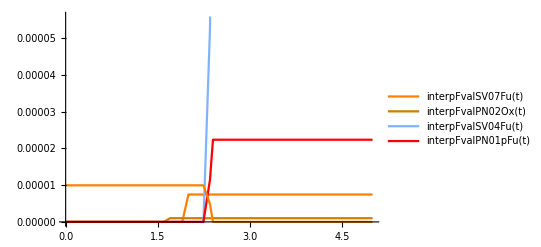

```mathematica
Plot[{interpFvalSV07Fu[t],interpFvalPN02Ox[t],interpFvalSV04Fu[t],interpFvalPN01pFu[t],interpFvalPN01aFu[t]},{t,0,5},PlotStyle->{RGBColor[1,0.5,0],RGBColor[0.8,0.5,0],RGBColor[0.5,0.7,1],Red},PlotLegends->LineLegend["Expressions"]]
```

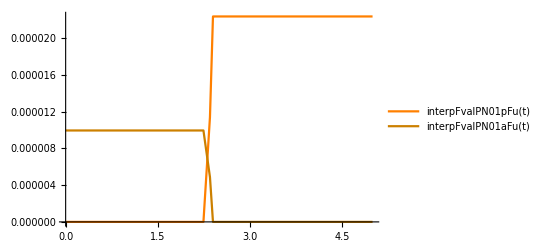

```mathematica
Plot[{interpFvalPN01pFu[t],interpFvalPN01aFu[t]},{t,0,5},PlotStyle->{RGBColor[1,0.5,0],RGBColor[0.8,0.5,0]},PlotLegends->LineLegend["Expressions"]]
```

## Расчет гидравлических потерь на участках труб

```mathematica
dfImportList2 = Delete[Import[pathToImportData,{"Data",12}],1];

dfList2 = {};
Do[listii = {};
Do[
If[ToString[Head[dfImportList2[[i,j]]]]==  ToString[Real],
AppendTo[listii,Round[dfImportList2[[i,j]]]],
AppendTo[listii,dfImportList2[[i,j]]]],
{j,Length[dfImportList2[[1]]]}];AppendTo[dfList2,listii],{i,Length[dfImportList2]}]
```

```mathematica
dfList2//TableForm
```

Tnk | Pmp | Ox | TnkToPmp | General | 
Pmp | Gg | Ox | PmpToGg |  | 
Pmp | TrbOut | Ox | PmpToTrbOut |  | 
Tnk | Pmp1 | Fu | TnkToPmp1 |  | 
Pmp1 | Ch | Fu | Pmp1ToCh |  | 
Pmp2 | 1 | Fu | Pmp2 |  | 
1 | Amp | Fu | Pmp2ToCh |  | 
Amp | 2 | Fu | Pmp2ToCh |  | 
2 | Ch | Fu | Pmp2ToCh |  | 
1 | 3 | Fu | Pmp2ToGg |  | 
3 | Gg | Fu | Pmp2ToGg |  | 
Pmp | PN02 | Ox | PmpToGg | resis | 
PN02 | Gg | Ox | PmpToGg |  | 
Pmp1 | TV02 | Fu | Pmp1ToCh |  | Ch
TV02 | SV04 | Fu | Pmp1ToCh |  | 
Pmp1 | SV04 | Fu | Pmp1ToCh |  | 
SV04 | CV03 | Fu | Pmp1ToCh |  | 
SV04 | Ch | Fu | Pmp1ToCh |  | 
CV03 | Ch | Fu | Pmp1ToCh |  | 
1 | AmpIn | Fu | Pmp2ToCh |  | 
AmpIn | AmpOut | Fu | Pmp2ToCh |  | 
AmpOut | CV01p1 | Fu | Pmp2ToCh |  | 
CV01p1 | 2 | Fu | Pmp2ToCh |  | 
2 | CV01p4 | Fu | Pmp2ToCh |  | 
CV01p4 | Ch | Fu | Pmp2ToCh |  | 
1 | TV01 | Fu | Pmp2ToGg |  | GgIgn
TV01 | PN01p | Fu | Pmp2ToGg |  | 
3 | Gg | Fu | Pmp2ToGg |  | 
2 | PN01a | Fu | Pmp2ToGg |  | Ampula
2 | 3 | Fu | Pmp2ToGg |  | 
1 | 2 | Fu | Pmp2ToCh |  | 
3 | SV07 | Fu | Pmp2ToGg |  | 
SV07 | Gg | Fu | Pmp2ToGg |  |

```mathematica
listEquatResis = defCreateEquation[dfList2,"resis"]
listEquatResis//ToExpression
```

{resisTnkToPmpOx =((pTnkOx-pPmpInOx)*rhoOx/mTnkToPmpOx^2),resisPmpToGgOx =((pPmpOutOx-pGg)*rhoOx/mPmpToGgOx^2),resisPmpToTrbOutOx =((pPmpOutOx-pTrbOut)*rhoOx/mPmpToTrbOutOx^2),resisTnkToPmp1Fu =((pTnkFu-pPmp1InFu)*rhoFu/mTnkToPmp1Fu^2),resisPmp1ToChFu =((pPmp1OutFu-pCh)*rhoFu/mPmp1ToChFu^2),resisPmp2To1Fu =((pPmp2OutFu-p1Fu)*rhoFu/mPmp2Fu^2),resis1ToAmpFu =((p1Fu-pAmpFu)*rhoFu/mPmp2ToChFu^2),resisAmpTo2Fu =((pAmpFu-p2Fu)*rhoFu/mPmp2ToChFu^2),resis2ToChFu =((p2Fu-pCh)*rhoFu/mPmp2ToChFu^2),resis1To3Fu =((p1Fu-p3Fu)*rhoFu/mPmp2ToGgFu^2),resis3ToGgFu =((p3Fu-pGg)*rhoFu/mPmp2ToGgFu^2),resisPmpToPN02Ox =((pPmpOutOx-pPN02InOx)*rhoOx/mPmpToGgOx^2),resisPN02ToGgOx =((pPN02OutOx-pGg)*rhoOx/mPmpToGgOx^2),resisPmp1ToTV02Fu =((pPmp1OutFu-pTV02InFu)*rhoFu/mPmp1ToChFu^2),resisTV02ToSV04Fu =((pTV02OutFu-pSV04InFu)*rhoFu/mPmp1ToChFu^2),resisPmp1ToSV04Fu =((pPmp1OutFu-pSV04InFu)*rhoFu/mPmp1ToChFu^2),resisSV04ToCV03Fu =((pSV04OutFu-pCV03InFu)*rhoFu/mPmp1ToChFu^2),resisSV04ToChFu =((pSV04OutFu-pCh)*rhoFu/mPmp1ToChFu^2),resisCV03ToChFu =((pCV03OutFu-pCh)*rhoFu/mPmp1ToChFu^2),resis1ToAmpInFu =((p1Fu-pAmpInFu)*rhoFu/mPmp2ToChFu^2),resisAmpInToAmpOutFu =((pAmpInFu-pAmpOutFu)*rhoFu/mPmp2ToChFu^2),resisAmpOutToCV01p1Fu =((pAmpOutFu-pCV01p1InFu)*rhoFu/mPmp2ToChFu^2),resisCV01p1To2Fu =((pCV01p1OutFu-p2Fu)*rhoFu/mPmp2ToChFu^2),resis2ToCV01p4Fu =((p2Fu-pCV01p4InFu)*rhoFu/mPmp2ToChFu^2),resisCV01p4ToChFu =((pCV01p4OutFu-pCh)*rhoFu/mPmp2ToChFu^2),resis1ToTV01Fu =((p1Fu-pTV01InFu)*rhoFu/mPmp2ToGgFu^2),resisTV01ToPN01pFu =((pTV01OutFu-pPN01pInFu)*rhoFu/mPmp2ToGgFu^2),resis3ToGgFu =((p3Fu-pGg)*rhoFu/mPmp2ToGgFu^2),resis2ToPN01aFu =((p2Fu-pPN01aInFu)*rhoFu/mPmp2ToGgFu^2),resis2To3Fu =((p2Fu-p3Fu)*rhoFu/mPmp2ToGgFu^2),resis1To2Fu =((p1Fu-p2Fu)*rhoFu/mPmp2ToChFu^2),resis3ToSV07Fu =((p3Fu-pSV07InFu)*rhoFu/mPmp2ToGgFu^2),resisSV07ToGgFu =((pSV07OutFu-pGg)*rhoFu/mPmp2ToGgFu^2)}

{969511.,2.07549×10^8,1.80738×10^11,6.47381×10^6,1.84055×10^9,7.15292×10^8,2.69021×10^11,2.79431×10^11,3.21949×10^12,2.1018×10^11,1.75632×10^11,1.70973×10^6,2.00603×10^8,1.19557×10^7,1.2923×10^7,6.13013×10^8,99217.1,1.16605×10^9,1.036×10^9,2.69021×10^11,2.66534×10^11,4.19643×10^9,9.11727×10^8,9.74802×10^9,3.2022×10^12,1.19286×10^10,1.34337×10^10,1.75632×10^11,6.97911×10^8,2.63502×10^10,5.48452×10^11,1.21489×10^11,4.51197×10^10}

```mathematica
resis3ToSV07FuNom = resis3ToSV07Fu;
```

```mathematica
listEquationDm = defCreateEquation[dfList2,"Dm"]
listEquationDm//ToExpression
```

{DmTnkToPmpOx =((pTnkOx-pPmpInOx-resisTnkToPmpOx/rhoOx * Abs[mTnkToPmpOx]* mTnkToPmpOx)/inertTnkToPmpOx),DmPmpToGgOx =((pPmpOutOx-pGg-resisPmpToGgOx/rhoOx * Abs[mPmpToGgOx]* mPmpToGgOx)/inertPmpToGgOx),DmPmpToTrbOutOx =((pPmpOutOx-pTrbOut-resisPmpToTrbOutOx/rhoOx * Abs[mPmpToTrbOutOx]* mPmpToTrbOutOx)/inertPmpToTrbOutOx),DmTnkToPmp1Fu =((pTnkFu-pPmp1InFu-resisTnkToPmp1Fu/rhoFu * Abs[mTnkToPmp1Fu]* mTnkToPmp1Fu)/inertTnkToPmp1Fu),DmPmp1ToChFu =((pPmp1OutFu-pCh-resisPmp1ToChFu/rhoFu * Abs[mPmp1ToChFu]* mPmp1ToChFu)/inertPmp1ToChFu),DmPmp2To1Fu =((pPmp2OutFu-p1Fu-resisPmp2To1Fu/rhoFu * Abs[mPmp2Fu]* mPmp2Fu)/inertPmp2To1Fu),Dm1ToAmpFu =((p1Fu-pAmpFu-resis1ToAmpFu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inert1ToAmpFu),DmAmpTo2Fu =((pAmpFu-p2Fu-resisAmpTo2Fu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inertAmpTo2Fu),Dm2ToChFu =((p2Fu-pCh-resis2ToChFu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inert2ToChFu),Dm1To3Fu =((p1Fu-p3Fu-resis1To3Fu/rhoFu * Abs[mPmp2ToGgFu]* mPmp2ToGgFu)/inert1To3Fu),Dm3ToGgFu =((p3Fu-pGg-resis3ToGgFu/rhoFu * Abs[mPmp2ToGgFu]* mPmp2ToGgFu)/inert3ToGgFu),DmPmpToPN02Ox =((pPmpOutOx-pPN02InOx-resisPmpToPN02Ox/rhoOx * Abs[mPmpToGgOx]* mPmpToGgOx)/inertPmpToPN02Ox),DmPN02ToGgOx =((pPN02OutOx-pGg-resisPN02ToGgOx/rhoOx * Abs[mPmpToGgOx]* mPmpToGgOx)/inertPN02ToGgOx),DmPmp1ToTV02Fu =((pPmp1OutFu-pTV02InFu-resisPmp1ToTV02Fu/rhoFu * Abs[mPmp1ToChFu]* mPmp1ToChFu)/inertPmp1ToTV02Fu),DmTV02ToSV04Fu =((pTV02OutFu-pSV04InFu-resisTV02ToSV04Fu/rhoFu * Abs[mPmp1ToChFu]* mPmp1ToChFu)/inertTV02ToSV04Fu),DmPmp1ToSV04Fu =((pPmp1OutFu-pSV04InFu-resisPmp1ToSV04Fu/rhoFu * Abs[mPmp1ToChFu]* mPmp1ToChFu)/inertPmp1ToSV04Fu),DmSV04ToCV03Fu =((pSV04OutFu-pCV03InFu-resisSV04ToCV03Fu/rhoFu * Abs[mPmp1ToChFu]* mPmp1ToChFu)/inertSV04ToCV03Fu),DmSV04ToChFu =((pSV04OutFu-pCh-resisSV04ToChFu/rhoFu * Abs[mPmp1ToChFu]* mPmp1ToChFu)/inertSV04ToChFu),DmCV03ToChFu =((pCV03OutFu-pCh-resisCV03ToChFu/rhoFu * Abs[mPmp1ToChFu]* mPmp1ToChFu)/inertCV03ToChFu),Dm1ToAmpInFu =((p1Fu-pAmpInFu-resis1ToAmpInFu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inert1ToAmpInFu),DmAmpInToAmpOutFu =((pAmpInFu-pAmpOutFu-resisAmpInToAmpOutFu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inertAmpInToAmpOutFu),DmAmpOutToCV01p1Fu =((pAmpOutFu-pCV01p1InFu-resisAmpOutToCV01p1Fu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inertAmpOutToCV01p1Fu),DmCV01p1To2Fu =((pCV01p1OutFu-p2Fu-resisCV01p1To2Fu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inertCV01p1To2Fu),Dm2ToCV01p4Fu =((p2Fu-pCV01p4InFu-resis2ToCV01p4Fu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inert2ToCV01p4Fu),DmCV01p4ToChFu =((pCV01p4OutFu-pCh-resisCV01p4ToChFu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inertCV01p4ToChFu),Dm1ToTV01Fu =((p1Fu-pTV01InFu-resis1ToTV01Fu/rhoFu * Abs[mPmp2ToGgFu]* mPmp2ToGgFu)/inert1ToTV01Fu),DmTV01ToPN01pFu =((pTV01OutFu-pPN01pInFu-resisTV01ToPN01pFu/rhoFu * Abs[mPmp2ToGgFu]* mPmp2ToGgFu)/inertTV01ToPN01pFu),Dm3ToGgFu =((p3Fu-pGg-resis3ToGgFu/rhoFu * Abs[mPmp2ToGgFu]* mPmp2ToGgFu)/inert3ToGgFu),Dm2ToPN01aFu =((p2Fu-pPN01aInFu-resis2ToPN01aFu/rhoFu * Abs[mPmp2ToGgFu]* mPmp2ToGgFu)/inert2ToPN01aFu),Dm2To3Fu =((p2Fu-p3Fu-resis2To3Fu/rhoFu * Abs[mPmp2ToGgFu]* mPmp2ToGgFu)/inert2To3Fu),Dm1To2Fu =((p1Fu-p2Fu-resis1To2Fu/rhoFu * Abs[mPmp2ToChFu]* mPmp2ToChFu)/inert1To2Fu),Dm3ToSV07Fu =((p3Fu-pSV07InFu-resis3ToSV07Fu/rhoFu * Abs[mPmp2ToGgFu]* mPmp2ToGgFu)/inert3ToSV07Fu),DmSV07ToGgFu =((pSV07OutFu-pGg-resisSV07ToGgFu/rhoFu * Abs[mPmp2ToGgFu]* mPmp2ToGgFu)/inertSV07ToGgFu)}

{0.,0.,0.,2.67521×10^-16,-1.93096×10^-14,1.87021×10^-16,0.,2.75676×10^-16,0.,0.,1.52035×10^-15,-6.61682×10^-16,0.,0.,0.,-1.52735×10^-14,0.,0.,-4.57285×10^-14,0.,(1.16415×10^-10)/inertAmpInToAmpOutFu,(1.81899×10^-12)/inertAmpOutToCV01p1Fu,6.7672×10^-18,3.23083×10^-17,0.,1.05095×10^-16,0.,1.52035×10^-15,5.14307×10^-17,3.29157×10^-15,4.03378×10^-16,(2.32831×10^-10)/inert3ToSV07Fu,(5.82077×10^-11)/inertSV07ToGgFu}

## Расчет гидравлических потерь через Valves

```mathematica
listValves = {{"CV01p1","mPmp2ToChFu","Fu"},{"CV01p4","mPmp2ToChFu","Fu"},{"PN02","mPmpToGgOx","Ox"},{"SV04","mPmp1ToChFu","Fu"},{"PN01p","mPmp2ToGgFu","Fu"},{"PN01a","mPmp2ToGgFu","Fu"},{"Amp","mPmp2ToChFu","Fu"}};
```

```mathematica
defCreateEquationValve[listValves]
defCreateEquationValve[listValves]//ToExpression
```

{resisValCV01p1FuNom =((pCV01p1InFu-pCV01p1OutFu)*rhoFu/mPmp2ToChFu^2),resisValCV01p4FuNom =((pCV01p4InFu-pCV01p4OutFu)*rhoFu/mPmp2ToChFu^2),resisValPN02OxNom =((pPN02InOx-pPN02OutOx)*rhoOx/mPmpToGgOx^2),resisValSV04FuNom =((pSV04InFu-pSV04OutFu)*rhoFu/mPmp1ToChFu^2),resisValPN01pFuNom =((pPN01pInFu-pPN01pOutFu)*rhoFu/mPmp2ToGgFu^2),resisValPN01aFuNom =((pPN01aInFu-pPN01aOutFu)*rhoFu/mPmp2ToGgFu^2),resisValAmpFuNom =((pAmpInFu-pAmpOutFu)*rhoFu/mPmp2ToChFu^2)}

{7.78833×10^9,7.53885×10^9,5.23626×10^6,6.14898×10^7,1.00186×10^9,5.05909×10^9,2.66534×10^11}

## Обратный клапан

```mathematica
interpZSpringOtSilaSpring[silaSpring_]:=Block[{},{InterpolatingFunction[…][silaSpring]*10^3}][[1]]
```

```mathematica
{fGapBodyFlapCV01,fSeatCV01,masMovingPartsCV01,fFlapExterCV01}=defCheckVal[diamSeatCV01,diamBodyInterCV01,diamFlapExterCV01,diamConnectorInCV01,masFlapCV01,masSpringCV01,diamStemFlapCV01]
```

{0.0000111841,0.0000785398,0.0181,0.000243285}

```mathematica
{xValCV01p1Fu,DxValCV01p1Fu,D2xCV01p1Fu}={0.,0.,0.};
{xValCV01p4Fu,DxValCV01p4Fu,D2xValvCV01p4Fu}={0.,0.,0.};
```

```mathematica
funcCheckValveCV01[p1_,p2_,u_,x_]:= Block[{result},{
result =funcCheckValve[p1,p2,u,x,xFlapMaxCV01,fGapBodyFlapCV01,fFlapExterCV01,diamSeatCV01,silaSpring0CV01,zSpringCV01,myuThrotCV01,fSeatCV01,silaFrictStaticCV01,silaFrictKineticCV01,coefPropFrictViscousCV01,masMovingPartsCV01,FTREN,coefSilaFlowCV01
];
result
}][[1]]
```

```mathematica
funcCheckValveCalcResisOtXCV01[x_,coefCorectivResis_]:= Block[{result},{
result =funcCheckValveCalcResisOtX[x,diamSeatCV01,fGapBodyFlapCV01,coefCorectivResis];
result
}][[1,1]]
```

```mathematica
funcConditionsXDxVal[0,-1,xFlapMaxCV01]
```

{0.,0.}

```mathematica
fThrotValCV01p1Fu=funcCheckValveCV01[pCV01p1InFu,pCV01p1OutFu,1,xFlapMaxCV01][[3]];
fThrotValCV01p4Fu=funcCheckValveCV01[pCV01p4InFu,pCV01p4OutFu,1,xFlapMaxCV01][[3]];
```

```mathematica
coefResisValCV01p1Fu = resisValCV01p1FuNom/1/fThrotValCV01p1Fu^2;
coefResisValCV01p4Fu = resisValCV01p4FuNom/1/fThrotValCV01p4Fu^2;

Grid[{{"coefResisValCV01q1Fu",coefResisValCV01p1Fu},{"coefResisValCV01q4Fu",coefResisValCV01p4Fu}},Frame->All,Alignment->Left]
```

coefResisValCV01q1Fu | 0.97419
coefResisValCV01q4Fu | 0.942986

```mathematica
defsisBalanseDm[{"Pmp2"},{"1"},{"2","3"},"rhoFu","Fu"]
defsisBalanseDm[{"1"},{"2"},{"3","Ch"},"rhoFu","Fu"]
defsisBalanseDm[{"1","2"},{"3"},{"Gg"},"rhoFu","Fu"]
```

defsisBalanseDm[{Pmp2},{1},{2,3},rhoFu,Fu]

defsisBalanseDm[{1},{2},{3,Ch},rhoFu,Fu]

defsisBalanseDm[{1,2},{3},{Gg},rhoFu,Fu]

```mathematica
p1FuNom
p2FuNom
p3FuNom
```

2.18404×10^7

1.98033×10^7

1.95113×10^7

## Начальные условия

```mathematica
(*(pAmpInFu-pAmpOutFu)/10^5*)
```

```mathematica
(*(p1Fu-pAmpInFu)/10^5*)
```

```mathematica
replaceImaginaryWithZero[x_]:=If[Im[x]≠0,0,x]
```

Установка начальных значений и инициализация маркеров для работы логики и вывода на печать интересующих точек.

```mathematica
resultPrint= {};
resultPrintNew= {};
numItemPrint = 0;
TIME=0;        (* Начало интервала интегрирования *)
stepPrint = IntegerPart[endTime/dt/countPrint];
n=IntegerPart[endTime/dt];
```

```mathematica
{kmCh ,kmGg }={0,0};
```

```mathematica
{flagValOpenPN02Ox,flagValOpenSV04Fu,flagValOpenAmpFu,flagValOpenPN01pFu,flagValOpenPN01aFu}={0,0,0,0,0};
{flagFillSV04ToChFu,flagFillPmpToGgOx,flagFillAmpTo2Fu,flagFill2ToChFu,flagFill2To3Fu,flagFill3ToGgFu,flagFill2ToGgFu}={0,0,0,0,0,0,0};
```

```mathematica
flagModeFill = 0; (* mode equation Fill || NoFill *)
```

```mathematica
pCh= pEnv;
pGg = pEnv;
pGv = pEnv;
pCh = pEnv;
rpm = 1;omega = 1*ω;
mGg=0;mGv=0;
DmassN2 = 0;massN2=0;
```

```mathematica
{DpPmp1InFu,DpPmpInOx,DmTnkToPmp1Fu,DmPmp1ToChFu,DmPmp2To1Fu,Dm1To5Fu,Dm1To2Fu,Dm5To2Fu,Dm2ToChFu,Dm2To3Fu,Dm1To3Fu,Dm3ToGgFu,Dm2ToGgFu,DmTnkToPmpOx,DmPmpToGgOx,DvolSV04ToChFu,DvolAmpTo2Fu,Dvol2ToChFu,Dvol2ToGgFu,DvolPN02ToGgOx,DpGg,DpGv,DpCh,Domega,DmassN2,Dp1Fu,Dp2Fu,Dp3Fu,Dp5Fu,DmasN2}=ConstantArray[0,Length[{DpPmp1InFu,DpPmpInOx,DmTnkToPmp1Fu,DmPmp1ToChFu,DmPmp2To1Fu,Dm1To5Fu,Dm1To2Fu,Dm5To2Fu,Dm2ToChFu,Dm2To3Fu,Dm1To3Fu,Dm3ToGgFu,Dm2ToGgFu,DmTnkToPmpOx,DmPmpToGgOx,DvolSV04ToChFu,DvolAmpTo2Fu,Dvol2ToChFu,Dvol2ToGgFu,DvolPN02ToGgOx,DpGg,DpGv,DpCh,Domega,DmassN2,Dp1Fu,Dp2Fu,Dp3Fu,Dp5Fu,DmasN2}]];
```

```mathematica
{pPmp1InFu,pAmpFu,pPmpInOx}={pTnkFu,pTnkFu,pTnkOx};
{mTnkToPmp1Fu,mPmp1ToChFu,mPmp2To1Fu,m1ToAmpFu,mAmpTo2Fu,m2ToChFu,m2To3Fu,m1To3Fu,m3ToGgFu,mTnkToPmpOx,mPmpToGgOx}=ConstantArray[0,Length[{mTnkToPmp1Fu,mPmp1ToChFu,mPmp2To1Fu,m1ToAmpFu,mAmpTo2Fu,m2ToChFu,m2To3Fu,m1To3Fu,m3ToGgFu,mTnkToPmpOx,mPmpToGgOx}]];
{volSV04ToChFu,volAmpTo2Fu,vol2ToChFu,vol2To3Fu,vol3ToGgFu,volPN02ToGgOx}={0,0,0,0,0,0};
{xCV01p1Fu,uCV01p1Fu,xCV01p4Fu,uCV01p4Fu}={xFlapMaxCV01,0,xFlapMaxCV01,0};
```

```mathematica
{mPmp1ToChFuFill,mPmp1ToChFuJet,mAmpTo2FuFill,mAmpTo2FuJet,m2ToChFuFill,m2ToChFuJet,m2To3FuFill,m2To3FuJet,m3ToGgFuFill,m3ToGgFuJet,mPmpToGgOxFill,mPmpToGgOxJet}=ConstantArray[0,Length[{mPmp1ToChFuFill,mPmp1ToChFuJet,mAmpTo2FuFill,mAmpTo2FuJet,m2ToChFuFill,m2ToChFuJet,m2To3FuFill,m2To3FuJet,m3ToGgFuFill,m3ToGgFuJet,mPmpToGgOxFill,mPmpToGgOxJet}]];
```

```mathematica
mPmp2OutFu = 0;
{pPmp1OutFu,pPmp2OutFu,pPmpOutOx,pTrbIn,pTrbOut,p1Fu,p5Fu,p2Fu,p3Fu}={pTnkFu,pTnkFu,pTnkOx,pEnv,pEnv,pTnkFu,pEnv,pEnv,pEnv};
```

```mathematica
{Dp1Fu,Dp2Fu,Dp3Fu, Dm1To2Fu}={0,0,0,0};
```

```mathematica
{m1To2Fu,m1To2FuFill,m1To2FuJet,m1To3Fu,m2ToChFu,m3ToGgFu,m2ToGgFu,m1To5Fu,m5To2Fu}=ConstantArray[0,Length[{m1To2Fu,m1To2FuFill,m1To2FuJet,m1To3Fu,m2ToChFu,m3ToGgFu,m2ToGgFu,m1To5Fu,m5To2Fu}]];
```

```mathematica
resisPN01aFu = 1/(2*interpFvalPN01aFu[0.5]^2);
{resis2ToChFuNom,resis2To3FuNom,resis3ToGgFuNom}={resis2ToChFu,resis2ToPN01aFu+resisPN01aFu,resis3ToGgFu};
{flagBurnGg,flagBurnGgSTOP,flagBurnCh,flagBurnChSTOP,flagAdTauCh}={0,0,0,0,0};
tZapolnAll = 0;
```

```mathematica
vol2ToGgFuNom = vol2To3FuNom+vol3ToGgFuNom;
vol2ToGgFu = 0;
```

```mathematica
inert2ToGgFuNom = inert2To3FuNom+inert3ToGgFuNom;
inert2ToGgFu = 0;
```

```mathematica
volGgN2Nom = vol2ToGgFuNom;
```

```mathematica
massGgN2 = (pEnv volGgN2Nom)/(RN2 TN2);
pGgVar= pEnv;
timeAddMassFlow2ChGG = 0;
flagFillAmpForTimeAddMasFlow = 0;
masN2 = massGgN2;
timeConfinesSV07 = 0;
```

```mathematica
{p2Fudt,p3Fudt}={p2Fu,p3Fu};
{Dp2Fudt,Dp3Fudt} = {0,0};
{pMax,pMinFu,pMinOx}={pPmp2OutFuNom*1.2,interpPressureVaporFu[293],interpPressureVaporOx[90]};
```

```mathematica
{RCh,RGg,RGv}={1,1,1};
{TGv,TCh,TGg}={TEnv,TEnv,TEnv};
{mGg,mGv,mCh}={0,0,0};
{mGgOxFill,mGgOxJet}={0,0};
mPmpToTrbOutOx = 0;
mode = 0;

{flagTauGg,flagTauGgOx,flagTauGgFu,flagTauChFu,flagTauChFuGen}={0,0,0,0,0};
{timeAdTauGg,tBurnGg,tBurnCh,timeAdTauCh,tStpGg,tStpCh}={100,100,100,100,100,100};
{mPmpOxOut,mPmp1FuOut,mPmp2FuOut}={mPmpToGgOxFill+mPmpToTrbOutOx,mPmp2To1Fu,mPmp2To1Fu+mPmp1ToChFuFill};
```

```mathematica
{p1FuAlg,p2FuAlg,p3FuAlg,p5FuAlg}={p1Fu,p2Fu,p3Fu,p5Fu};
```

```mathematica
mLeakOx = (1.1+1.24+0.385)*10^-3*rhoOx
mLeakFu1 = (3.37+4.42)*10^-4*rhoFu
mLeakFu2 = (1.24+2.78)*10^-4*rhoFu
```

3.07743

0.634425

0.327393

```mathematica
{etaPmp1Fu,etaPmp2Fu,etaPmpOx} = {1,1,1};
{kGg,kCh}={1.4,1.4};
```

```mathematica
{mChOx,mChFu,mGgOx,mGgFu,mPmpOutOx} = {0,0, 0, 0,0}
```

{0,0,0,0,0}

```mathematica
rhoOx
rhoFu
```

1129.33

814.41

## Подготовка перед началом расчета ограничений, условий и формирование словаря для вывода данных для экспорта и построения графиков

```mathematica
dataLor={
{pPmp1InFu,DpPmp1InFu,pTnkFu},
{pPmpInOx,DpPmpInOx,pTnkOx},
{mTnkToPmp1Fu,DmTnkToPmp1Fu,0},
{mPmp1ToChFu,DmPmp1ToChFu,0},
{mPmp2To1Fu,DmPmp2To1Fu,0},
{m1To2Fu,Dm1To2Fu,0},
{m2ToChFu,Dm2ToChFu,0},
{m2To3Fu,Dm2To3Fu,0},
{m1To3Fu,Dm1To3Fu,0},
{m3ToGgFu,Dm3ToGgFu,0},
{mTnkToPmpOx,DmTnkToPmpOx,0},
{mPmpToGgOx,DmPmpToGgOx,0},
{volSV04ToChFu,DvolSV04ToChFu,0},
{volAmpTo2Fu,DvolAmpTo2Fu,0},
{vol2ToChFu,Dvol2ToChFu,0},
{vol2To3Fu,Dvol2To3Fu,0},
{vol3ToGgFu,Dvol3ToGgFu,0},
{volPN02ToGgOx,DvolPN02ToGgOx,0},
{xCV01p1Fu,DxCV01p1Fu,xFlapMaxCV01},
{uCV01p1Fu,DuCV01p1Fu,0},
{xCV01p4Fu,DxCV01p4Fu,xFlapMaxCV01},
{uCV01p4Fu,DuCV01p4Fu,0},
{p1Fu,Dp1Fu,pTnkFu},
{p2Fu,Dp2Fu,pEnv},
{p3Fu,Dp3Fu,pEnv},
{pGg,DpGg,pEnv},
{pGv,DpGv,pEnv},
{pCh,DpCh,pEnv},
{omega,Domega,2*Pi*1/60}
};
```

Ограничения

```mathematica
defConfinesAll[t_]:= Block[{},
{
If[mode == 0,{p1Fu,p2Fu,p3Fu,p5Fu}={p1FuAlg,p2FuAlg,p3FuAlg,p5FuAlg};];
(*PRESSURE*)
{pPmpInOx,pPmpOutOx}=Min[Max[#,interpPressureVaporFu[293]],pMax]&/@{pPmpInOx,pPmpOutOx};
{pPmp1InFu,pPmp1OutFu,pPmp2InFu,pPmp2OutFu,p1Fu ,p2Fu,p3Fu,p5Fu}=Min[Max[#,interpPressureVaporFu[293]],500*10^5]&/@{pPmp1InFu,pPmp1OutFu,pPmp2InFu,pPmp2OutFu,p1Fu ,p2Fu,p3Fu,p5Fu};
{pGv,pCh}=Max[#,pEnv]&/@{pGv,pCh};
{pGg}=Max[Min[#,p3Fu],pEnv]&/@{pGg};
(*VOLUME*)
{DvolAmpTo2Fu,Dvol2ToChFu,DvolSV04ToChFu,DvolPN02ToGgOx}=Max[#,0]&/@{DvolAmpTo2Fu,Dvol2ToChFu,DvolSV04ToChFu,DvolPN02ToGgOx};
{vol2ToGgFu}=Min[Max[#,0],vol2ToGgFuNom]&/@{vol2ToGgFu};
(*MASS FLOW*)
{mTnkToPmpOx,mPmpToGgOx}=Max[#,0]&/@{mTnkToPmpOx,mPmpToGgOx};
{mTnkToPmp1Fu,mPmp1ToChFu}=Max[#,0]&/@{mTnkToPmp1Fu,mPmp1ToChFu};
{mPmpOxOut,mPmp1FuOut,mPmp2FuOut}={mPmpToGgOxFill+mPmpToTrbOutOx,mPmp2To1Fu+mPmp1ToChFuFill,mPmp2To1Fu};

{mPmp2To1Fu,m2ToChFu}=Max[#,0]&/@{mPmp2To1Fu,m2ToChFu};
{m2To3Fu,(*m3ToGgFu,*)m1To2Fu,(*m1To3Fu,*) m1To5Fu,m5To2Fu,mPmp2To1Fu(*,m2ToGgFu*)}=Max[#,0]&/@{m2To3Fu,(*m3ToGgFu,*)m1To2Fu,(*m1To3Fu,*) m1To5Fu,m5To2Fu,mPmp2To1Fu(*,m2ToGgFu*)};
(*If[0.1> t≥ 0(*tValSV04Fu1*)(*+dtValSV04Fu1*),{m3ToGgFu,m1To3Fu ,m2ToGgFu}=Max[#,0]&/@{m3ToGgFu,m1To3Fu ,m2ToGgFu}];*)
If[t≥ tValSV07Fu1(*+dtValSV04Fu1*),{m3ToGgFu,m1To3Fu ,m2ToGgFu}=Max[#,0]&/@{m3ToGgFu,m1To3Fu ,m2ToGgFu}(*{m2To3Fu,m3ToGgFu,m1To2Fu,m1To3Fu, m1To5Fu,m5To2Fu,mPmp2To1Fu,m2ToGgFu}=Max[#,0]&/@{m2To3Fu,m3ToGgFu,m1To2Fu,m1To3Fu, m1To5Fu,m5To2Fu,mPmp2To1Fu,m2ToGgFu}*)];
(*OTHER*)
{omega}=Max[#,1]&/@{omega};
{masN2}=Max[#,0]&/@{masN2};
}]
```

```mathematica
defCorrection[if_]:=Block[{},
{
(*If[2≤if(*≤ 2.5*),pCh=pChNom];*)
};]
```

Условия

```mathematica
defConditionsAll[t_]:=Block[{},
{
(*Gg*)
If[flagTauGgOx == 0 && mPmpToGgOx>mGgOxMin(*&& flagFillPmpToGgOx== 1*), flagTauGgOx = 1;Print["Расход окислителя в ГГ пришел на: ",t//N, " секунде"]];
If[flagTauGgFu == 0 &&flagFill2ToGgFu== 1&& m2ToGgFu>mGgFuMin, flagTauGgFu = 1;Print["Расход горючего в ГГ пришел на: ",t//N, " секунде"]];
If[flagTauGg== 0 &&flagTauGgOx ==1 &&flagTauGgFu ==1,timeAdTauGg= t+timeDelayIgnGg; flagTauGg = 1;
Print["Оба компонента поступили в ГГ на: ",t//N]];
If[flagBurnGg== 0 && flagTauGg == 1 && t≥ timeAdTauGg(*&& pPmp2OutFu≥ 50*10^5*δP && pPmpOutOx≥50*10^5*δP*), flagBurnGg=1;Print["Начало горения в ГГ на: ",t//N];tBurnGg =t//N];
If[flagBurnGgSTOP == 1,pGg = pEnv;pTrbIn = pEnv];
(*Ch*)
If[flagTauChFuGen == 0 && mPmp1ToChFu>mChFuGenMin, flagTauChFuGen = 1;Print["Расход горючего от Pmp1Fu в КС пришел на: ",t//N, " секунде"]];
If[flagTauChFu == 0 && m2ToChFu>mChIngFuMin, flagTauChFu = 1;Print["Расход горючего от Pmp2Fu в КС пришел на: ",t//N, " секунде"]];
If[flagAdTauCh== 0&&flagTauChFu== 1&&flagBurnGg== 1,timeAdTauCh = t+timeDelayIgnCh;flagAdTauCh =1];
If[flagBurnCh== 0 && flagTauChFu == 1 &&flagBurnGg== 1&& t≥ timeAdTauCh, flagBurnCh=1;Print["Начало горения в КС на: ",t//N];tBurnCh =t//N];
If[flagBurnChSTOP == 1,pCh = pEnv];
(* режимы при заполнении *)
If[ flagFill2ToGgFu== 0(*t<2*),mode = 0,mode = 1];
(*Заполнения*)
If[tZapolnAll== 0 && flagFillAmpTo2Fu==  1&& flagFill2ToChFu== 1&&  flagFill2ToGgFu== 1,tZapolnAll = t];
If[flagFillAmpTo2Fu == 1 && flagFill2Fu == 0 , flagFill2Fu = 1;timeCocrrectMassFlow=t+0.001];
If[flagFillAmpTo2Fu == 1 && t<timeCocrrectMassFlow ,{m2ToChFu,m2ToGgFu}={m1To2Fu/2,m1To2Fu/2}];
If[mode == 0,{p1Fu,p2Fu,p3Fu,p5Fu}={p1FuAlg,p2FuAlg,p3FuAlg,p5FuAlg};];

If[mode == 1 && flagCorrectMassFlowSV07 == 0,
flagCorrectMassFlowSV07= 1;{m1To5Fu,m5To2Fu,m2To3Fu,m3ToGgFu,m1To3Fu}={m1To2Fu,m1To2Fu,m2ToGgFu,m2ToGgFu,0};{p1Fu,p2Fu,p3Fu,p5Fu}={p1FuAlg,p2FuAlg,p3FuAlg,p5FuAlg}];
If[mode == 0 ,{m1To5Fu,m5To2Fu,m2To3Fu}={m1To2Fu,m1To2Fu,m2ToGgFu}];
If[tValSV07Fu1 + dtValSV07Fu1≤ t&& tZapolnAll== 0,{m3ToGgFu}={m2ToGgFu}];
If[mode == 1,{m2ToGgFu,m1To2Fu}={m3ToGgFu,m1To5Fu};];
If[t≤ tValPN01pFu1,m1To3Fu = 0];
}]
```

```mathematica
timeCocrrectMassFlow = 100;
flagCorrectMassFlowSV07 = 0;
coefMassFlow2ChGg=1;
flagFill2Fu = 0;
varTest=2;
```

Маркеры

```mathematica
flagBurnIgnGg = 0 ;
flagBurnIgnGgSTOP = 0;
flagTauIgnGgOx=0;
flagTauIgnGgFu=0;
flagTauIgnGg = 0;
timeAdTauIgnGg = Infinity;
timeAdTauIgnCh = Infinity;

flagTauIgnChOx = 0;
flagTauIgnChFu=0;
flagTauIgnCh=0;
flagBurnIgnCh=0;
flagBurnIgnChSTOP=0;

TTrbOut = 293;
masBallOx = 0;
masBallFu = 0;

mTrb = 0;
```

```mathematica
defTagAndPrint[t_]:=Block[{},
{
}];
```

Словарь для печати

```mathematica
(*listVarForCreateDict = "pPmp1InFu,pPmpInOx,mTnkToPmp1Fu,mPmp1ToChFu,mPmp2To1Fu,m1To2Fu,m2ToChFu,m2To3Fu,m1To3Fu,m3ToGgFu,m2ToGgFu,mTnkToPmpOx,mPmpToGgOx,volSV04ToChFu,volAmpTo2Fu,vol2ToChFu,vol2ToGgFu,volPN02ToGgOx,pGg,pGv,pCh,massN2,p1Fu,p2Fu,p3Fu,pGgVar,rpm,pPmp2OutFu,varTest,masN2,TN2,mN2,resisPN01aFuCalc,resisPN01pFuCalc,kmCh,kmGg,mGgOxFill,mGgOxJet,pPmpOutOx,pPmp1OutFu,mGg,mGv,mCh,RCh,RGg,RGv,TGv,TCh,TGg,kGg,kGv,kCh,mPmpToTrbOutOx,mPmpOxOut,mPmp1FuOut,mPmp2FuOut,mode,torqTrb,torqStTrb,torqPmp1Fu,torqPmp2Fu,torqPmpOx,coefMassFlow2ChGg,etaPmpOx,etaPmp1Fu,etaPmp2Fu,flagFill2ToGgFu,m1To5Fu,m5To2Fu,p5Fu,resis2To3Fu,mPmp1ToChFuFill,mGgOx,mGgFu,mChOx,mChFu,mPmpOutOx";*)
listVarForCreateDict = "rpm,pPmpInOx,pPmpOutOx,pPmp1InFu,pPmp1OutFu,pPmp2OutFu,p1Fu,p5Fu,p2Fu,p3Fu,pGgVar,pGg,pGv,pCh,mTnkToPmpOx,mPmpOutOx,mPmpToGgOx,mPmpToTrbOutOx,mTnkToPmp1Fu,mPmp1ToChFu,mPmp2To1Fu,m1To3Fu,m1To5Fu,m5To2Fu,m2ToChFu,m2To3Fu,m3ToGgFu,mGg,mGv,mCh,mN2,mGgOx,mGgFu,mPmpToTrbOutOx,mChOx,mChFu,massN2,kmGg,kmCh,kGg,kGv,kCh,RGg,RGv,RCh,TGg,TGv,TCh,volPN02ToGgOx,volSV04ToChFu,volAmpTo2Fu,vol2ToGgFu,vol2ToChFu, m2ToGgFu";


myDictForSaveResultsTXT = defCreateDict[listVarForCreateDict];
```

```mathematica
(*defsisBalanseDm[{"0"},{"1"},{"2","3"},"rho"]/.{a01-> resisPmp2To1Fu,a12->resis1To2Fu ,a13-> resis1To3Fu,j01-> inertPmp2To1Fu,j12-> inert1To2Fu,j13-> inert1To3Fu,m01->mPmp2To1Fu ,m12-> m1To2Fu,m13->m1To3Fu ,p0-> pPmp2OutFu,p2-> p2Fu,p3-> p3Fu,rho->rhoFu }*)
```

```mathematica
defsisBalanseDm[{"1"},{"2"},{"3","Ch"},"rho"]/.{a12-> resis1To2Fu,a23->resis2To3Fu ,a2Ch-> resis2ToChFu,j12-> inert1To2Fu,j23-> inert2To3Fu,j2Ch-> inert2ToChFu,m12->m1To2Fu ,m23-> m2To3Fu, m2Ch->m2ToChFu ,p1-> p1Fu,p3-> p3Fu,rho->rhoFu }
```

103567.

```mathematica
defsisBalanseDm[{"1","2"},{"3"},{"Gg"},"rho"]/.{a13-> resis1To3Fu,a23->resis2To3Fu ,a3Gg-> resis3ToGgFu,j13-> inert1To3Fu,j23-> inert2To3Fu,j3Gg-> inert3ToGgFu,m13->m1To3Fu ,m23-> m2To3Fu,m3Gg->m3ToGgFu ,p1-> p1Fu,p2-> p2Fu,rho->rhoFu }
```

103357.

```mathematica
defsisBalanseDm[{"2"},{"3"},{"Gg"},"rho"]/.{a23-> resis2To3Fu,a3Gg->resis3ToGgFu ,j23-> inert2To3Fu,j3Gg-> inert3ToGgFu,m23->m2To3Fu ,m3Gg-> m3ToGgFu,p2-> p2Fu,rho->rhoFu}
```

100000.

```mathematica
(*Solve[{
Dm1To2Fu==  (p1Fu-p2Fu-resis1To2Fu/rhoFu * Abs[m1To2Fu]* m1To2Fu)/inert1To2Fu,
Dm2ToChFu== (p2Fu-pCh-resis2ToChFu/rhoFu * Abs[m2ToChFu]* m2ToChFu)/inert2ToChFu,
Dm2ToGgFu== (p2Fu-pGgVar-resis2ToGgFu/rhoFu * Abs[m2ToGgFu]* m2ToGgFu)/inert2ToGgFu,
Dm1To2Fu== Dm2ToChFu+Dm2ToGgFu
},{p2Fu,Dm1To2Fu,Dm2ToChFu,Dm2ToGgFu}]*)
```

```mathematica
-((-inert2ToChFu inert2ToGgFu p1Fu rhoFu-inert1To2Fu inert2ToGgFu pCh rhoFu-inert1To2Fu inert2ToChFu pGgVar rhoFu+inert2ToChFu inert2ToGgFu m1To2Fu resis1To2Fu Abs[m1To2Fu]-inert1To2Fu inert2ToGgFu m2ToChFu resis2ToChFu Abs[m2ToChFu]-inert1To2Fu inert2ToChFu m2ToGgFu resis2ToGgFu Abs[m2ToGgFu])/((inert1To2Fu inert2ToChFu+inert1To2Fu inert2ToGgFu+inert2ToChFu inert2ToGgFu) rhoFu))
```

100000.

```mathematica
(*ClearAll["Global`*"]*)
```

```mathematica
(*d1[]:= p1Fu = defPNod[{{pPmp2OutFu,mPmp2To1Fu,resisPmp2To1Fu,inertPmp2To1Fu,rhoFu}},{{p5Fu,m1To5Fu,resis1To5Fu,inert1To5Fu,rhoFu},{p3Fu,m1To3Fu,resis1To3Fu,inert1To3Fu,rhoFu}}];
d2[]:= Dp3Fu = (m1To3Fu +m2To3Fu-m3ToGgFu)/C3Fu;
d3[]:= Dp5Fu = (m1To5Fu-m5To2Fu)/C5Fu;
d4[]:= Dp2Fu = (m5To2Fu-m2To3Fu-m2ToChFu)/C2Fu;
d5[]:= DmPmp2To1Fu = (pPmp2OutFu-p1Fu-resisPmp2To1Fu/rhoFu*Abs[mPmp2To1Fu]*mPmp2To1Fu)/inertPmp2To1Fu;
d6[]:= Dm1To5 = (p1Fu - p5Fu - resis1To5Fu/rhoFu*Abs[m1To5Fu]*m1To5Fu)/inert1To5Fu;
d7[]:= Dm5To2 = (p5Fu-p2Fu-resis5To2Fu/rhoFu*Abs[m5To2Fu]*m5To2Fu)/inert5To2Fu;
d8[]:= Dm2ToChFu = (p2Fu - pCh-resis2ToChFu/rhoFu*Abs[m2ToChFu]*m2ToChFu)/inert2ToChFu;
d9[]:=Dm2To3Fu = (p2Fu-p3Fu-resis2To3Fu/rhoFu*Abs[m2To3Fu]*m2To3Fu)/inert2To3Fu;
d10[]:= Dm3ToGgFu =(p3Fu-pGg-resis3ToGgFu/rhoFu*Abs[m3ToGgFu]*m3ToGgFu)/inert3ToGgFu;
d11[]:= Dm1To3Fu = (p1Fu-p3Fu-resis1To3Fu/rhoFu*Abs[m1To3Fu]*m1To3Fu)/inert1To3Fu;*)
```

```mathematica
(*(* режимы при заполнении *)
If[ flagFill2ToGgFu== 0,mode = 0;,
If[ flagFill2ToGgFu== 1&&t≤timeConfinesSV07+0.1,mode = 1;,
If[ flagFill2ToGgFu== 1&&t>timeConfinesSV07+0.1&& t≤ tValPN01pFu1,mode = 2;,
If[ flagFill2ToGgFu== 1&&t>timeConfinesSV07+0.1&& tValPN01pFu1<t≤ tValPN01pFu1+dtValPN01pFu1,mode = 3;,
If[ flagFill2ToGgFu== 1&&t>timeConfinesSV07+0.1&& t>tValPN01pFu1+dtValPN01pFu1,mode = 4;];];];];];*)
```

```mathematica
(* схема переключение на ур-я с податливостами после заполнения всех магистралий *)
```

Cхема переключение на ур-я с податливостами после заполнения всех магистралий:
Режимы работы системы:
0 режим - до заполнения 2-ГГ 
1 режим - после открытия клапана SV07 + 0.1
2 режим - до начала переключения PN01
3 режим - в момент переключения PN01
4 режим - после переключения PN01

## Правые части

```mathematica
p1FuCalc=p1Fu;
tst = 0;
```

```mathematica
pPmp2OutFuCalc=pPmp1OutFu+FuncHPmp2Fu[mPmp2To1Fu,rhoFu,omega/ω] *coefHFu2;
```

```mathematica
(*p1FuAlg =Max[Min[defPNod[{{pPmp2OutFu,mPmp2To1Fu,resisPmp2To1Fu,inertPmp2To1Fu,rhoFu}},{{p2Fu,m1To2Fu,resis1To2Fu,inert1To2Fu,rhoFu}}],pMax],0.01]
p2FuAlg=Max[Min[defPNod[{{p1Fu,m1To2Fu,resis1To2Fu,inert1To2Fu,rhoFu}},{{pGgVar,m2ToGgFu,resis2ToSV07Fu,inert2ToGgFu,rhoFu},{pCh,m2ToChFu,resis2ToChFu,inert2ToChFu,rhoFu}}],pMax],0.01]*)
```

```mathematica
Prav[t_,y_]:=Block[{
(* Valve *)
(* mass *)                   
(* pressure *)
pPmp1InFu,pPmpInOx,pGg,pGv,pCh,p1Fu,p2Fu,p3Fu,p5Fu,
(* mass flow rate *)
mTnkToPmp1Fu,mPmp1ToChFu,mPmp2To1Fu,m1To5Fu,m5To2Fu,m2ToChFu,m2To3Fu,m1To3Fu,m3ToGgFu,mTnkToPmpOx,mPmpToGgOx,m2ToGgFu,masN2,m1To2Fu,
(* volume *)
volSV04ToChFu,volAmpTo2Fu,vol2ToChFu,vol2ToGgFu,volPN02ToGgOx,
(* Other *)
omega
},{{
pPmp1InFu,pPmpInOx,mTnkToPmp1Fu,mPmp1ToChFu,mPmp2To1Fu,m1To5Fu,m1To2Fu,m5To2Fu,m2ToChFu,m2To3Fu,m1To3Fu,m3ToGgFu,m2ToGgFu,mTnkToPmpOx,mPmpToGgOx,volSV04ToChFu,volAmpTo2Fu,vol2ToChFu,vol2ToGgFu,volPN02ToGgOx,pGg,pGv,pCh,omega,p1Fu,p2Fu,p3Fu,p5Fu,masN2}=y;
defConfinesAll[t];
defConditionsAll[t];
(* Зануляем производные *)
{DpPmp1InFu,DpPmpInOx,DmTnkToPmp1Fu,DmPmp1ToChFu,DmPmp2To1Fu,Dm1To5Fu,Dm1To2Fu,Dm5To2Fu,Dm2ToChFu,Dm2To3Fu,Dm1To3Fu,Dm3ToGgFu,Dm2ToGgFu,DmTnkToPmpOx,DmPmpToGgOx,DvolSV04ToChFu,DvolAmpTo2Fu,Dvol2ToChFu,Dvol2ToGgFu,DvolPN02ToGgOx,DpGg,DpGv,DpCh,Domega,Dp1Fu,Dp2Fu,Dp3Fu,Dp5Fu,DmasN2
}=ConstantArray[0,Length[y]];
(* Система уравнений *)
iterRunge = iterRunge+1;
rpm = omega/ω//N;
pTnkFu = pTnkFuNom;
pTnkOx = pTnkOxNom;

(* powers ZAPOLNO && ratioVol *)
power = 0.1;
coefVolAmpTo2 = Min[(volAmpTo2Fu/volAmpTo2FuNom),1]^power;
coefVol2ToCh = Min[(vol2ToChFu/vol2ToChFuNom),1]^power;
coefVol2ToGg =Min[(vol2ToGgFu/vol2ToGgFuNom),1]^power ;
(* resis VALVE *)
resisValAmpFuCalc = 1/(2*interpFvalAmpFu[t]^2);
resisPN01aFuCalc=1/(2*interpFvalPN01aFu[t]^2);
resisPN01pFuCalc=1/(2*interpFvalPN01pFu[t]^2);
resisSV07FuCalc = 1/(2*interpFvalSV07Fu[t]^2);
resisTV01FuCalc =funcResisTV01Fu[t,"Nom"];
(* resis magistral *)
	(* Amp - 2 *)
resisAmpTo2FuDefolt=(resisAmpOutToCV01p1Fu+resisValCV01p1FuNom+resisCV01p1To2Fu);
resis1To2Fu=resis1ToAmpFu+resisValAmpFuCalc+resisAmpTo2FuDefolt*coefVolAmpTo2;
resis1To5Fu = resis1ToAmpFu+resisAmpInToAmpOutFu;
resis5To2Fu = resisAmpOutToCV01p1Fu+resisValCV01p1FuNom+resisCV01p1To2Fu;
	(* 2 - Ch *)
resis2ToChFu =resis2ToChFuNom*coefVol2ToCh+1*10^-20;
	(* 2 - Gg *)
resis2To3Fu = resis2ToPN01aFu+resisPN01aFuCalc;
resis3ToGgFu=resis3ToSV07Fu+resisSV07FuCalc+resisSV07ToGgFu;
resis2ToSV07Fu =(resis2To3Fu+resis3ToSV07Fu)*coefVol2ToGg+1*10^-20;
resis2ToGgFu=(*resis2ToSV07Fu*)(resis2ToSV07Fu+(resisSV07FuCalc+resisSV07ToGgFu)*coefVol2ToGg+1*10^-20);
	(* 1 - 3 *)
resis1To3Fu = resis1ToTV01Fu+resisTV01FuCalc+resisTV01ToPN01pFu+resisPN01pFuCalc;
(* Inertia from Fill *)
inert1To2Fu= inert1ToAmpFu+inertAmpTo2FuNom*coefVolAmpTo2;
inert2ToChFu = inert2ToChFuNom*coefVol2ToCh+1*10^-20;
inert2ToGgFu = inert2ToGgFuNom*coefVol2ToGg+1*10^-20;
(*inert1To5Fu = inert1ToAmpFu;*)
inert5To2Fu = inertAmpTo2FuNom*coefVolAmpTo2;
			(*! Line FUEL !*)
DmTnkToPmp1Fu =((pTnkFu-pPmp1InFu-resisTnkToPmp1Fu/rhoFu * Abs[mTnkToPmp1Fu]* mTnkToPmp1Fu)/inertTnkToPmp1Fu);(* -Dm- *);
mFilmCoolChFu = mFilmCoolChFuNom*(mPmp1ToChFu/mPmp1ToChFuNom);
DpPmp1InFu = (mTnkToPmp1Fu-mPmp1ToChFu-mFilmCoolChFu-mPmp2To1Fu)/compCavPmp1Fu;(* -Dp- *);
												(*! pump _1_ FU !*);
HPmp1Fu = FuncHPmp1Fu[mPmp1ToChFu+mFilmCoolChFu+mPmp2To1Fu,rhoFu,omega/ω];
cfCavPmp1R1Fu = 0;
cfCavPmp1R2Fu = 0;
inertRevPmp1Fu=0;
pPmp1OutFu=pPmp1InFu+HPmp1Fu *coefHFu1;
{flagFillSV04ToChFu,flagValOpenSV04Fu,DmPmp1ToChFu,DvolSV04ToChFu,mPmp1ToChFuFill,mPmp1ToChFuJet}=funcFilling[{flagFillSV04ToChFu,flagValOpenSV04Fu}, t,tValSV04Fu1<t≤  (tValSV04Fu2+dtValSV04Fu2),volSV04ToChFu,volSV04ToChFuNom,"Тракт ГОРЮЧЕГО от НАСОСА_1 до КС заполнен на ",resisValSV04FuNom,fValSV04FuMax,resisPmp1ToSV04Fu,resisSV04ToChFu,inertPmp1ToSV04Fu,inertSV04ToChFu,pPmp1OutFu,pCh,mPmp1ToChFu,rhoFu,interpFvalSV04Fu,1,4];
												(*! pump _2_ FU !*);
HPmp2Fu = FuncHPmp2Fu[mPmp2To1Fu,rhoFu,omega/ω];
cfCavPmp2R1Fu = 0;
cfCavPmp2R2Fu = 0;
inertRevPmp2Fu=0;
pPmp2OutFu=pPmp1OutFu+HPmp2Fu *coefHFu2;
(*pPmp2OutFu = defLinearLaw[t,pTnkFu,25*10^5,0.,0.3];*)
(* Pmp2 - 1 *)
(*Dp1Fu = (mPmp2To1Fu-m1To2Fu-m1To3Fu)/comp1Fu (* C1Fu *);(* *//*/*//* *)*)
(* 1 - 2 *)
If[mode ==  0,
mN2=GGAZ[pGgVar,pGg,1(*mu*), interpFvalSV07Fu[t],TN2, kN2,RN2]; 
DmasN2=-mN2;
volGgN2 =volGgN2Nom- Min[vol2ToGgFu,vol2ToGgFuNom]+1*10^-15;
pGgVar=Max[Min[(masN2*RN2*TN2)/volGgN2,pMax],0.9*10^5];(*TN2=TN2Nom*(pGgVar /pEnv)^((kN2-1)/kN2);*)
p1FuAlg =Max[Min[defPNod[{{pPmp2OutFu,mPmp2To1Fu,resisPmp2To1Fu,inertPmp2To1Fu,rhoFu}},{{p2Fu,m1To2Fu,resis1To2Fu,inert1To2Fu,rhoFu}}],pMax],0.01];
If[t≤ tValAmpFu1, p1FuAlg = pPmp2OutFu];
p1Fu = p1FuAlg;

p2FuAlg=Max[Min[defPNod[{{p1Fu,m1To2Fu,resis1To2Fu,inert1To2Fu,rhoFu}},{{pGgVar,m2ToGgFu,resis2ToSV07Fu,inert2ToGgFu,rhoFu},{pCh,m2ToChFu,resis2ToChFu,inert2ToChFu,rhoFu}}],pMax],0.01];
If[flagFillAmpTo2Fu== 0, p2FuAlg = pEnv];
p2Fu = p2FuAlg;


p3FuAlg =Max[Min[(p2Fu - (resis2To3Fu/rhoFu)*Abs[m2ToGgFu]*m2ToGgFu),pMax],0.01];
p5FuAlg =Max[Min[(p1Fu - (resis1To5Fu/rhoFu)*Abs[m1To2Fu]*m1To2Fu),pMax],0.01];
If[flagFillAmpTo2Fu== 0, p5FuAlg = pEnv];
{p3Fu,p5Fu}={p3FuAlg,p5FuAlg};

DmPmp2To1Fu =((pPmp2OutFu-p1Fu-resisPmp2To1Fu/rhoFu * Abs[mPmp2To1Fu]* mPmp2To1Fu)/inertPmp2To1Fu);
Dm1To2Fu  =((p1Fu-p2Fu-resis1To2Fu/rhoFu * Abs[m1To2Fu]* m1To2Fu)/inert1To2Fu);
Dm2ToGgFu=((p2Fu-pGgVar-resis2ToSV07Fu/rhoFu * Abs[m2ToGgFu]* m2ToGgFu)/inert2ToGgFu);
Dm2ToChFu=((p2Fu-pCh-resis2ToChFu/rhoFu * Abs[m2ToChFu]* m2ToChFu)/inert2ToChFu);

{Dm1To5Fu,Dm5To2Fu}  = {Dm1To2Fu,Dm1To2Fu};
];

If[mode == 1,
mN2=GGAZ[pGgVar,pGg,1(*mu*), interpFvalSV07Fu[t],TN2, kN2,RN2]; 
DmasN2=-mN2;
volGgN2 =volGgN2Nom- Min[vol2ToGgFu,vol2ToGgFuNom]+1*10^-15;
pGgVar=pGg - ((resisSV07FuCalc+resisSV07ToGgFu)/rhoFu)*Abs[m3ToGgFu]*m3ToGgFu(*Max[Min[(masN2*RN2*TN2)/volGgN2,pMax],0.9*10^5]*);(*TN2=TN2Nom*(pGgVar /pEnv)^((kN2-1)/kN2);*)
(*If[t≤ tValPN01aFu2,
p1Fu = defPNod[{{pPmp2OutFu,mPmp2To1Fu,resisPmp2To1Fu,inertPmp2To1Fu,rhoFu}},{{p5Fu,m1To5Fu,resis1To5Fu,inert1To5Fu,rhoFu}}],
p1Fu = defPNod[{{pPmp2OutFu,mPmp2To1Fu,resisPmp2To1Fu,inertPmp2To1Fu,rhoFu}},{{p5Fu,m1To5Fu,resis1To5Fu,inert1To5Fu,rhoFu},{p3Fu,m1To3Fu,resis1To3Fu,inert1To3Fu,rhoFu}}]
];*)
Dp1Fu = (mPmp2To1Fu-m1To5Fu-m1To3Fu)/C1Fu;

DmPmp2To1Fu =((pPmp2OutFu-p1Fu-resisPmp2To1Fu/rhoFu * Abs[mPmp2To1Fu]* mPmp2To1Fu)/inertPmp2To1Fu);

Dp5Fu = (m1To5Fu-m5To2Fu)/C5Fu;
Dp2Fu = (m5To2Fu-m2To3Fu-m2ToChFu)/C2Fu;
Dp3Fu = (m1To3Fu +m2To3Fu-m3ToGgFu)/C3Fu;
Dm1To3Fu = (p1Fu-p3Fu-(resis1To3Fu/rhoFu)*Abs[m1To3Fu]*m1To3Fu)/inert1To3Fu;
Dm1To5Fu = (p1Fu - p5Fu - (resis1To5Fu/rhoFu)*Abs[m1To5Fu]*m1To5Fu)/(inert1ToAmpFu+inertAmpFu);
Dm5To2Fu = (p5Fu-p2Fu-(resis5To2Fu/rhoFu)*Abs[m5To2Fu]*m5To2Fu)/inertAmpTo2Fu;
Dm2To3Fu = (p2Fu-p3Fu-(resis2To3Fu/rhoFu)*Abs[m2To3Fu]*m2To3Fu)/inert2To3Fu;
Dm2ToChFu = (p2Fu - pCh-(resis2ToChFu/rhoFu)*Abs[m2ToChFu]*m2ToChFu)/inert2ToChFu;
If[flagFill2ToGgFu== 0(*t≤ tValPN01pFu1*),
Dm3ToGgFu =(p3Fu-pGgVar-(resis3ToSV07Fu/rhoFu)*Abs[m3ToGgFu]*m3ToGgFu)/inert3ToGgFu,
Dm3ToGgFu =(p3Fu-pGg-(resis3ToGgFu/rhoFu)*Abs[m3ToGgFu]*m3ToGgFu)/inert3ToGgFu
];
];

{DvolAmpTo2Fu,flagFillAmpTo2Fu}=funcFillPipe[flagFillAmpTo2Fu,volAmpTo2Fu,volAmpTo2FuNom,m1To2Fu,rhoFu," заполнено тракт 1 - 2 ",0];
{Dvol2ToChFu,flagFill2ToChFu}=funcFillPipe[flagFill2ToChFu,vol2ToChFu,vol2ToChFuNom,m2ToChFu,rhoFu," заполнено тракт 2 - Ch ",0];
{Dvol2ToGgFu,flagFill2ToGgFu}=funcFillPipe[flagFill2ToGgFu,vol2ToGgFu,vol2ToGgFuNom,m2ToGgFu,rhoFu," заполнено тракт 2 - Gg ",0];
If[flagFillAmpTo2Fu== 0,{Dm2ToGgFu,Dm2ToChFu,Dp2Fu,Dvol2ToChFu,Dvol2ToGgFu}={0,0,0,0,0};];

			(*! Line OXYGEN !*)
DmTnkToPmpOx =((pTnkOx-pPmpInOx-resisTnkToPmpOx/rhoOx * Abs[mTnkToPmpOx]* mTnkToPmpOx)/inertTnkToPmpOx);(* -Dm- *);
mPmpToTrbOutOx=mPmpToTrbOutOxNom*(mPmpToGgOx/mPmpToGgOxNom);
mPmpOutOx=mPmpToGgOx+mPmpToTrbOutOx;
DpPmpInOx = (mTnkToPmpOx-mPmpToGgOx-mPmpToTrbOutOx)/compCavPmp1Fu;(* -Dp- *);
												(* ! pump _OX ! *);
HPmpOx = FuncHPmpOx[mPmpToGgOx+mPmpToTrbOutOx,rhoOx,omega/ω];
(* Cavitation ↓ *)
cfCavPmpR1Ox = 0;
cfCavPmpR2Ox = 0;
inertRevPmpOx=0;
pPmpOutOx=pPmpInOx+HPmpOx *coefHOx;
(* Cavitation ↑ *)
{flagFillPmpToGgOx,flagValOpenPN02Ox,DmPmpToGgOx,DvolPN02ToGgOx,mPmpToGgOxFill,mPmpToGgOxJet}=funcFilling[{flagFillPmpToGgOx,flagValOpenPN02Ox}, t,tValPN02Ox1<t≤  (tValPN02Ox2+dtValPN02Ox2),volPN02ToGgOx,volPN02ToGgOxNom,"Тракт ОКИСЛИТЕЛЯ до GG заполнен на ",resisValPN02OxNom,fValPN02OxMax,resisPmpToPN02Ox,resisPN02ToGgOx,inertPmpToPN02Ox,inertPN02ToGgOx,pPmpOutOx,pGg,mPmpToGgOx,rhoOx,interpFvalPN02Ox,1,8];
		;(* GG *);
	mGgOx = Max[mPmpToGgOxJet,0];mGgFu = Max[m3ToGgFu,1*10^-10];   
	mChOx = Max[mPmpToGgOxJet+mPmpToTrbOutOx,0];mChFu = Max[m3ToGgFu+m2ToChFu+mPmp1ToChFuJet,1*10^-10];   
  If[flagBurnGg == 1&& flagBurnGgSTOP == 0, 
	 kmGg = Max[Min[mGgOx/mGgFu,499],1*10^-4];
	RGg    =interpROxygenJetaGg[pGg,kmGg]*δR;         
	TGg    =Max[interpTOxygenJetaGg[pGg,kmGg],TEnv];               
	kGg    =interpKOxygenJetaGg[pGg,kmGg];

	If[t≤ tBurnGg+0.15,TGg = Max[TEnv,TGg/3]];
	RGv=RGg;kGv=kGg;TGv= Max[TEnv,TGg*(pGv /pGg)^((kGg-1)/kGg)];
	pTrbIn =dztaTrb^2* √Max[(pGg^2-kGg*RGg*TGg*(mPmpToGgOxJet+m3ToGgFu)^2),1];
	mGg= GGAZ[pGg,pGv,  muGg,  fGg1,TGg,  kGg,  RGg];
	mGv= GGAZ[pGv,pCh,  muGv,  fGv1,TGv,  kGv,  RGv];
	DpGg = ((RGg*TGg)/VGg)*(mPmpToGgOxJet+m3ToGgFu-mGg);
	DpGv = ((RGv*TGv)/VGv)*(mGg-mGv),  

	mGg = 0;mGv=0;
	kmGg = 0;
	kGg = 1.4;(*************)
	RGg=287*δR;(*************)
	TGg = TEnv;
	DpGg=0;
	DpGv=0;
	DpCh = 0;
];
		;(* dynamic TNA *);
								;(* pumpFu1 *);
mPmp1FuLeak =mLeakFu1*(rpm/rpmNom); 
etaPmp1Fu = FuncEtaPmpFu1[mPmp1ToChFu+mFilmCoolChFu+mPmp2To1Fu,rhoPmp1FuNom,omega/ω];
If[etaPmp1Fu>etaPmp1FuNom*0.01,
mPmp1FuPow =mPmp1ToChFu+mFilmCoolChFu+mPmp2To1Fu,
mPmp1FuPow =mPmp1FuLeak;etaPmp1Fu=1];
If[etaPmp1Fu>10^-4,
 torqPmp1Fu=1/omega*pPmp1OutFu*mPmp1FuPow/(rhoPmp1FuNom*etaPmp1Fu),
 torqPmp1Fu=0
];
								;(* pumpFu2 *);
mPmp2FuLeak =mLeakFu2*(rpm/rpmNom); 
etaPmp2Fu=FuncEtaPmpFu2[mPmp2To1Fu,rhoPmp2FuNom,omega/ω];
If[etaPmp2Fu>etaPmp2FuNom*0.1,
mPmp2FuPow = mPmp2To1Fu;,
mPmp2FuPow = mPmp2FuLeak;etaPmp2Fu=1;];
If[etaPmp2Fu>10^-4,
 torqPmp2Fu=1/omega*pPmp2OutFu*mPmp2FuPow/(rhoPmp2FuNom*etaPmp2Fu),
 torqPmp2Fu=0
];
								;(* pumpOx *);
mPmpOxLeak =(mLeakOx)*(rpm/rpmNom); 
etaPmpOx=FuncEtaPmpOx[mPmpToGgOx+mPmpToTrbOutOx,rhoPmpOxNom,omega/ω];
 If[etaPmpOx>etaPmpOxNom*0.01,
mPmpOxPow =mPmpToGgOx+mPmpToTrbOutOx,
mPmpOxPow =mPmpOxLeak;etaPmpOx=1];
If[etaPmpOx>10^-4,
 torqPmpOx=1/omega*pPmpOutOx*mPmpOxPow/(rhoPmpOxNom*etaPmpOx), (* Момент насоса Subscript[M, но]=(Subscript[P, но]·Subscript[ṁ, но])/(ω·Subscript[ρ, о]·Subscript[η, но]) *)
 torqPmpOx=0
];
								;(* Trbine *);
(* Турбина Основная *);
torqTrb=0;
etaTrb=0;
LadTrb=0; 
If[ flagBurnGg==1 &&pTrbIn≥ pGv, 
	PITrb =pGv/pTrbIn;
   LadTrb=kGg/(kGg-1.)*RGg*TGv*(1.-(PITrb)^((kGg-1.)/kGg));
   uTrb=Pi*DTrb*omega/ω/60.;
          cadTrb=Sqrt[2.*g0*LadTrb];
If[cadTrb>10^-6,
etaTrb=FuncEtaTrb[uTrb/cadTrb];
     If[etaTrb<0., etaTrb=0.]
 ];
];
torqTrb=1/omega*mGv*LadTrb*etaTrb*coefTorqTrb; 	
(* Турбина Пусковая *);
mTrbStartSys=GGAZ[pBalN2,pStTrbOut,muValStSys, interpFvalStTrb[t],TN2, kN2,RN2]; 
DmassN2 = mTrbStartSys;
torqStTrb=0;
etaStTrb=0;
LadStTrb=0; 
If[ tValStTrb1≤t ≤ tValStTrb2+dtValStTrb1, 
	PIStTrb =pStTrbOut/pBalN2;
   LadStTrb=kN2/(kN2-1.)*RN2*TN2*(1.-(PIStTrb)^((kN2-1.)/kN2));
   uStTrb=Pi*DStTrb*omega/ω/60.;
          cadStTrb=Sqrt[2.*g0*LadStTrb];
If[cadStTrb>10^-6,
etaStTrb=FuncEtaStTrb[uStTrb/cadStTrb];
     If[etaStTrb<0., etaStTrb=0.]
 ];
];
torqStTrb=1/omega*mTrbStartSys*LadStTrb*etaStTrb; 	
(* Domega *);
Domega=(torqTrb+torqStTrb-torqPmpOx-torqPmp1Fu-torqPmp2Fu)*g0/JTrbPmp ;
		;(* Chamber *);
If[flagBurnCh == 1&& flagBurnChSTOP == 0,    
	 kmCh = Max[Min[mChOx/mChFu,99],1*10^-4];
	RCh    =interpROxygenJetaCh[pCh,kmCh]*δR;         
	TCh    =interpTOxygenJetaCh[pCh,kmCh];               
	kCh    =interpKOxygenJetaCh[pCh,kmCh];
	mCh= GGAZ[pCh,pEnv,muCritCh, fCritCh1,TCh, kCh,  RCh];
	DpCh = ((RCh*TCh)/VCh)*(mGv+m2ToChFu+mPmp1ToChFu-mCh);,  

	mCh = 0;
	kmCh = 0;
	kCh = 1.4;(*************)
	RCh=287*δR;(*************)
	TCh = TEnv;
	DpCh=0;
];

defCorrection[t];(* ************ *);
defConfinesAll[t];
defConditionsAll[t];

DpPmp1InFu,DpPmpInOx,DmTnkToPmp1Fu,DmPmp1ToChFu,DmPmp2To1Fu,Dm1To5Fu,Dm1To2Fu,Dm5To2Fu,Dm2ToChFu,Dm2To3Fu,Dm1To3Fu,Dm3ToGgFu,Dm2ToGgFu,DmTnkToPmpOx,DmPmpToGgOx,DvolSV04ToChFu,DvolAmpTo2Fu,Dvol2ToChFu,Dvol2ToGgFu,DvolPN02ToGgOx,DpGg,DpGv,DpCh,Domega,Dp1Fu,Dp2Fu,Dp3Fu,Dp5Fu,DmasN2
}]
```

```mathematica
mFilmCoolChFuNom
```

0.252

```mathematica
defDmForPNode [listIn_,eqInOrOut_]:=Block[{result,p,m,a,J,rho},{
{p,m,a,J,rho}=listIn;
If[eqInOrOut== "In",result=(p-(a/rho)*Abs[m]*m)*(1/J),
If[eqInOrOut== "Out",result=(p+(a/rho)*Abs[m]*m)*(1/J)]
];
result
}][[1]]
defJInNode [list_]:=Block[{result},{
result=Reap[Do[Sow[1/i[[4]]],{i,list}]][[2,1]];
result
}][[1]]
defPNod [listIn_,listOut_]:=Block[{result,listABC,A,B,C,num,deNum},{
A =Reap[Do[Sow[defDmForPNode [{listIn[[i,1]],listIn[[i,2]],listIn[[i,3]],listIn[[i,4]],listIn[[i,5]]},"In"]],{i,Length[listIn]}]][[2,1]];
B =Reap[Do[Sow[defDmForPNode [{listOut[[i,1]],listOut[[i,2]],listOut[[i,3]],listOut[[i,4]],listOut[[i,5]]},"Out"]],{i,Length[listOut]}]][[2,1]];
num = Join[A,B]//Total;
deNum=Join[defJInNode [listIn],defJInNode [listOut]]//Total;
result = num/deNum;
(*{num,deNum}*)
result
}][[1]]
```

```mathematica
interpROxygenJetaCh[10*10^5,2.8]
```

351.701

## Основная программа

```mathematica
(* Compliance *)
(*{C1Fu,C2Fu,C3Fu,C4Fu,C5Fu,C6Fu} = {0.,0.0000726,0.000339,0,0.00162,0};*)
listCompliance = {0.0002*0.5*2,0.0000726*2.565,0.000339*0.465*0.999,0,0.00162*0.9725,0}/142;
{C1Fu,C2Fu,C3Fu,C4Fu,C5Fu,C6Fu} =listCompliance/(980.665*10^2)
```

{1.43622×10^-11,1.33726×10^-11,1.13086×10^-11,0.,1.13135×10^-10,0.}

```mathematica
defDictForPrint[myDictForSaveResultsTXT]

time1 = AbsoluteTime[];
```

<|1_time→0,2_j→j,rpm→1,pPmpInOx→3.8,pPmpOutOx→3.8,pPmp1InFu→2.24,pPmp1OutFu→2.24,pPmp2OutFu→2.24,p1Fu→2.24,p5Fu→1.,p2Fu→1.,p3Fu→1.,pGgVar→1.,pGg→1.,pGv→1.,pCh→1.,mTnkToPmpOx→0,mPmpOutOx→0,mPmpToGgOx→0,mPmpToTrbOutOx→0,mTnkToPmp1Fu→0,mPmp1ToChFu→0,mPmp2To1Fu→0,m1To3Fu→0,m1To5Fu→0,m5To2Fu→0,m2ToChFu→0,m2To3Fu→0,m3ToGgFu→0,mGg→0,mGv→0,mCh→0,mN2→mN2,mGgOx→0,mGgFu→0,mChOx→0,mChFu→0,massN2→0,kmGg→0,kmCh→0,kGg→1.4,kGv→kGv,kCh→1.4,RGg→1,RGv→1,RCh→1,TGg→293.,TGv→293.,TCh→293.,volPN02ToGgOx→0,volSV04ToChFu→0,volAmpTo2Fu→0,vol2ToGgFu→0,vol2ToChFu→0, m2ToGgFu→0,z_time→0,z_j→j|>

```mathematica
{torqTrb,torqStTrb,torqPmp1Fu,torqPmp2Fu,torqPmpOx,mTrbStartSys,p3FuCalc}={0,0,0,0,0,0,p3Fu};
```

Функция для остановки расчета в конкретное время без изменения исходных данных для удобства,  а так же включения паузы для захода в режим “debugger”. Используется при отладке программы:

```mathematica
defBreak[t_]:= If[t ≥  1000,Break[]]
```

Далее реализован цикл основной программы:

```mathematica
g0
```

1

```mathematica
Timing[Monitor[resultPrint=Reap[For[j=1.,j<=n,j++,{
iterJ = j;
t=TIME;
defBreak[t];
If[Mod[j-1,stepPrint]== 0 ,
resDictOneStep = defDictForPrint[myDictForSaveResultsTXT];
Sow[resDictOneStep];
numItemPrint+=1];

iterRunge = 0;
y={
pPmp1InFu,pPmpInOx,mTnkToPmp1Fu,mPmp1ToChFu,mPmp2To1Fu,m1To5Fu,m1To2Fu,m5To2Fu,m2ToChFu,m2To3Fu,m1To3Fu,m3ToGgFu,m2ToGgFu,mTnkToPmpOx,mPmpToGgOx,volSV04ToChFu,volAmpTo2Fu,vol2ToChFu,vol2ToGgFu,volPN02ToGgOx,pGg,pGv,pCh,omega,p1Fu,p2Fu,p3Fu,p5Fu,masN2
};
y=SolRungeKutta4[Prav,y,TIME, dt];    (* Интегрирование методом Рунге-Кутта 4-го порядка *)
{
pPmp1InFu,pPmpInOx,mTnkToPmp1Fu,mPmp1ToChFu,mPmp2To1Fu,m1To5Fu,m1To2Fu,m5To2Fu,m2ToChFu,m2To3Fu,m1To3Fu,m3ToGgFu,m2ToGgFu,mTnkToPmpOx,mPmpToGgOx,volSV04ToChFu,volAmpTo2Fu,vol2ToChFu,vol2ToGgFu,volPN02ToGgOx,pGg,pGv,pCh,omega,p1Fu,p2Fu,p3Fu,p5Fu,masN2
}=y;
(*If[mode == 0,{p1Fu,p2Fu,p3Fu,p5Fu}={p1FuAlg,p2FuAlg,p3FuAlg,p5FuAlg};];*)
(*Pause[5];*)
defCorrection[t];(* ************ *)
defConfinesAll[t];
defConditionsAll[t];
defTagAndPrint[t];

TIME+=dt;
}];Print["***END***"]][[2,1]],{"t=",t//N, " Из:", endTime//N, " с шагом:",dt, " rpm - ", omega/ω//N,"  p2Fu  - ",p2Fu, " ratio Vol - ", (volAmpTo2Fu/volAmpTo2FuNom), "  \n***Расчет 1идет уже: ",Quotient[AbsoluteTime[] - time1,60.]," m и " ,Mod[AbsoluteTime[] - time1,60.]," c "}
]][[1]]
```

заполнено тракт 1 - 2 1.2901 секунде

Расход горючего от Pmp2Fu в КС пришел на: 1.29013 секунде

Расход окислителя в ГГ пришел на: 1.62803 секунде

заполнено тракт 2 - Ch 1.81445 секунде

Тракт ОКИСЛИТЕЛЯ до GG заполнен на 1.9356 секунде

заполнено тракт 2 - Gg 2.0038 секунде

Расход горючего в ГГ пришел на: 2.00385 секунде

Оба компонента поступили в ГГ на: 2.00385

Начало горения в ГГ на: 2.10388

Начало горения в КС на: 2.2039

Расход горючего от Pmp1Fu в КС пришел на: 2.304 секунде

Тракт ГОРЮЧЕГО от НАСОСА_1 до КС заполнен на 2.39318 секунде

***END***

257.922

```mathematica
tZapolnAll
```

2.00385

Определение времени выполнения программы:

```mathematica
time2 = AbsoluteTime[];
Print["Time: ",Quotient[time2 - time1,60.]," m и " ,Mod[time2 - time1,60.]," c "]
```

Time: 4 m и 20.0297 c

```mathematica
(*Plot[interpTOxygenJetaGg[10*10^5,kmGg],{kmGg,0.1,199}]*)
```

## Результаты

#### Подготовка данных

```mathematica
listNameValve=Import[pathToImportData,{"Data",3,Range[2,8],3}];
```

Задание разных цветов для отображения на графиках линий открытия и закрытия клапанов:

```mathematica
{clrSV07Fu1,clrSV07Fu2}={RGBColor[1,0.5,0.59],RGBColor[1,0.5,0.59](*LightGray*)};
{clrPN02Ox1,clrPN02Ox2}={Cyan,Cyan};
{clrSV04Fu1,clrSV04Fu2}={Orange,Orange};
{clrPN01pFu1,clrPN01pFu2}={RGBColor[0.76,1.,1.],RGBColor[0.76,1.,1.]};
{clrPN01aFu1,clrPN01aFu2}={RGBColor[0.76,1.,0.],RGBColor[0.76,1.,0.]};
{clrAmpFu1,clrAmpFu2}={Yellow,Yellow};
{clrStTrb1,clrStTrb2}={RGBColor[1,0,1],RGBColor[1,0,1]};

{clrStrGg ,clrStpGg}={ Red,Red};
{clrStrCh ,clrStpCh}={ Green,Green};
```

Создание словаря, где ключ - название клапана, значение - список (1 - й элемент время открытия/закрытия, 2 - й цвет отображения на графике)

```mathematica
listNameValve
```

{SV07Fu,PN02Ox,SV04Fu,PN01pFu,PN01aFu,AmpFu,StTrb}

```mathematica
tValuesAndColorAssociation =defCreateDictClrTimeTXT [listNameValve];
```

```mathematica
tValuesAssoc=AssociateTo[tValuesAndColorAssociation,{"strGg"->{tBurnGg,clrStrGg},"stpGg"->{tStpGg,clrStpGg},"strCh"->{tBurnCh,clrStrCh},"stpCh"->{tStpCh,clrStpCh},"zapolnAll"-> {tZapolnAll, White}}]
```

<|tValSV07Fu1→{1.9,RGBColor[1, 0.5, 0.59]},tValPN02Ox1→{1.6,RGBColor[0, 1, 1]},tValSV04Fu1→{2.3,RGBColor[1, 0.5, 0]},tValPN01pFu1→{2.3,RGBColor[0.76, 1., 1.]},tValPN01aFu1→{0.,RGBColor[0.76, 1., 0.]},tValAmpFu1→{0.85,RGBColor[1, 1, 0]},tValStTrb1→{0.,RGBColor[1, 0, 1]},tValSV07Fu2→{100.,RGBColor[1, 0.5, 0.59]},tValPN02Ox2→{100.,RGBColor[0, 1, 1]},tValSV04Fu2→{100.,RGBColor[1, 0.5, 0]},tValPN01pFu2→{100.,RGBColor[0.76, 1., 1.]},tValPN01aFu2→{2.3,RGBColor[0.76, 1., 0.]},tValAmpFu2→{100.,RGBColor[1, 1, 0]},tValStTrb2→{2.3,RGBColor[1, 0, 1]},strGg→{2.10388,RGBColor[1, 0, 0]},stpGg→{100,RGBColor[1, 0, 0]},strCh→{2.2039,RGBColor[0, 1, 0]},stpCh→{100,RGBColor[0, 1, 0]},zapolnAll→{2.00385,GrayLevel[1]}|>

#### Отображение полученных данных в виде таблице

```mathematica
resultDict = defListDictsToDict [resultPrint];
result = Sort[defAddKeyToOnePlaceValues[resultDict]];
```

```mathematica
result["mBallance2Gg"] = result["m2ToGgFu"]+result["m2ToChFu"];
result["mBallance23"] = result["m2To3Fu"]+result["m2ToChFu"];
result["mBallance13"] = result["m1To3Fu"]+result["m1To2Fu"];
```

```mathematica
pnt = -5; 
TableForm[defRangeDisplayList[Sort[result],pnt,pnt+4]](*//AccountingForm*)
```

1_time | 2.985 | 2.988 | 2.991 | 2.994 | 2.997
2_j | 59701. | 59761. | 59821. | 59881. | 59941.
kCh | 1.20488 | 1.20488 | 1.20488 | 1.20488 | 1.20488
kGg | 1.32407 | 1.32407 | 1.32407 | 1.32407 | 1.32407
kGv | 1.32407 | 1.32407 | 1.32407 | 1.32407 | 1.32407
kmCh | 2.93232 | 2.93232 | 2.93232 | 2.93232 | 2.93232
kmGg | 61.109 | 61.109 | 61.109 | 61.109 | 61.109
m1To3Fu | 0.0873508 | 0.0873508 | 0.0873509 | 0.0873509 | 0.0873509
m1To5Fu | 0.0529547 | 0.0529546 | 0.0529546 | 0.0529546 | 0.0529546
m2To3Fu | 0 | 0 | 0 | 0 | 0
m2ToChFu | 0.0528782 | 0.0528782 | 0.0528782 | 0.0528783 | 0.0528783
m2To3Fu+m2ToChFu | 0.0528782 | 0.0528782 | 0.0528782 | 0.0528783 | 0.0528783
 m2ToGgFu | 0.0874266 | 0.0874266 | 0.0874267 | 0.0874267 | 0.0874268
m3ToGgFu | 0.0874266 | 0.0874266 | 0.0874267 | 0.0874267 | 0.0874268
m5To2Fu | 0.0529541 | 0.0529541 | 0.0529542 | 0.0529542 | 0.0529542
massN2 | 0 | 0 | 0 | 0 | 0
mCh | 7.25713 | 7.25714 | 7.25714 | 7.25714 | 7.25715
mChFu | 1.9146 | 1.9146 | 1.9146 | 1.9146 | 1.9146
mChOx | 5.61421 | 5.61421 | 5.61421 | 5.61422 | 5.61422
mGg | 5.42997 | 5.42997 | 5.42997 | 5.42997 | 5.42998
mGgFu | 0.0874266 | 0.0874267 | 0.0874267 | 0.0874268 | 0.0874268
mGgOx | 5.34255 | 5.34256 | 5.34256 | 5.34256 | 5.34256
mGv | 5.42996 | 5.42996 | 5.42997 | 5.42997 | 5.42997
mN2 | 0 | 0 | 0 | 0 | 0
mPmp1ToChFu | 1.77429 | 1.7743 | 1.7743 | 1.7743 | 1.7743
mPmp2To1Fu | 0.140305 | 0.140306 | 0.140306 | 0.140306 | 0.140306
mPmpOutOx | 5.61421 | 5.61421 | 5.61421 | 5.61422 | 5.61422
mPmpToGgOx | 5.34255 | 5.34256 | 5.34256 | 5.34256 | 5.34256
mPmpToTrbOutOx | 0.271655 | 0.271655 | 0.271656 | 0.271656 | 0.271656
mTnkToPmp1Fu | 2.16136 | 2.16136 | 2.16136 | 2.16136 | 2.16136
mTnkToPmpOx | 5.61421 | 5.61421 | 5.61421 | 5.61422 | 5.61422
p1Fu | 196.45 | 196.45 | 196.45 | 196.45 | 196.45
p2Fu | 177.565 | 177.565 | 177.565 | 177.565 | 177.565
p3Fu | 176.759 | 176.759 | 176.759 | 176.759 | 176.759
p5Fu | 178.009 | 178.009 | 178.01 | 178.01 | 178.01
pCh | 67.0309 | 67.0309 | 67.031 | 67.031 | 67.031
pGg | 160.274 | 160.275 | 160.275 | 160.275 | 160.275
pGgVar | 155.193 | 155.193 | 155.193 | 155.193 | 155.193
pGv | 83.6176 | 83.6176 | 83.6177 | 83.6177 | 83.6178
pPmp1InFu | 1.86858 | 1.86858 | 1.86859 | 1.86859 | 1.86859
pPmp1OutFu | 138.178 | 138.178 | 138.178 | 138.178 | 138.178
pPmp2OutFu | 196.623 | 196.623 | 196.623 | 196.623 | 196.623
pPmpInOx | 3.52931 | 3.52931 | 3.52932 | 3.52932 | 3.52933
pPmpOutOx | 212.731 | 212.731 | 212.731 | 212.731 | 212.731
RCh | 337.16 | 337.16 | 337.16 | 337.16 | 337.16
RGg | 260.26 | 260.26 | 260.26 | 260.26 | 260.26
RGv | 260.26 | 260.26 | 260.26 | 260.26 | 260.26
rpm | 46275.6 | 46275.7 | 46275.7 | 46275.7 | 46275.7
TCh | 3697.55 | 3697.55 | 3697.55 | 3697.55 | 3697.56
TGg | 730.074 | 730.074 | 730.074 | 730.074 | 730.074
TGv | 622.598 | 622.598 | 622.598 | 622.598 | 622.598
vol2ToChFu | 8.09301×10^-6 | 8.09301×10^-6 | 8.09301×10^-6 | 8.09301×10^-6 | 8.09301×10^-6
vol2ToGgFu | 0.0000258992 | 0.0000258992 | 0.0000258992 | 0.0000258992 | 0.0000258992
volAmpTo2Fu | 0.0000337602 | 0.0000337602 | 0.0000337602 | 0.0000337602 | 0.0000337602
volPN02ToGgOx | 0.000481955 | 0.000481955 | 0.000481955 | 0.000481955 | 0.000481955
volSV04ToChFu | 0.0000782197 | 0.0000782197 | 0.0000782197 | 0.0000782197 | 0.0000782197
z_j | 59701. | 59761. | 59821. | 59881. | 59941.
z_time | 2.985 | 2.988 | 2.991 | 2.994 | 2.997
m1To3Fu+Missing[KeyAbsent,m1To2Fu] | 0.0873508+Missing[KeyAbsent,m1To2Fu] | 0.0873508+Missing[KeyAbsent,m1To2Fu] | 0.0873509+Missing[KeyAbsent,m1To2Fu] | 0.0873509+Missing[KeyAbsent,m1To2Fu] | 0.0873509+Missing[KeyAbsent,m1To2Fu]
m2ToChFu+Missing[KeyAbsent,m2ToGgFu] | 0.0528782+Missing[KeyAbsent,m2ToGgFu] | 0.0528782+Missing[KeyAbsent,m2ToGgFu] | 0.0528782+Missing[KeyAbsent,m2ToGgFu] | 0.0528783+Missing[KeyAbsent,m2ToGgFu] | 0.0528783+Missing[KeyAbsent,m2ToGgFu]

#### Отображение графиков NEW

```mathematica
(*result["kmGgNew"] = result["mPmpToGgOx"]/result["m2ToGgFu"]*)
```

```mathematica
tValuesAssoc//Dataset
```

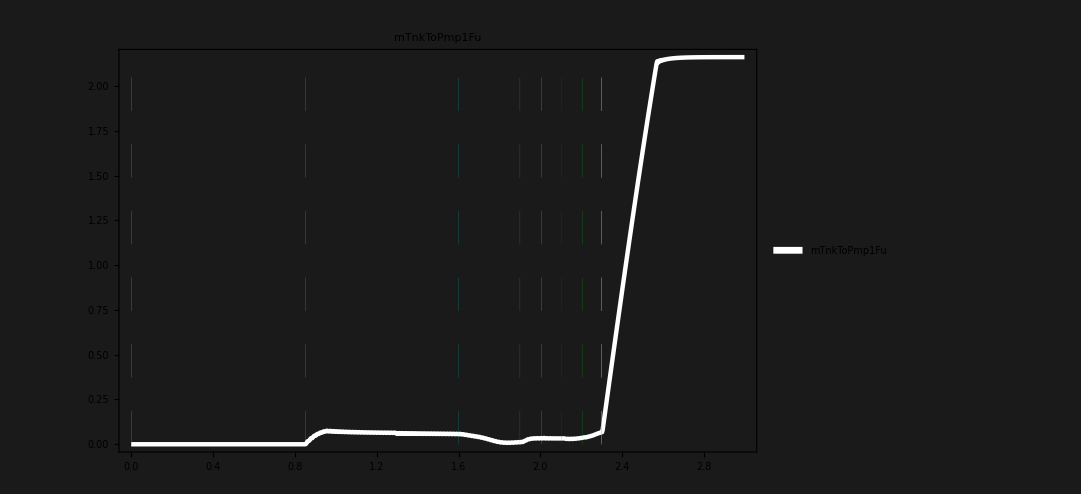

```mathematica
defPltOne [result,"mTnkToPmp1Fu"  ,1,White,Line,0.004,tValuesAssoc,All,All,ImageSize->800]
```

```mathematica
(*Show[defPltOne [result,"mGgOx"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800],defPltOne [result,"mChOx"  ,1,Cyan,Line,0.004,tValuesAssoc,All,All,ImageSize->800]]*)
```

```mathematica
(*defPltOne [result,"mGgOx"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800]
defPltOne [result,"mGgFu"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800]
defPltOne [result,"mChOx"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800]
defPltOne [result,"mChFu"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800]*)
```

```mathematica
(*defPltOne [result,"mode"  ,1,White,Line,0.004,tValuesAssoc,All,All,ImageSize->800]*)
```

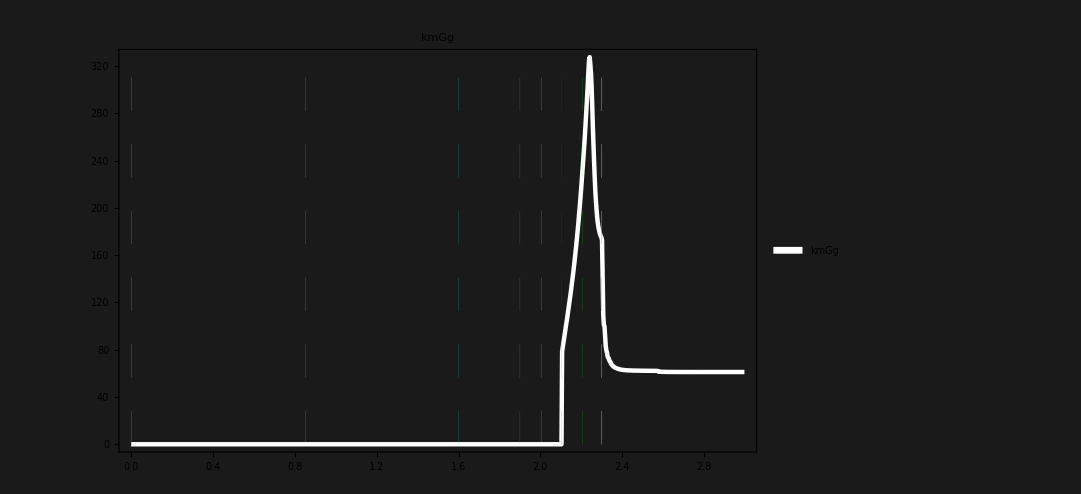

```mathematica
defPltOne [result,"kmGg"  ,1,White,Line,0.004,tValuesAssoc,All,All,ImageSize->800]
```

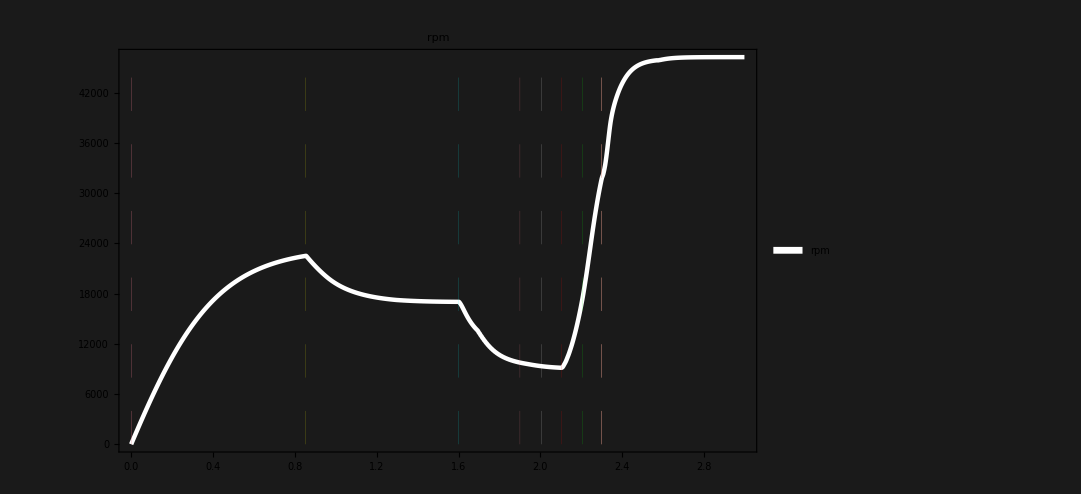

```mathematica
defPltOne [result,"rpm"  ,1,White,Line,0.004,tValuesAssoc,All,All,ImageSize->800]
```

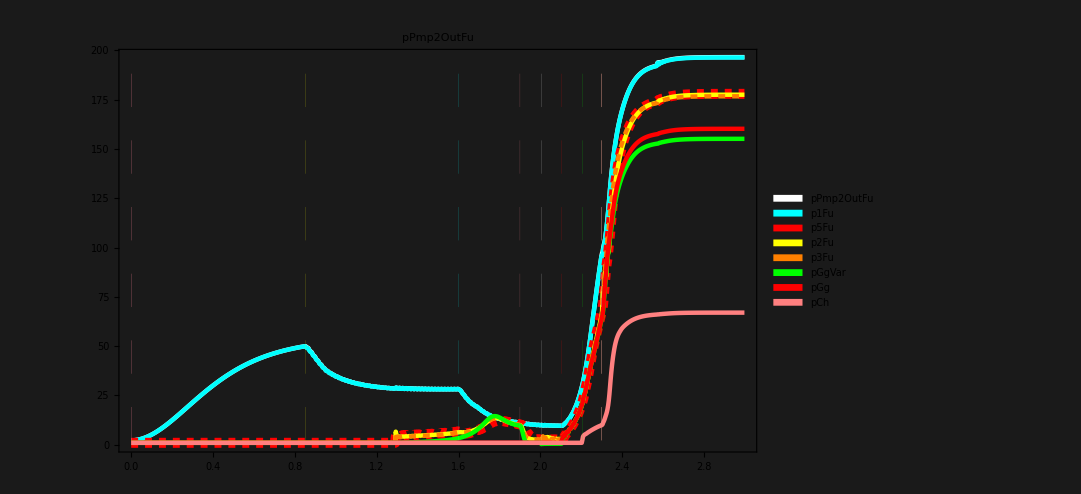

```mathematica
Show[
defPltOne [result,"pPmp2OutFu"  ,1,White,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"p1Fu"  ,1,Cyan,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"p5Fu"  ,1,Red,Dashed,0.009,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"p2Fu"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"p3Fu"  ,1,Orange,Dashed,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"pGgVar"  ,1,Green,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"pGg"  ,1,Red,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"pCh"  ,1,Pink,Line,0.004,tValuesAssoc,All,All,ImageSize->800],

PlotRange-> (*All*){All,All(*{0,450}*)}]
```

```mathematica
result["balance2"] = result["m2ToGgFu"]+result["m2ToChFu"];
result["balance1"] = result["m1To5Fu"]+result["m1To3Fu"];
```

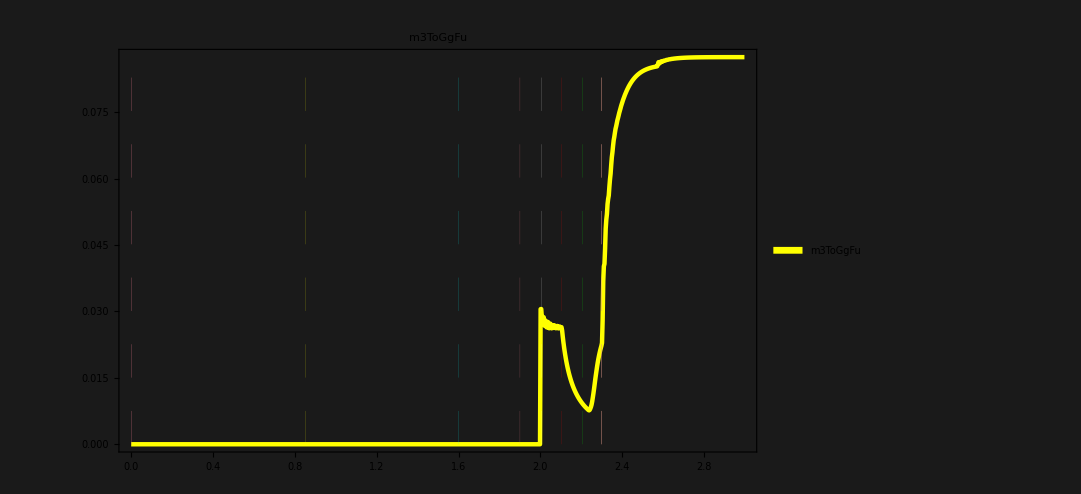

```mathematica
defPltOne [result,"m3ToGgFu"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800]
```

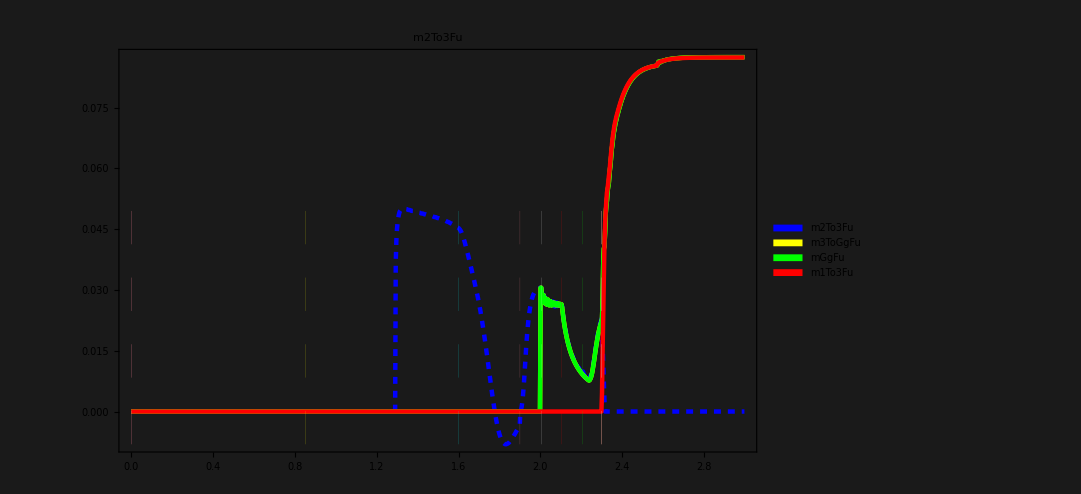

```mathematica
Show[
(*defPltOne [result,"m2ToGgFu"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800],*)
defPltOne [result,"m2To3Fu"  ,1,Blue,Dashed,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"m3ToGgFu"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"mGgFu"  ,1,Green,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"m1To3Fu"  ,1,Red,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
PlotRange-> All(*{(*{0.3,1}*)All,{0,3}}*)]
```

Transpose::nmtx: The first two levels of {{1_time,0,0.003,0.006,0.009,0.012,0.015,0.018,0.021,0.024,«991»},Missing[KeyAbsent,m1To2Fu]} cannot be transposed.

Transpose::nmtx: The first two levels of {{1_time,0.,0.003,0.006,0.009,0.012,0.015,0.018,0.021,0.024,«991»},Missing[KeyAbsent,m1To2Fu]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{{1_time,0.,0.003,0.006,0.009,0.012,0.015,0.018,0.021,0.024,«991»},Missing[KeyAbsent,m1To2Fu]}] is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: Transpose[{{1_time,0.,0.003,0.006,0.009,0.012,0.015,0.018,0.021,0.024,«991»},Missing[KeyAbsent,m2ToGgFu]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

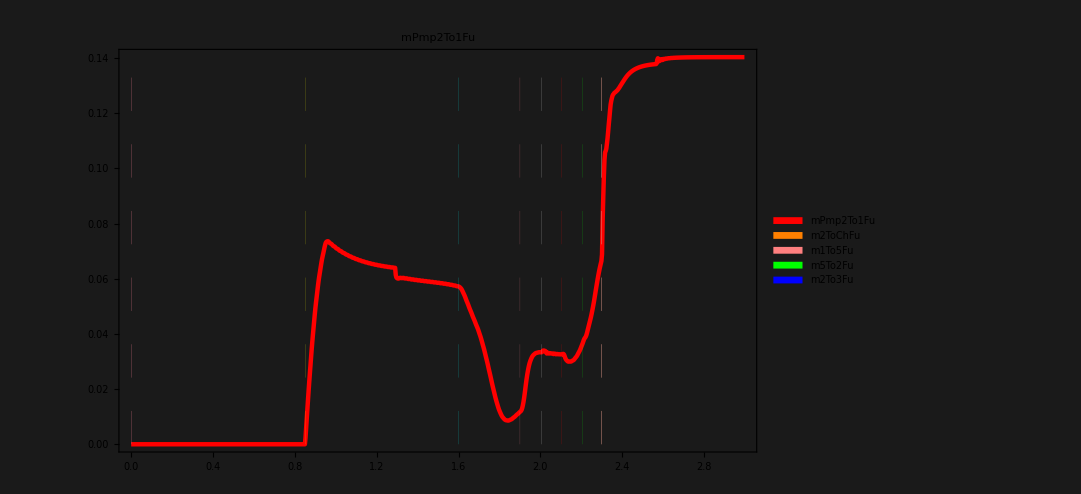
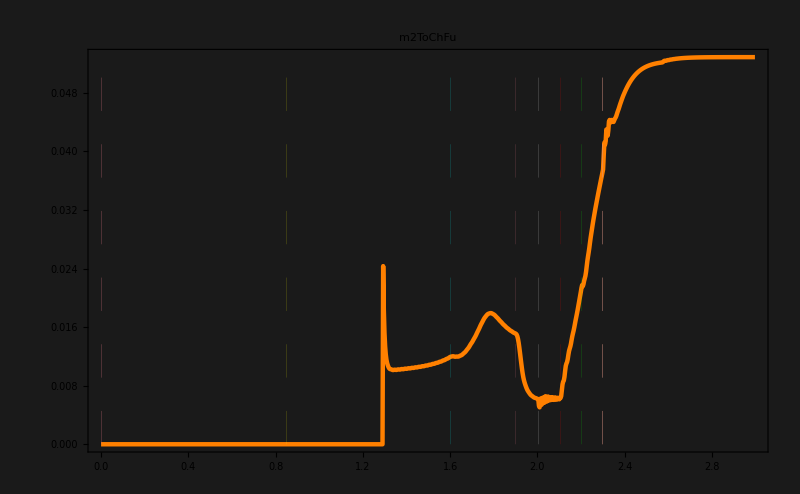
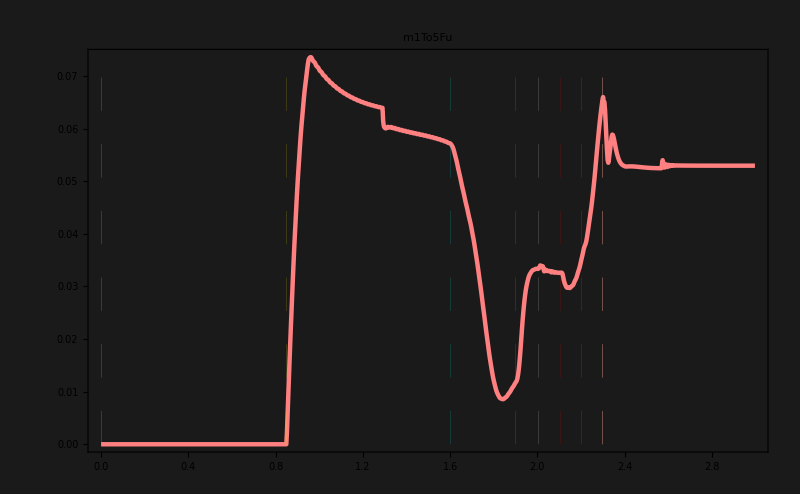
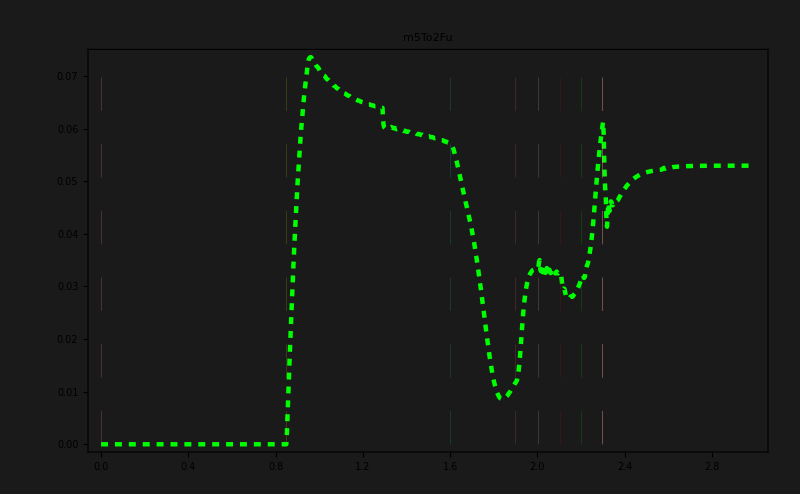
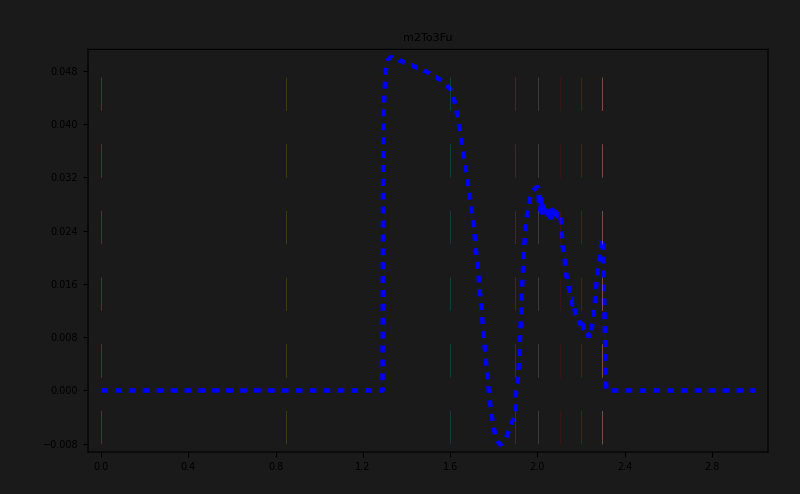
Show[-Graphics-,ListLinePlot[Transpose[{{1_time,0,0.003,0.006,0.009,0.012,0.015,0.018,0.021,0.024,0.027,0.03,0.033,0.036,0.039,0.042,0.045,0.048,0.051,0.054,0.057,0.06,0.063,0.066,0.069,0.072,0.075,0.078,0.081,0.084,0.087,0.09,0.093,0.096,0.099,0.102,0.105,0.108,0.111,0.114,0.117,0.12,0.123,0.126,0.129,0.132,0.135,0.138,0.141,0.144,0.147,0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3,0.303,0.306,0.309,0.312,0.315,0.318,0.321,0.324,0.327,0.33,0.333,0.336,0.339,0.342,0.345,0.348,0.351,0.354,0.357,0.36,0.363,0.366,0.369,0.372,0.375,0.378,0.381,0.384,0.387,0.39,0.393,0.396,0.399,0.402,0.405,0.408,0.411,0.414,0.417,0.42,0.423,0.426,0.429,0.432,0.435,0.438,0.441,0.444,0.447,0.45,0.453,0.456,0.459,0.462,0.465,0.468,0.471,0.474,0.477,0.48,0.483,0.486,0.489,0.492,0.495,0.498,0.501,0.504,0.507,0.51,0.513,0.516,0.519,0.522,0.525,0.528,0.531,0.534,0.537,0.54,0.543,0.546,0.549,0.552,0.555,0.558,0.561,0.564,0.567,0.57,0.573,0.576,0.579,0.582,0.585,0.588,0.591,0.594,0.597,0.6,0.603,0.606,0.609,0.612,0.615,0.618,0.621,0.624,0.627,0.63,0.633,0.636,0.639,0.642,0.645,0.648,0.651,0.654,0.657,0.66,0.663,0.666,0.669,0.672,0.675,0.678,0.681,0.684,0.687,0.69,0.693,0.696,0.699,0.702,0.705,0.708,0.711,0.714,0.717,0.72,0.723,0.726,0.729,0.732,0.735,0.738,0.741,0.744,0.747,0.75,0.753,0.756,0.759,0.762,0.765,0.768,0.771,0.774,0.777,0.78,0.783,0.786,0.789,0.792,0.795,0.798,0.801,0.804,0.807,0.81,0.813,0.816,0.819,0.822,0.825,0.828,0.831,0.834,0.837,0.84,0.843,0.846,0.849,0.852,0.855,0.858,0.861,0.864,0.867,0.87,0.873,0.876,0.879,0.882,0.885,0.888,0.891,0.894,0.897,0.9,0.903,0.906,0.909,0.912,0.915,0.918,0.921,0.924,0.927,0.93,0.933,0.936,0.939,0.942,0.945,0.948,0.951,0.954,0.957,0.96,0.963,0.966,0.969,0.972,0.975,0.978,0.981,0.984,0.987,0.99,0.993,0.996,0.999,1.002,1.005,1.008,1.011,1.014,1.017,1.02,1.023,1.026,1.029,1.032,1.035,1.038,1.041,1.044,1.047,1.05,1.053,1.056,1.059,1.062,1.065,1.068,1.071,1.074,1.077,1.08,1.083,1.086,1.089,1.092,1.095,1.098,1.101,1.104,1.107,1.11,1.113,1.116,1.119,1.122,1.125,1.128,1.131,1.134,1.137,1.14,1.143,1.146,1.149,1.152,1.155,1.158,1.161,1.164,1.167,1.17,1.173,1.176,1.179,1.182,1.185,1.188,1.191,1.194,1.197,1.2,1.203,1.206,1.209,1.212,1.215,1.218,1.221,1.224,1.227,1.23,1.233,1.236,1.239,1.242,1.245,1.248,1.251,1.254,1.257,1.26,1.263,1.266,1.269,1.272,1.275,1.278,1.281,1.284,1.287,1.29,1.293,1.296,1.299,1.302,1.305,1.308,1.311,1.314,1.317,1.32,1.323,1.326,1.329,1.332,1.335,1.338,1.341,1.344,1.347,1.35,1.353,1.356,1.359,1.362,1.365,1.368,1.371,1.374,1.377,1.38,1.383,1.386,1.389,1.392,1.395,1.398,1.401,1.404,1.407,1.41,1.413,1.416,1.419,1.422,1.425,1.428,1.431,1.434,1.437,1.44,1.443,1.446,1.449,1.452,1.455,1.458,1.461,1.464,1.467,1.47,1.473,1.476,1.479,1.482,1.485,1.488,1.491,1.494,1.497,1.5,1.503,1.506,1.509,1.512,1.515,1.518,1.521,1.524,1.527,1.53,1.533,1.536,1.539,1.542,1.545,1.548,1.551,1.554,1.557,1.56,1.563,1.566,1.569,1.572,1.575,1.578,1.581,1.584,1.587,1.59,1.593,1.596,1.599,1.602,1.605,1.608,1.611,1.614,1.617,1.62,1.623,1.626,1.629,1.632,1.635,1.638,1.641,1.644,1.647,1.65,1.653,1.656,1.659,1.662,1.665,1.668,1.671,1.674,1.677,1.68,1.683,1.686,1.689,1.692,1.695,1.698,1.701,1.704,1.707,1.71,1.713,1.716,1.719,1.722,1.725,1.728,1.731,1.734,1.737,1.74,1.743,1.746,1.749,1.752,1.755,1.758,1.761,1.764,1.767,1.77,1.773,1.776,1.779,1.782,1.785,1.788,1.791,1.794,1.797,1.8,1.803,1.806,1.809,1.812,1.815,1.818,1.821,1.824,1.827,1.83,1.833,1.836,1.839,1.842,1.845,1.848,1.851,1.854,1.857,1.86,1.863,1.866,1.869,1.872,1.875,1.878,1.881,1.884,1.887,1.89,1.893,1.896,1.899,1.902,1.905,1.908,1.911,1.914,1.917,1.92,1.923,1.926,1.929,1.932,1.935,1.938,1.941,1.944,1.947,1.95,1.953,1.956,1.959,1.962,1.965,1.968,1.971,1.974,1.977,1.98,1.983,1.986,1.989,1.992,1.995,1.998,2.001,2.004,2.007,2.01,2.013,2.016,2.019,2.022,2.025,2.028,2.031,2.034,2.037,2.04,2.043,2.046,2.049,2.052,2.055,2.058,2.061,2.064,2.067,2.07,2.073,2.076,2.079,2.082,2.085,2.088,2.091,2.094,2.097,2.1,2.103,2.106,2.109,2.112,2.115,2.118,2.121,2.124,2.127,2.13,2.133,2.136,2.139,2.142,2.145,2.148,2.151,2.154,2.157,2.16,2.163,2.166,2.169,2.172,2.175,2.178,2.181,2.184,2.187,2.19,2.193,2.196,2.199,2.202,2.205,2.208,2.211,2.214,2.217,2.22,2.223,2.226,2.229,2.232,2.235,2.238,2.241,2.244,2.247,2.25,2.253,2.256,2.259,2.262,2.265,2.268,2.271,2.274,2.277,2.28,2.283,2.286,2.289,2.292,2.295,2.298,2.301,2.304,2.307,2.31,2.313,2.316,2.319,2.322,2.325,2.328,2.331,2.334,2.337,2.34,2.343,2.346,2.349,2.352,2.355,2.358,2.361,2.364,2.367,2.37,2.373,2.376,2.379,2.382,2.385,2.388,2.391,2.394,2.397,2.4,2.403,2.406,2.409,2.412,2.415,2.418,2.421,2.424,2.427,2.43,2.433,2.436,2.439,2.442,2.445,2.448,2.451,2.454,2.457,2.46,2.463,2.466,2.469,2.472,2.475,2.478,2.481,2.484,2.487,2.49,2.493,2.496,2.499,2.502,2.505,2.508,2.511,2.514,2.517,2.52,2.523,2.526,2.529,2.532,2.535,2.538,2.541,2.544,2.547,2.55,2.553,2.556,2.559,2.562,2.565,2.568,2.571,2.574,2.577,2.58,2.583,2.586,2.589,2.592,2.595,2.598,2.601,2.604,2.607,2.61,2.613,2.616,2.619,2.622,2.625,2.628,2.631,2.634,2.637,2.64,2.643,2.646,2.649,2.652,2.655,2.658,2.661,2.664,2.667,2.67,2.673,2.676,2.679,2.682,2.685,2.688,2.691,2.694,2.697,2.7,2.703,2.706,2.709,2.712,2.715,2.718,2.721,2.724,2.727,2.73,2.733,2.736,2.739,2.742,2.745,2.748,2.751,2.754,2.757,2.76,2.763,2.766,2.769,2.772,2.775,2.778,2.781,2.784,2.787,2.79,2.793,2.796,2.799,2.802,2.805,2.808,2.811,2.814,2.817,2.82,2.823,2.826,2.829,2.832,2.835,2.838,2.841,2.844,2.847,2.85,2.853,2.856,2.859,2.862,2.865,2.868,2.871,2.874,2.877,2.88,2.883,2.886,2.889,2.892,2.895,2.898,2.901,2.904,2.907,2.91,2.913,2.916,2.919,2.922,2.925,2.928,2.931,2.934,2.937,2.94,2.943,2.946,2.949,2.952,2.955,2.958,2.961,2.964,2.967,2.97,2.973,2.976,2.979,2.982,2.985,2.988,2.991,2.994,2.997},Missing[KeyAbsent,m1To2Fu]}],Background→GrayLevel[0.1],Frame→True,FrameStyle→GrayLevel[1],PlotStyle→Directive[RGBColor[0, 1, 1],Line,Thickness[0.007]],PlotLabel→m1To2Fu,PlotRange→{All,All},PlotLegends→SwatchLegend[{m1To2Fu}],Epilog→{{{RGBColor[1, 0.5, 0.59],Dashing[{0.03,0.03}],Thickness[0.],Line[{{1.9,KeyAbsent},{1.9,KeyAbsent}}]},{RGBColor[0, 1, 1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{1.6,KeyAbsent},{1.6,KeyAbsent}}]},{RGBColor[1, 0.5, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.3,KeyAbsent},{2.3,KeyAbsent}}]},{RGBColor[0.76, 1., 1.],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.3,KeyAbsent},{2.3,KeyAbsent}}]},{RGBColor[0.76, 1., 0.],Dashing[{0.03,0.03}],Thickness[0.],Line[{{0.,KeyAbsent},{0.,KeyAbsent}}]},{RGBColor[1, 1, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{0.85,KeyAbsent},{0.85,KeyAbsent}}]},{RGBColor[1, 0, 1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{0.,KeyAbsent},{0.,KeyAbsent}}]},{RGBColor[1, 0.5, 0.59],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[0, 1, 1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[1, 0.5, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[0.76, 1., 1.],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[0.76, 1., 0.],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.3,KeyAbsent},{2.3,KeyAbsent}}]},{RGBColor[1, 1, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[1, 0, 1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.3,KeyAbsent},{2.3,KeyAbsent}}]},{RGBColor[1, 0, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.10388,KeyAbsent},{2.10388,KeyAbsent}}]},{RGBColor[1, 0, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100,KeyAbsent},{100,KeyAbsent}}]},{RGBColor[0, 1, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.2039,KeyAbsent},{2.2039,KeyAbsent}}]},{RGBColor[0, 1, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100,KeyAbsent},{100,KeyAbsent}}]},{GrayLevel[1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.00385,KeyAbsent},{2.00385,KeyAbsent}}]}}},ImageSize→800],-Graphics-,ListLinePlot[Transpose[{{1_time,0,0.003,0.006,0.009,0.012,0.015,0.018,0.021,0.024,0.027,0.03,0.033,0.036,0.039,0.042,0.045,0.048,0.051,0.054,0.057,0.06,0.063,0.066,0.069,0.072,0.075,0.078,0.081,0.084,0.087,0.09,0.093,0.096,0.099,0.102,0.105,0.108,0.111,0.114,0.117,0.12,0.123,0.126,0.129,0.132,0.135,0.138,0.141,0.144,0.147,0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3,0.303,0.306,0.309,0.312,0.315,0.318,0.321,0.324,0.327,0.33,0.333,0.336,0.339,0.342,0.345,0.348,0.351,0.354,0.357,0.36,0.363,0.366,0.369,0.372,0.375,0.378,0.381,0.384,0.387,0.39,0.393,0.396,0.399,0.402,0.405,0.408,0.411,0.414,0.417,0.42,0.423,0.426,0.429,0.432,0.435,0.438,0.441,0.444,0.447,0.45,0.453,0.456,0.459,0.462,0.465,0.468,0.471,0.474,0.477,0.48,0.483,0.486,0.489,0.492,0.495,0.498,0.501,0.504,0.507,0.51,0.513,0.516,0.519,0.522,0.525,0.528,0.531,0.534,0.537,0.54,0.543,0.546,0.549,0.552,0.555,0.558,0.561,0.564,0.567,0.57,0.573,0.576,0.579,0.582,0.585,0.588,0.591,0.594,0.597,0.6,0.603,0.606,0.609,0.612,0.615,0.618,0.621,0.624,0.627,0.63,0.633,0.636,0.639,0.642,0.645,0.648,0.651,0.654,0.657,0.66,0.663,0.666,0.669,0.672,0.675,0.678,0.681,0.684,0.687,0.69,0.693,0.696,0.699,0.702,0.705,0.708,0.711,0.714,0.717,0.72,0.723,0.726,0.729,0.732,0.735,0.738,0.741,0.744,0.747,0.75,0.753,0.756,0.759,0.762,0.765,0.768,0.771,0.774,0.777,0.78,0.783,0.786,0.789,0.792,0.795,0.798,0.801,0.804,0.807,0.81,0.813,0.816,0.819,0.822,0.825,0.828,0.831,0.834,0.837,0.84,0.843,0.846,0.849,0.852,0.855,0.858,0.861,0.864,0.867,0.87,0.873,0.876,0.879,0.882,0.885,0.888,0.891,0.894,0.897,0.9,0.903,0.906,0.909,0.912,0.915,0.918,0.921,0.924,0.927,0.93,0.933,0.936,0.939,0.942,0.945,0.948,0.951,0.954,0.957,0.96,0.963,0.966,0.969,0.972,0.975,0.978,0.981,0.984,0.987,0.99,0.993,0.996,0.999,1.002,1.005,1.008,1.011,1.014,1.017,1.02,1.023,1.026,1.029,1.032,1.035,1.038,1.041,1.044,1.047,1.05,1.053,1.056,1.059,1.062,1.065,1.068,1.071,1.074,1.077,1.08,1.083,1.086,1.089,1.092,1.095,1.098,1.101,1.104,1.107,1.11,1.113,1.116,1.119,1.122,1.125,1.128,1.131,1.134,1.137,1.14,1.143,1.146,1.149,1.152,1.155,1.158,1.161,1.164,1.167,1.17,1.173,1.176,1.179,1.182,1.185,1.188,1.191,1.194,1.197,1.2,1.203,1.206,1.209,1.212,1.215,1.218,1.221,1.224,1.227,1.23,1.233,1.236,1.239,1.242,1.245,1.248,1.251,1.254,1.257,1.26,1.263,1.266,1.269,1.272,1.275,1.278,1.281,1.284,1.287,1.29,1.293,1.296,1.299,1.302,1.305,1.308,1.311,1.314,1.317,1.32,1.323,1.326,1.329,1.332,1.335,1.338,1.341,1.344,1.347,1.35,1.353,1.356,1.359,1.362,1.365,1.368,1.371,1.374,1.377,1.38,1.383,1.386,1.389,1.392,1.395,1.398,1.401,1.404,1.407,1.41,1.413,1.416,1.419,1.422,1.425,1.428,1.431,1.434,1.437,1.44,1.443,1.446,1.449,1.452,1.455,1.458,1.461,1.464,1.467,1.47,1.473,1.476,1.479,1.482,1.485,1.488,1.491,1.494,1.497,1.5,1.503,1.506,1.509,1.512,1.515,1.518,1.521,1.524,1.527,1.53,1.533,1.536,1.539,1.542,1.545,1.548,1.551,1.554,1.557,1.56,1.563,1.566,1.569,1.572,1.575,1.578,1.581,1.584,1.587,1.59,1.593,1.596,1.599,1.602,1.605,1.608,1.611,1.614,1.617,1.62,1.623,1.626,1.629,1.632,1.635,1.638,1.641,1.644,1.647,1.65,1.653,1.656,1.659,1.662,1.665,1.668,1.671,1.674,1.677,1.68,1.683,1.686,1.689,1.692,1.695,1.698,1.701,1.704,1.707,1.71,1.713,1.716,1.719,1.722,1.725,1.728,1.731,1.734,1.737,1.74,1.743,1.746,1.749,1.752,1.755,1.758,1.761,1.764,1.767,1.77,1.773,1.776,1.779,1.782,1.785,1.788,1.791,1.794,1.797,1.8,1.803,1.806,1.809,1.812,1.815,1.818,1.821,1.824,1.827,1.83,1.833,1.836,1.839,1.842,1.845,1.848,1.851,1.854,1.857,1.86,1.863,1.866,1.869,1.872,1.875,1.878,1.881,1.884,1.887,1.89,1.893,1.896,1.899,1.902,1.905,1.908,1.911,1.914,1.917,1.92,1.923,1.926,1.929,1.932,1.935,1.938,1.941,1.944,1.947,1.95,1.953,1.956,1.959,1.962,1.965,1.968,1.971,1.974,1.977,1.98,1.983,1.986,1.989,1.992,1.995,1.998,2.001,2.004,2.007,2.01,2.013,2.016,2.019,2.022,2.025,2.028,2.031,2.034,2.037,2.04,2.043,2.046,2.049,2.052,2.055,2.058,2.061,2.064,2.067,2.07,2.073,2.076,2.079,2.082,2.085,2.088,2.091,2.094,2.097,2.1,2.103,2.106,2.109,2.112,2.115,2.118,2.121,2.124,2.127,2.13,2.133,2.136,2.139,2.142,2.145,2.148,2.151,2.154,2.157,2.16,2.163,2.166,2.169,2.172,2.175,2.178,2.181,2.184,2.187,2.19,2.193,2.196,2.199,2.202,2.205,2.208,2.211,2.214,2.217,2.22,2.223,2.226,2.229,2.232,2.235,2.238,2.241,2.244,2.247,2.25,2.253,2.256,2.259,2.262,2.265,2.268,2.271,2.274,2.277,2.28,2.283,2.286,2.289,2.292,2.295,2.298,2.301,2.304,2.307,2.31,2.313,2.316,2.319,2.322,2.325,2.328,2.331,2.334,2.337,2.34,2.343,2.346,2.349,2.352,2.355,2.358,2.361,2.364,2.367,2.37,2.373,2.376,2.379,2.382,2.385,2.388,2.391,2.394,2.397,2.4,2.403,2.406,2.409,2.412,2.415,2.418,2.421,2.424,2.427,2.43,2.433,2.436,2.439,2.442,2.445,2.448,2.451,2.454,2.457,2.46,2.463,2.466,2.469,2.472,2.475,2.478,2.481,2.484,2.487,2.49,2.493,2.496,2.499,2.502,2.505,2.508,2.511,2.514,2.517,2.52,2.523,2.526,2.529,2.532,2.535,2.538,2.541,2.544,2.547,2.55,2.553,2.556,2.559,2.562,2.565,2.568,2.571,2.574,2.577,2.58,2.583,2.586,2.589,2.592,2.595,2.598,2.601,2.604,2.607,2.61,2.613,2.616,2.619,2.622,2.625,2.628,2.631,2.634,2.637,2.64,2.643,2.646,2.649,2.652,2.655,2.658,2.661,2.664,2.667,2.67,2.673,2.676,2.679,2.682,2.685,2.688,2.691,2.694,2.697,2.7,2.703,2.706,2.709,2.712,2.715,2.718,2.721,2.724,2.727,2.73,2.733,2.736,2.739,2.742,2.745,2.748,2.751,2.754,2.757,2.76,2.763,2.766,2.769,2.772,2.775,2.778,2.781,2.784,2.787,2.79,2.793,2.796,2.799,2.802,2.805,2.808,2.811,2.814,2.817,2.82,2.823,2.826,2.829,2.832,2.835,2.838,2.841,2.844,2.847,2.85,2.853,2.856,2.859,2.862,2.865,2.868,2.871,2.874,2.877,2.88,2.883,2.886,2.889,2.892,2.895,2.898,2.901,2.904,2.907,2.91,2.913,2.916,2.919,2.922,2.925,2.928,2.931,2.934,2.937,2.94,2.943,2.946,2.949,2.952,2.955,2.958,2.961,2.964,2.967,2.97,2.973,2.976,2.979,2.982,2.985,2.988,2.991,2.994,2.997},Missing[KeyAbsent,m2ToGgFu]}],Background→GrayLevel[0.1],Frame→True,FrameStyle→GrayLevel[1],PlotStyle→Directive[RGBColor[1, 1, 0],Line,Thickness[0.004]],PlotLabel→m2ToGgFu,PlotRange→{All,All},PlotLegends→SwatchLegend[{m2ToGgFu}],Epilog→{{{RGBColor[1, 0.5, 0.59],Dashing[{0.03,0.03}],Thickness[0.],Line[{{1.9,KeyAbsent},{1.9,KeyAbsent}}]},{RGBColor[0, 1, 1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{1.6,KeyAbsent},{1.6,KeyAbsent}}]},{RGBColor[1, 0.5, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.3,KeyAbsent},{2.3,KeyAbsent}}]},{RGBColor[0.76, 1., 1.],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.3,KeyAbsent},{2.3,KeyAbsent}}]},{RGBColor[0.76, 1., 0.],Dashing[{0.03,0.03}],Thickness[0.],Line[{{0.,KeyAbsent},{0.,KeyAbsent}}]},{RGBColor[1, 1, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{0.85,KeyAbsent},{0.85,KeyAbsent}}]},{RGBColor[1, 0, 1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{0.,KeyAbsent},{0.,KeyAbsent}}]},{RGBColor[1, 0.5, 0.59],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[0, 1, 1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[1, 0.5, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[0.76, 1., 1.],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[0.76, 1., 0.],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.3,KeyAbsent},{2.3,KeyAbsent}}]},{RGBColor[1, 1, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100.,KeyAbsent},{100.,KeyAbsent}}]},{RGBColor[1, 0, 1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.3,KeyAbsent},{2.3,KeyAbsent}}]},{RGBColor[1, 0, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.10388,KeyAbsent},{2.10388,KeyAbsent}}]},{RGBColor[1, 0, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100,KeyAbsent},{100,KeyAbsent}}]},{RGBColor[0, 1, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.2039,KeyAbsent},{2.2039,KeyAbsent}}]},{RGBColor[0, 1, 0],Dashing[{0.03,0.03}],Thickness[0.],Line[{{100,KeyAbsent},{100,KeyAbsent}}]},{GrayLevel[1],Dashing[{0.03,0.03}],Thickness[0.],Line[{{2.00385,KeyAbsent},{2.00385,KeyAbsent}}]}}},ImageSize→800],-Graphics-,-Graphics-,-Graphics-,PlotRange→All]

```mathematica
Show[
defPltOne [result,"mPmp2To1Fu"  ,1,Red,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"m1To2Fu"  ,1,Cyan,Line,0.007,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"m2ToChFu"  ,1,Orange,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"m2ToGgFu"  ,1,Yellow,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"m1To5Fu"  ,1,Pink,Line,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"m5To2Fu"  ,1,Green,Dashed,0.004,tValuesAssoc,All,All,ImageSize->800],
defPltOne [result,"m2To3Fu"  ,1,Blue,Dashed,0.004,tValuesAssoc,All,All,ImageSize->800],
PlotRange-> All(*{(*{0.3,1}*)All,{0,3}}*)]
```

```mathematica
InterpolatingFunction[…][175.759*10^5,60]
```

741.821

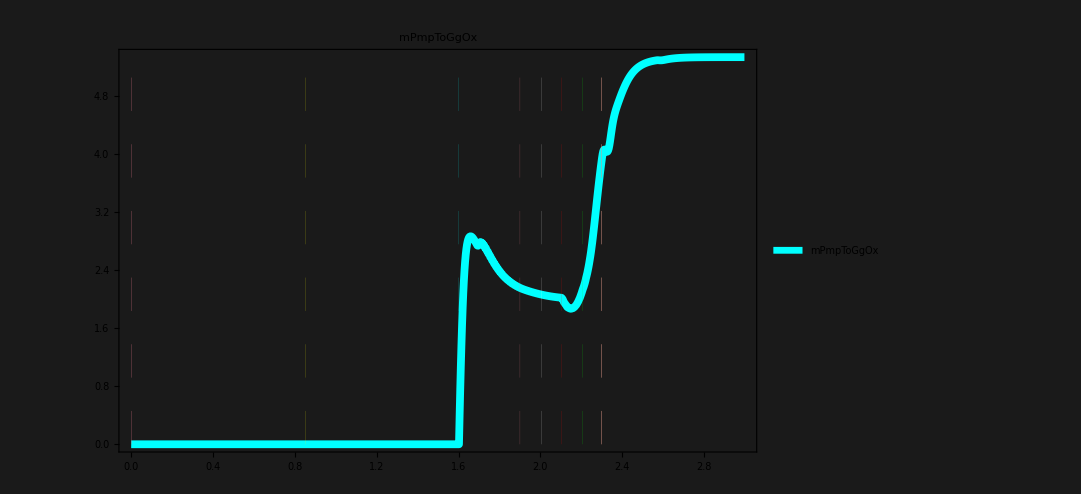

```mathematica
defPltOne [result,"mPmpToGgOx"  ,1,Cyan,Line,0.007,tValuesAssoc,All,All,ImageSize->800]
```

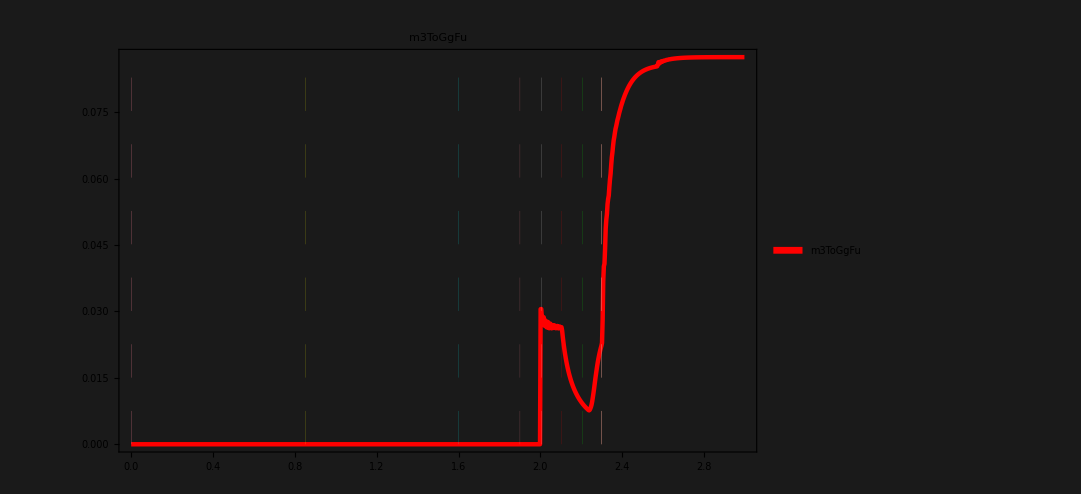

```mathematica
defPltOne [result,"m3ToGgFu"  ,1,Red,Line,0.004,tValuesAssoc,All,All,ImageSize->800]
```

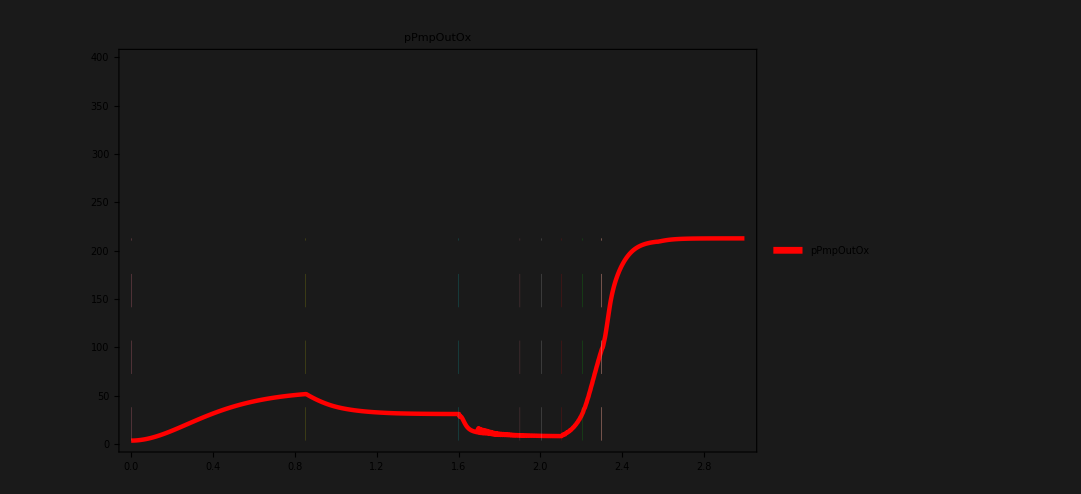

```mathematica
defPltOne [result,"pPmpOutOx"  ,1,Red,Line,0.004,tValuesAssoc,All,{0,400},ImageSize->800]
```

```mathematica
defGeneratePlotsEpilog[Sort[result],2,900,White,tValuesAssoc,"vol",PlotRange->All,PlotStyle->Directive[Thickness[0.004],RGBColor[1.,0.94,0.14]],Background->GrayLevel[0.1],FrameStyle-> White]
```

Построение графиков: {vol2ToChFu,vol2ToGgFu,volAmpTo2Fu,volPN02ToGgOx,volSV04ToChFu,mBallance2Gg,balance2}

-Graphics-

```mathematica
(*defGeneratePlotsEpilog[Sort[result],2,900,White,tValuesAssoc,"",PlotRange->All,PlotStyle->Directive[Thickness[0.004],RGBColor[1.,0.94,0.14]],Background->GrayLevel[0.1],FrameStyle-> White]*)
```

#### Отображение графиков

```mathematica
(*defPltOne [result,"mPmp1InFu",1,Green,Line,0.002,tValuesAssoc,All,All]
defPltOne [result,"pPmp1OutFu",1,Green,Line,0.002,tValuesAssoc,All,All]
defPltOne [result,"pTnkFu",1,Green,Line,0.002,tValuesAssoc,All,All]*)
```

##### one

```mathematica
(*Show[
defPltOne [result,"pVal3BallInFu",1,Green,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"pVal3BallOutFu",1,Red  ,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"fThrotValBallToComp2Fu",1*10^12,Cyan,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"mBallToComp2Fu",3*10^7,Yellow,Line,0.002,tValuesAssoc,All,All]

,PlotRange-> {All, (*All*){1*10^5,15*10^6}},ImageSize-> 1200
]*)
```

```mathematica
(*Show[defPltOne [result,"pVal2ChInFu",1,Green,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"pVal2ChOutFu",1,Red ,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"fThrotValComp1ToSpltIgnChFu",10^12,Cyan,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"mComp1ToSpltIgnChFu",1.7*10^8,Yellow,Line,0.002,tValuesAssoc,All,All]
,PlotRange-> {(*{1.3,1.5}*)All,{1*10^5,12*10^6}},ImageSize-> 1200
]*)
```

```mathematica
(*Show[defPltOne [result,"pVal4GgInFu",1,Green,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"pVal4GgOutFu",1,Red ,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"fThrotValComp1ToSpltIgnGgFu",15*10^11,Cyan,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"mComp1ToSpltIgnGgFu",10^7,Yellow,Line,0.002,tValuesAssoc,All,All]
,PlotRange-> {All, {0,1.8*10^7}},ImageSize-> 1200
]*)
```

```mathematica
(*Show[defPltOne [result,"pVal5GgInFu",1,Green,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"pVal5GgOutFu",1,Red ,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"fThrotValComp2ToSpltIgnGgFu",10^12,Cyan,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"mComp2ToSpltIgnGgFu",10^7,Yellow,Line,0.002,tValuesAssoc,All,All]
,PlotRange-> {All, {0,1.2*10^7}},ImageSize-> 1200
]*)
```

```mathematica
(*Show[
defPltOne [result,"mPmp2OutToComp1Fu"  ,1,RGBColor[0.94,0.14,1.],Dashed,0.004,tValuesAssoc,All,All],
defPltOne [result,"mComp1ToSpltIgnChFu",1,Green,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"mComp1ToSpltIgnGgFu",1,Orange,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"mBallToComp2Fu"           ,1,Red,Dashed,0.004,tValuesAssoc,All,All],
defPltOne [result,"mComp2ToSpltIgnGgFu",1,Yellow,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"mComp2ToSpltIgnChFu",1,Cyan,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"mSpltIgnChToIgnChFu",1,RGBColor[0.0,1,0.7],Line,0.004,tValuesAssoc,All,All],
defPltOne [result,"mSpltIgnGgToIgnGgFu",1,RGBColor[1.,0.46,0.08],Line,0.004,tValuesAssoc,All,All]
,PlotRange-> {All, All(*{0,1.2*10^7}*)},ImageSize-> 1200
]*)
```

```mathematica
(*Show[
defPltOne [result,"pPmp2OutFu",1,Red,Line,0.003,tValuesAssoc,All,All],
defPltOne [result,"pBallFu",1,RGBColor[1.,0.26,0.95],Line,0.003,tValuesAssoc,All,All],
defPltOne [result,"pGg",10,Orange,Line,0.003,tValuesAssoc,All,All],
defPltOne [result,"pCh",10,Green,Line,0.003,tValuesAssoc,All,All]
,PlotRange-> All(*{All,{0,1*10^6}}*),ImageSize-> 1200
]*)
```

```mathematica
(*Show[
defPltOne [dictImported,"fThrotValComp1ToSpltIgnChFu",1,Cyan,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"fThrotValComp1ToSpltIgnChFu",1,Yellow,Line,0.002,tValuesAssoc,All,All]]*)
```

```mathematica
(*defPltOne [result,"pVal4GgOutFu",1,Yellow ,Line,0.002,tValuesAssoc,All,All]*)
```

```mathematica
(*Show[
defPltOne [result,"pSpltIgnGgFu",1,Green,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"pVal5GgOutFu",1,Red ,Line,0.002,tValuesAssoc,All,All],
defPltOne [result,"pVal4GgOutFu",1,Yellow ,Line,0.002,tValuesAssoc,All,All]
(*defPltOne [result,"fThrotValComp2ToSpltIgnGgFu",10^12,Cyan,Line,0.002,tValuesAssoc,All,All],*)

,PlotRange-> {All,All(* {0,1.2*10^7}*)},ImageSize-> 1200
]*)
```

##### table

```mathematica
(*defPltOne [result,"pPmpInOx",1,Green,Line,0.002,tValuesAssoc,All,{0,5}]*)
```

Генерирование таблицы графиков, где будут выведены сразу все данные добавленные в словарь.

```mathematica
(*defGeneratePlotsEpilog[Sort[result],2,800,White,tValuesAssoc,PlotRange->All,PlotStyle->Directive[Thickness[0.004],RGBColor[1.,0.94,0.14]],Background->GrayLevel[0.1],FrameStyle-> White]*)
```

#### Импорт, экспорт, сравнение полученных результатов с импортированными данными

##### Импорт и экспорт данных

Импорт

```mathematica
(*listImported = Import[fileNameForImportAnotherData,{"Data",2}];
dictImported=defListToAssociation[Sort[listImported]];*)
```

Экспорт

```mathematica
resultDict = defListDictsToDict [resultPrint];
resultExp = Sort[defAddKeyToOnePlaceValues[resultDict]];
```

```mathematica
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx1024m"]
resultList = defDictValueListToList[resultExp];
Export[pathToExportData,Transpose[resultList],"XLSX","PageBreakBelow"->False];
SystemOpen["_4_EXPORT.xlsx"]
```

LinkObject[…]

```mathematica
(*resultNew = Monitor[Reap[
Do[res = 
Reap[Do[If[j==1||Mod[j,2]== 0,Sow[ resultDict[i][[j]]]],{j,Length[resultDict["1_time"]]}]][[2,1]];
Sow[i-> res],
{i,Keys[resultDict]}]
][[2,1]],{"i = ",i,"||  j = ",j}];
resNew = Association[resultNew];
resNew2= Sort[defAddKeyToOnePlaceValues[resNew]];
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx1024m"]
resultList1 = defDictValueListToList[resNew2];
Export[pathToExportData,resultList1,"XLSX","PageBreakBelow"->False];*)
```

##### Работа только с импортированными данными

Таблица

```mathematica
(*defRangeDisplayList[Sort[dictImported],-5,-1]//TableForm;*)
```

Графика

```mathematica
(*Show[
defOnePlotForDict[dictImported,"1_time",{"rpm",White},tValuesAssoc,PlotStyle-> Directive[Red(*RGBColor[0,0.47,0.96]*),Thickness[0.003]],Background->GrayLevel[0.1],PlotRange-> All,FrameStyle-> White],
defOnePlotForDict[result,"1_time",{"rpm",White},tValuesAssoc,PlotStyle-> Directive[RGBColor[1.,0.94,0.14],Thickness[0.003]],Background->GrayLevel[0.1],PlotRange-> All,FrameStyle-> White],PlotRange-> All]*)
```

```mathematica
(*defGeneratePlots[dictImported,2,1500,White,tValuesAssoc,PlotRange->All,PlotStyle->Directive[Thickness[0.004],RGBColor[1.,0.94,0.14]],Background->GrayLevel[0.1],FrameStyle-> White]*)
```

##### Сравнение полученных данных и импорта

```mathematica
(*time1 = AbsoluteTime[];
defGeneratePlotsComparison[dictImported,result,2,1100,White,tValuesAssoc,Background->GrayLevel[0.1],FrameStyle-> White](*//Timing*)
time2 = AbsoluteTime[];
Print["Time: ",time2-time1, " c"]*)
```

```mathematica
(*defGeneratePlotsComparison1[dictImported,result,2,1100,White,tValuesAssoc,{RGBColor[0,0.5,1.],Yellow},{0.008,0.004},Background->GrayLevel[0.1],FrameStyle-> White]*)
```

#### Отображение на одном графике сразу всех листов из файла “_3_oldData.xlsx” только для одного ключа из словаря.

```mathematica
(*allImporl=Import[fileNameForImportAnotherData,{"Data"}];
listVarListImp={};
Do[Set[Evaluate[Symbol["listImp"<>ToString[i]]],allImporl[[i]]];
AppendTo[listVarListImp,"listImp"<>ToString[i]]
,{i,Length[allImporl]}]//Quiet
listVarListImp;
listVarDictImp={};
Do[
AppendTo[listVarDictImp,"dictImp"<>StringJoin[Delete[Characters[ToString[i]],{{1},{2},{3},{4},{5},{6},{7}}]]];
Set[Evaluate[Symbol["dictImp"<>StringJoin[Delete[Characters[ToString[i]],{{1},{2},{3},{4},{5},{6},{7}}]]]],defListToAssociation[Sort[Symbol[ToString[i]]]]],{i,listVarListImp}]//Quiet
listVarDictImp;
pltAll[varY_]:=Block[{plt,lenlistDict,col},{
lenlistDict = 1/Length[listVarDictImp];
col=0;
plt = Reap[Do[
Sow[defOnePlotForDict[Symbol[i],"1_time",{varY,White},tValuesAssoc,PlotStyle-> Directive[RGBColor[1,col,0],Thickness[0.003]],Background->GrayLevel[0.1],FrameStyle-> White]];
col+=lenlistDict
,{i,listVarDictImp}]][[2,1]];
Show[plt,PlotRange-> All]
}][[1]]*)
```

```mathematica
(*pltAll["rpm"]*)
```